# 日本数式処理学会 Mathematica 分科会 @ 仙台 - Mathematica on RPi -

## Raspberry Pi (RPi) とは

教育用の低価格シングルボードコンピューター。開発用としても利用されている。

### ハードウエア

#### Type B

CPU: BCM2835(ARM)

メモリ: 512M

ストレージ: SDカード使用

電源: 5V USB microB コネクタで供給

USB(2)

イーサネット(1)

コンポジット・ビデオ出力

オーディオ出力

HDMI

ディスプレイ信号出力

ビデオ信号入力

GPIO/I2C/UART/SPI (アナログI/Oなし)

#### RPiを使用するために必要な物

本体

SDカード(4-32G、class6が推奨される)

スマホ充電器(USBmicroBコネクタ、5V、700mA以上)

キーボード

マウス

ディスプレイ+ケーブル(HDMIまたはコンポジットビデオ用)

### 対応OS

Raspbian OS
私の環境:
pi@raspberrypi /etc $ cat /etc/os-release
PRETTY_NAME=”Raspbian GNU/Linux 7 (wheezy)”
NAME=”Raspbian GNU/Linux”
VERSION_ID=”7”
VERSION=”7 (wheezy)”
ID=raspbian
ID_LIKE=debian
ANSI_COLOR=”1;31”
HOME_URL=”http://www.raspbian.org/”
SUPPORT_URL=”http://www.raspbian.org/RaspbianForums”
BUG_REPORT_URL=”http://www.raspbian.org/RaspbianBugs”

Arch Linux

Android 4.0

### ソフトウエア

デスクトップ環境(X、VNC)

パッケージ管理ツール(dpkg、apt)

ブラウザ

Pythonおよび開発環境

Mathematica

ユーティリティ、基本ソフト、アプリ等あわせて約900パッケージ
pi@raspberrypi ~ $ dpkg -l | grep ii | wc
890    8846  121567

### 価格

Type B : 4580円 (千石電商@秋葉原)

### その他のシングルボードコンピューター

BeagleBone

BeagleBoard

PandaBoard

## RPi への Mathematica のインストール

### OSのインストール・起動

ブートイメージ付きでないので、別のPCでイメージを作る必要がある。

OSイメージを入手
http://raspberrypi.org/download
にアクセス
2013-09-25-wheezy-raspbian.zip
をダウンロード

SDカードの準備
- PCにカード挿入
- カードのデバイスを確認(仮に /dev/disk1 とする)
- カードをアンマウント(挿入したまま)

.zipを展開、SDカードにイメージをコピー
$ unzip 2013-09-25-wheezy-raspbian.zip
$ sudo dd if=2013-09-25-wheezy-raspbian.img of=/dev/disk1 bs=2m
- コピーが終わったらカードをとりはずす

RPiの初回起動
- RPiにカードを挿入し、電源以外の周辺機器を接続
- USB microB コネクタに電源を接続
- システムがブートしたら初回起動後の設定を行う
-- SDカード上のファイルシステムの拡張
-- キーボード等設定
- 再起動

再起動後の設定
-- ネットワーク設定
-- ネットワーク接続を確認、OSアップデート
 $ sudo apt-get update
 $ sudo apt-get upgrade

再再起動
- もういちどOSアップデートを確認
- アップデートがあれば、インストール・再起動

### Mathematica のインストール

Mathematica をインストール
$ sudo apt-get install wolfram-engine
インタラクティブインストールなので質問に答える
/opt/Wolfram/ 以下に一式がインストールされる

Mathematica の起動確認
$ /opt/Wolfram/WolframEngine/10.0/Executables/Mathematica

## 通常版 Mathematica と RPi版 Mathematica の違い

### バージョン表示

```mathematica
$Version
```

9.0 for Mac OS X x86 (64-bit) (January 28, 2013)

In[2]:= $Version

Out[2]= "10.0 for Linux ARM (32-bit) (November 19, 2013)".00.11.00.00.00.1a.1c.1f!#%'ÿ.00.00!.00.00.00\.98ÐX.02oÚE.03(\.9c\.91.02(\.9c\.91.02b.00.00.00.00.00.00.00 .00.00.00.19.00.00.00PúÝ¶8.0cu.01.00.00X.02.1cþL.02.18.00.00.00!.00

### コマンド数

```mathematica
(namesMac=Names[])//Length
```

20888

In[1]:= Names[] // Length

Out[1]= 18608.00.00.00.001.00.00.00S.00y.00s.00t.00e.00m.00`.00D.00i.00s.00p.00l.00a.00y.00P.00a.00

```mathematica
(namesPi=Flatten[Import["/Users/kouamano/namesPi.tsv"]])//Length
```

19817

```mathematica
(onlyMac=Complement[namesMac,namesPi])//Length
```

4409

```mathematica
(onlyPi=Complement[namesPi,namesMac])//Length
```

3338

```mathematica
Intersection[namesPi,namesMac]//Length
```

16479

```mathematica
onlyMac
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z,A,B,C,D,E,F,G,H,I,J,K,L,M,N,O,P,Q,R,S,T,U,V,W,X,Y,Z,BoxForm`div$,BoxForm`ItemAspectRatio,BoxForm`iter$,BoxForm`loading,BoxForm`max$,BoxForm`min$,CalculateScan`Packages`Get1DPolarPlotRange`Get1DPolarPlotRange,CalculateScan`Packages`Get2DRange`Get2DRange,CalculateUtilities`SuggestPlotRanges`Private`Get1DRange,Cell$$986`QBinomial,Charting`PlotParser,Compile`AutoVar12,Compile`AutoVar21,Compile`$1008,Compile`$1051,Compile`$1056,Compile`$1063,Compile`$1069,Compile`$1086,Compile`$1105,Compile`$1112,Compile`$1125,Compile`$1183,Compile`$1212,Compile`$1215,Compile`$1218,Compile`$1227,Compile`$1243,Compile`$1253,Compile`$1281,Compile`$793,Compile`$799,Compile`$806,Compile`$831,Compile`$848,Compile`$850,Compile`$897,Compile`$900,Compile`$903,Compile`$907,Compile`$913,Compile`$930,Compile`$943,Compile`$965,ComputationalGeometry`Methods`ConvexHull3D,ComputationalGeometry`Methods`GraphicsComplexModel,ComputationalGeometry`Methods`VertexIntersection,ComputationalGeometry`Methods`VertexTolerance,Control`AckermannGains,Control`AffineModelUtilities`adjoinDistribution,Control`AffineModelUtilities`assInputMatrixTest,Control`AffineModelUtilities`assMold,Control`AffineModelUtilities`assOutputVectorTest,Control`AffineModelUtilities`assStateVectorTest,Control`AffineModelUtilities`asysCasting,Control`AffineModelUtilities`completeNonSingularTransformation,Control`AffineModelUtilities`getModelVars,Control`AffineModelUtilities`gmold,Control`AffineModelUtilities`inverseCoordinateTransform,Control`AffineModelUtilities`nassMold,Control`AffineModelUtilities`nonlinearDTMQ,Control`AffineModelUtilities`nsysCasting,Control`AffineModelUtilities`residueAndTemporalArguments,Control`AffineModelUtilities`ssCasting,Control`AffineModelUtilities`ssMold,Control`AffineModelUtilities`taylorApprox,Control`AffineModelUtilities`taylorApproxOrder,Control`AffineModelUtilities`temporalVariableCasting,Control`AffineModelUtilities`varsTest,Control`AffineModelUtilities`varsTest0,Control`AffineModelUtilities`varsTestD,Control`AffineModelUtilities`varsTestG,Control`AffineModelUtilities`varsTestV,Control`AffineModelUtilities`xssToss,Control`affinestatespaceForm,Control`AffineStateSpaceModel,Control`AMIGOFrequencyResponsePIDTuning,Control`AMIGOStepResponsePIDTuning,Control`ApproximateCancel,Control`ApproximatePolynomialGCD,Control`AsymptoticOutputTracker,Control`BilinearTransform,Control`BlockDiagonalMatrix,Control`CenterManifoldStateSpaceModel,Control`CHRPIDTuning,Control`CohenCoonPIDTuning,Control`CommonDump`automaticTolerance,Control`CommonDump`dimensions,Control`CommonDump`emptyQ,Control`CommonDump`happyDotQ,Control`CommonDump`Legacy80TagBoxRules,Control`CommonDump`noD,Control`CommonDump`noQ,Control`CommonDump`notoptionQ,Control`CommonDump`optionsDelayed,Control`CommonDump`padZeros,Control`CommonDump`precision,Control`CommonDump`pVar,Control`CommonDump`sameLengthQ,Control`CommonDump`SquareMatrixQ,Control`CommonDump`systemQ,Control`CommonDump`tfMult,Control`CommonDump`ToMonic,Control`CommonDump`validOptionsQ,Control`CommutativeDistributionQ,Control`ComplexRootProbability,Control`ComposeIntegralCurves,Control`ConnectionsDump`flattenBlockModels,Control`ConnectionsDump`inputwrapper,Control`ConnectionsDump`sisoCombine,Control`ConnectionsDump`standardizeGenConnections,Control`ConnectionsDump`viaSisoSS,Control`ControllableSubsystem,Control`CycleOptions,Control`DecoupleByNeutralStability,Control`DecouplingMatrix,Control`DecouplingZeros,Control`defaultmodelVariables,Control`DegenerateModelQ,Control`disambiguateModelIndices,Control`DiscreteRiccatiSolveVerify,Control`DistributionBasis,Control`DistributionComplement,Control`DistributionIntersection,Control`DominantPolePIDTuning,Control`EquationForm,Control`Exact,Control`ExactConversionFunction,Control`ExactLinearizationData,Control`FailureMessageName,Control`FailureTest,Control`FeedbackLinearizableQ,Control`FeedbackLinearize,Control`FullInformationOutputRegulator,Control`FullRankControllabilityMatrix,Control`FullRankObservabilityMatrix,Control`GetSamplingPeriod,Control`GetVariable,Control`ImaginaryToRealRatio,Control`impulsecontrollableQ,Control`impulseobservableQ,Control`InflateSM,Control`InputOutputLinearize,Control`InputStateLinearize,Control`InputVariables,Control`IntegralCurve,Control`IntegralParametricManifold,Control`InvolutiveDistributionQ,Control`KappaTauFrequencyResponsePIDTuning,Control`KappaTauStepResponsePIDTuning,Control`KNVDGains,Control`LambdaPIDTuning,Control`LeftCoprimeQ,Control`LeftGCDDecomposition,Control`LegacyDiscreteRiccatiSolve,Control`LegacyRiccatiSolve,ControllerDuration,Control`LFDisturbanceRejectionPIDTuning,Control`LieBracket,Control`LieDerivative,Control`MappingFunction,Control`MatrixCondition,Control`MaximalInvariantDistribution,Control`McMillanForm,Control`MethodOfMoments,Control`MinimalInvariantCoDistribution,Control`MinimalInvariantDistribution,Control`MinimalSizeSystemMatrixModel,Control`MinimumErrorIntegralPIDTuning,Control`MultipleRootProbability,Control`NegativeDefiniteQ,Control`nonaffinestatespaceForm,Control`NonlinearStateSpaceModel,Control`NonSingularControllabilityGramian,Control`NonSingularObservabilityGramian,Control`NumeratorDenominatorCoefficients,Control`NumeratorDenominatorEnforce,Control`NumeratorDenominatorMap,Control`NumeratorLCD,Control`ObservableSubsystem,Control`OrthonormalComplement,Control`OutputResponse1D,Control`OutputResponse2D,Control`OutputResponseLT,Control`OutputResponsePlot,Control`OutputVariables,Control`PCSModelsDump`leftmatrixfraction,Control`PCSModelsDump`rightmatrixfraction,Control`PCSModelsDump`systemmatrix,Control`PlotUtilities`phaseSmoothing,Control`PoleAssignmentDump`impulsefreegains,Control`PolePlacementPIDTuning,Control`PositiveSemiDefiniteQ,Control`PropertiesDump`controllabilitymatrix0,Control`PropertiesDump`controllableQ,Control`PropertiesDump`fullRankPBHMatrixDet,Control`PrototypeTypesetting,Control`RandomSystem,Control`RealizationsDump`dynamicDecomposition,Control`RealizationsDump`jordandecomposition,Control`RealizationsDump`kroneckermodeldecomposition,Control`RealRootProbability,Control`RedressNonEquilibrium,Control`ResetStateSpaceModelEquilibrium,Control`RiccatiSolveVerify,Control`RightCoprimeQ,Control`RightGCDDecomposition,Control`RobustLoopShapePIDTuning,Control`secondsystemmatrixForm,Control`SingularQ,Control`SkogestadIMCPIDTuning,Control`SmithForm,Control`SpecialPointProbability,Control`SpecialPoints,Control`SpecifiedStabilityMarginsGains,Control`StateOutputLinearize,Control`statespaceForm,Control`StateVariables,Control`StraightenVectorFields,Control`SymmetricQ,Control`SystemsModelMerge,Control`SystemsModelVectorRelativeOrder,Control`ThreeParam2Point,Control`ThreeParamGraphical,Control`ThreeParamGraphNishi,Control`TimeDelaysDump`delaySSfeedback,Control`TimeDelaysDump`expandedSStoInternal,Control`TimeDelaysDump`internalToExpandedSS,Control`TimeDelaysDump`iodelayQ,Control`TimeDelaysDump`StableDelayBound,Control`TimeVariable,Control`transferfunctionForm,Control`TriangularControllabilityDecomposition,Control`TriangularObservabilityDecomposition,Control`TwoParamGraphical,Control`TwoParamWithResTime,Control`TyreusLuybenPIDTuning,Control`VectorRelativeOrderCompensator,Control`ZeroPoleMapping,Control`ZeroPoleToTimeConstants,Control`ZieglerNicholsDesign,Control`ZieglerNicholsFrequencyResponsePIDTuning,Control`$SMVariablesIgnoreQ,Data`DataArrayKeys,Data`DataArrayPut,Data`DataArrayRules,DataPaclets`CalendarDataDump`dϵ,DataPaclets`CalendarDataDump`dϵ$,DataPaclets`CalendarDataDump`dψ,DataPaclets`CalendarDataDump`dψ$,DataPaclets`CalendarDataDump`planetβ,DataPaclets`CalendarDataDump`planetβ$,DataPaclets`CalendarDataDump`planetλ,DataPaclets`CalendarDataDump`planetλ$,DataPaclets`CalendarDataDump`sunβ,DataPaclets`CalendarDataDump`sunβ$,DataPaclets`CalendarDataDump`sunλ,DataPaclets`CalendarDataDump`sunλ$,DataPaclets`CalendarDataDump`sβ,DataPaclets`CalendarDataDump`sβ$,DataPaclets`CalendarDataDump`sλ,DataPaclets`CalendarDataDump`sλ$,DataPaclets`CalendarDataDump`β,DataPaclets`CalendarDataDump`λ,DataPaclets`CommonDump`c,DataPaclets`CommonDump`charHash,DataPaclets`CommonDump`combineHashValues,DataPaclets`CommonDump`c$,DataPaclets`CommonDump`displayName,DataPaclets`CommonDump`displayName$,DataPaclets`CommonDump`expr,DataPaclets`CommonDump`failexpr,DataPaclets`CommonDump`filename,DataPaclets`CommonDump`fileName,DataPaclets`CommonDump`getFileName,DataPaclets`CommonDump`h,DataPaclets`CommonDump`h0,DataPaclets`CommonDump`h2,DataPaclets`CommonDump`HaveFEQ,DataPaclets`CommonDump`h$,DataPaclets`CommonDump`i,DataPaclets`CommonDump`Initialize,DataPaclets`CommonDump`internalImportData,DataPaclets`CommonDump`key,DataPaclets`CommonDump`key$,DataPaclets`CommonDump`len,DataPaclets`CommonDump`len$,DataPaclets`CommonDump`link,DataPaclets`CommonDump`link$,DataPaclets`CommonDump`location,DataPaclets`CommonDump`location$,DataPaclets`CommonDump`minVer,DataPaclets`CommonDump`name,DataPaclets`CommonDump`obj,DataPaclets`CommonDump`output,DataPaclets`CommonDump`output$,DataPaclets`CommonDump`p,DataPaclets`CommonDump`paclet,DataPaclets`CommonDump`pacletName,DataPaclets`CommonDump`paclet$,DataPaclets`CommonDump`path,DataPaclets`CommonDump`path$,DataPaclets`CommonDump`p$,DataPaclets`CommonDump`res,DataPaclets`CommonDump`s,DataPaclets`CommonDump`stringHash,DataPaclets`CommonDump`symb,DataPaclets`CommonDump`toMint,DataPaclets`CommonDump`unit,DataPaclets`CommonDump`UnitNames,DataPaclets`CommonDump`UnitNotations,DataPaclets`CommonDump`update,DataPaclets`CommonDump`update$,DataPaclets`CommonDump`ver,DataPaclets`CommonDump`wdx,DataPaclets`CommonDump`wdx$,DataPaclets`CommonDump`$HashPrime,DataPaclets`CommonDump`$MintMask,DataPaclets`CommonDump`$ProgressThreshold,DataPaclets`CommonDump`$StringLength2,DynamicDump`act,DynamicDump`action,DynamicDump`actionElementToBoxes,DynamicDump`actionElementToExpression,DynamicDump`actionElementToLabel,DynamicDump`actionListToBoxes,DynamicDump`actionListToExpression,DynamicDump`actionListToLabels,DynamicDump`actionMenuAppearance,DynamicDump`activestyle,DynamicDump`addLabelStyle,DynamicDump`align,DynamicDump`alignment,DynamicDump`alt,DynamicDump`alternateBoxes,DynamicDump`alternateBoxes$,DynamicDump`alt$,DynamicDump`animator,DynamicDump`animatorOptionsToBoxOptions,DynamicDump`animatorOptionToBoxOption,DynamicDump`ap,DynamicDump`app,DynamicDump`appearance,DynamicDump`appearance$,DynamicDump`app$,DynamicDump`aRange,DynamicDump`autoaction,DynamicDump`background,DynamicDump`baselineposition,DynamicDump`basestyle,DynamicDump`bg,DynamicDump`bg$,DynamicDump`bool,DynamicDump`boxLabel,DynamicDump`bp,DynamicDump`bp$,DynamicDump`buttonBarAppearance,DynamicDump`buttonopts,DynamicDump`buttons,DynamicDump`cat,DynamicDump`checkArgCount,DynamicDump`checkboxBarDelimiter,DynamicDump`checkboxBarElementToCheckbox,DynamicDump`checkboxBarToCheckboxList,DynamicDump`colorSliderType,DynamicDump`continuousaction,DynamicDump`control,DynamicDump`controlargs,DynamicDump`controloptions,DynamicDump`controloptions$,DynamicDump`controlopts,DynamicDump`controlplacement,DynamicDump`controls,DynamicDump`ControlToBoxes,DynamicDump`ControlToExpression,DynamicDump`core,DynamicDump`corePane,DynamicDump`counter,DynamicDump`cStyle,DynamicDump`cStyle$,DynamicDump`data,DynamicDump`data$,DynamicDump`defaultboxes,DynamicDump`defaultBoxes,DynamicDump`defaultBoxes$,DynamicDump`deployed,DynamicDump`direction,DynamicDump`dynamicOrNumericOrInfiniteQ,DynamicDump`dynamicOrNumericQ,DynamicDump`elements,DynamicDump`enabled,DynamicDump`enabled$,DynamicDump`eval,DynamicDump`eval$,DynamicDump`fieldTypeQ,DynamicDump`fm,DynamicDump`fnsButton,DynamicDump`fnsButtonFunction,DynamicDump`fnsDialogType,DynamicDump`fnsFilter,DynamicDump`font,DynamicDump`formatSlideViewCore,DynamicDump`framemargins,DynamicDump`fromListPickerBoxBackground,DynamicDump`getRelevantOpts,DynamicDump`GetSlidingJump,DynamicDump`GetSlidingWidth,DynamicDump`gridoptions,DynamicDump`heldAlternate,DynamicDump`heldAlternate$,DynamicDump`heldDefault,DynamicDump`heldDefault$,DynamicDump`heldExpr,DynamicDump`heldExpr$,DynamicDump`heldTip,DynamicDump`heldTip$,DynamicDump`heldValues,DynamicDump`heldValues$,DynamicDump`hotspot,DynamicDump`hyperlinkBaseStyle,DynamicDump`hyperlinkButtonData,DynamicDump`hyperlinkButtonNote,DynamicDump`hyperlinkDisplay,DynamicDump`hyperlinkMouseover,DynamicDump`hyperlinkMouseoverActiveStyle,DynamicDump`hyperlinkMouseoverBaseStyle,DynamicDump`i,DynamicDump`iFlipView,DynamicDump`im,DynamicDump`imagemargins,DynamicDump`imagemargins$,DynamicDump`imagesize,DynamicDump`imagesize$,DynamicDump`iMenuView,DynamicDump`im$,DynamicDump`index,DynamicDump`indexes,DynamicDump`indexes$,DynamicDump`init1,DynamicDump`init1$,DynamicDump`init2,DynamicDump`init2$,DynamicDump`inputfield,DynamicDump`iOpenerView,DynamicDump`iPopupView,DynamicDump`iPopupView3,DynamicDump`iSlideAnimator,DynamicDump`iSlideButtons,DynamicDump`iSlideCounter,DynamicDump`iSlideTooltip,DynamicDump`iSlideView,DynamicDump`iSlidingTabView,DynamicDump`iTrigger,DynamicDump`j,DynamicDump`jump,DynamicDump`lab,DynamicDump`label,DynamicDump`labelboxes,DynamicDump`labeledCheckbox,DynamicDump`labeledCheckboxGrid,DynamicDump`labeledRadioButton,DynamicDump`labeledRadioButtonGrid,DynamicDump`labeledSliderBoxes,DynamicDump`labeloptions,DynamicDump`labeloptions$,DynamicDump`labelopts,DynamicDump`label$,DynamicDump`labsty,DynamicDump`layers,DynamicDump`layout,DynamicDump`LegacyActionMenuMakeBoxes,DynamicDump`len,DynamicDump`lev,DynamicDump`lineGray,DynamicDump`lis,DynamicDump`listCases,DynamicDump`locatorPaneAppearanceMakeBoxes,DynamicDump`locatorPaneOptionMakeBoxes,DynamicDump`locatorPaneOptionsMakeBoxes,DynamicDump`makeButton,DynamicDump`makeButtonBarBoxes,DynamicDump`makeButtonBarElement,DynamicDump`MakeControlToBoxesRules,DynamicDump`MakeControlToExpressionRules,DynamicDump`makeHyperlink,DynamicDump`makeInputFieldNonDynamicBoxes,DynamicDump`makePasteButton,DynamicDump`MakeSlidingTabViewBoxes,DynamicDump`MapHeldFunction,DynamicDump`mapp,DynamicDump`mapp$,DynamicDump`maxstart,DynamicDump`menu,DynamicDump`menuElementToBoxPair,DynamicDump`menuitems,DynamicDump`menuListToBoxes,DynamicDump`menuViewInitialValue,DynamicDump`method,DynamicDump`method$,DynamicDump`myHold,DynamicDump`nameboxes,DynamicDump`nameboxes$,DynamicDump`nb,DynamicDump`normal,DynamicDump`normalBoxes,DynamicDump`normalBoxes$,DynamicDump`normalize,DynamicDump`normalizeControlPlacement,DynamicDump`normalize$,DynamicDump`numericQ,DynamicDump`o,DynamicDump`one,DynamicDump`options,DynamicDump`options$,DynamicDump`opts1,DynamicDump`opts2,DynamicDump`otherrage,DynamicDump`otherrange,DynamicDump`over,DynamicDump`overBoxes,DynamicDump`overBoxes$,DynamicDump`p,DynamicDump`pacleturiQ,DynamicDump`page,DynamicDump`panelitems,DynamicDump`paneSelectorElementToBoxes,DynamicDump`paneSelectorElementToExpression,DynamicDump`paneSelectorListToBoxes,DynamicDump`pl,DynamicDump`placeControls,DynamicDump`placement,DynamicDump`popupMenuBoxAppearanceForActionMenu,DynamicDump`pos,DynamicDump`pRange,DynamicDump`radioButtonBarDelimiter,DynamicDump`radioButtonBarElementToRadioButton,DynamicDump`radioButtonBarToRadioButtonList,DynamicDump`radiobuttons,DynamicDump`radiobuttons$,DynamicDump`range,DynamicDump`resource,DynamicDump`resource$,DynamicDump`rest,DynamicDump`result,DynamicDump`result$,DynamicDump`running,DynamicDump`scrolltag,DynamicDump`select,DynamicDump`seq,DynamicDump`SetAttribtues,DynamicDump`setterBarElement,DynamicDump`setterBarElementToSetter,DynamicDump`setterBarToSetterList,DynamicDump`setters,DynamicDump`setters$,DynamicDump`side,DynamicDump`size,DynamicDump`slider,DynamicDump`slideViewCoreFrame,DynamicDump`slidingAppearanceQ,DynamicDump`spacings,DynamicDump`sRange,DynamicDump`sRange2D,DynamicDump`start,DynamicDump`sty,DynamicDump`sty$,DynamicDump`sVector,DynamicDump`symbox,DynamicDump`tabdata,DynamicDump`tabElementToBoxes,DynamicDump`tabElementToExpression,DynamicDump`tabListToBoxes,DynamicDump`tag,DynamicDump`textQ,DynamicDump`tip,DynamicDump`toggleControlMakeBoxes,DynamicDump`toggleControlMakeExpression,DynamicDump`togglerBarElement,DynamicDump`togglerBarElementToSetter,DynamicDump`togglerBarToSetterList,DynamicDump`togglerDynamic,DynamicDump`toHeldExpr,DynamicDump`toListPickerBoxBackground,DynamicDump`toseq,DynamicDump`tRange,DynamicDump`typesetListPickerOption,DynamicDump`typesetListPickerOptions,DynamicDump`untypesetListPickerOption,DynamicDump`untypesetListPickerOptions,DynamicDump`ups,DynamicDump`url,DynamicDump`vals,DynamicDump`valueElementToBoxes,DynamicDump`valueElementToExpression,DynamicDump`valueList,DynamicDump`valueListToBoxes,DynamicDump`valueListToExpression,DynamicDump`valueList$,DynamicDump`values,DynamicDump`values$,DynamicDump`w,DynamicDump`wasOn,DynamicDump`width,DynamicDump`$AllSlideViewAnimatorElements,DynamicDump`$AllSlideViewButtonElements,DynamicDump`$AllSlideViewCounterElements,DynamicDump`$AllSlideViewElements,DynamicDump`$AutomaticActionMenuAppearance,DynamicDump`$AutomaticSlideViewElements,DynamicDump`$colorsettercolor,DynamicDump`$colorslidercolor,DynamicDump`$customAnimatorAppearances,DynamicDump`$FileNameSetterDefaultFilter,DynamicDump`$FileNameSetterDefaultLabel,DynamicDump`$FileNameSetterDefaultType,DynamicDump`$FileNameSetterDialogTypes,DynamicDump`$SlideViewSlideNumberSeparator,DynamicDump`$SlidingTabViewDefaultWidth,DynamicDump`$StatusAreaForm,DynamicDump`$TextualTooltipStyle,Experimental`IntervalSlider,Experimental`RawData,Explore`ExploreDump`a,Explore`ExploreDump`after,Explore`ExploreDump`args,Explore`ExploreDump`aspectratio,Explore`ExploreDump`automaticPlot,Explore`ExploreDump`a$,Explore`ExploreDump`b,Explore`ExploreDump`before,Explore`ExploreDump`body,Explore`ExploreDump`boxes,Explore`ExploreDump`boxid,Explore`ExploreDump`boxidValue,Explore`ExploreDump`boxid$,Explore`ExploreDump`b$,Explore`ExploreDump`c,Explore`ExploreDump`cache,Explore`ExploreDump`calculate,Explore`ExploreDump`center,Explore`ExploreDump`computingQ,Explore`ExploreDump`c$,Explore`ExploreDump`d,Explore`ExploreDump`data,Explore`ExploreDump`debug,Explore`ExploreDump`DebugEvaluate,Explore`ExploreDump`DebugPrint,Explore`ExploreDump`def,Explore`ExploreDump`defaultrange,Explore`ExploreDump`defaultranges,Explore`ExploreDump`defoptions,Explore`ExploreDump`defoptions$,Explore`ExploreDump`domain,Explore`ExploreDump`epi,Explore`ExploreDump`exploreGraphicsOptionQ,Explore`ExploreDump`explorer,Explore`ExploreDump`explorerType,Explore`ExploreDump`expr,Explore`ExploreDump`expr$,Explore`ExploreDump`f,Explore`ExploreDump`fill,Explore`ExploreDump`fmt,Explore`ExploreDump`frameticks,Explore`ExploreDump`funcOpener,Explore`ExploreDump`funcs,Explore`ExploreDump`functions,Explore`ExploreDump`g,Explore`ExploreDump`getTemplateValue,Explore`ExploreDump`graphics,Explore`ExploreDump`graphicsOptions,Explore`ExploreDump`g$,Explore`ExploreDump`halflength,Explore`ExploreDump`hasPlotInput,Explore`ExploreDump`heldParametersList,Explore`ExploreDump`initializeExplorerTools,Explore`ExploreDump`initializeMesh,Explore`ExploreDump`initializeParameters,Explore`ExploreDump`initializePlotVars,Explore`ExploreDump`input,Explore`ExploreDump`input$,Explore`ExploreDump`interface,Explore`ExploreDump`k,Explore`ExploreDump`k$,Explore`ExploreDump`lis,Explore`ExploreDump`logs,Explore`ExploreDump`MakeExploreBoxes,Explore`ExploreDump`makeExploreCmd,Explore`ExploreDump`mesh,Explore`ExploreDump`mode,Explore`ExploreDump`modesave,Explore`ExploreDump`name,Explore`ExploreDump`nb,Explore`ExploreDump`nbopts,Explore`ExploreDump`nb$,Explore`ExploreDump`newcenter,Explore`ExploreDump`nn,Explore`ExploreDump`nn$,Explore`ExploreDump`openers,Explore`ExploreDump`options,Explore`ExploreDump`optionsData,Explore`ExploreDump`options$,Explore`ExploreDump`optionValues,Explore`ExploreDump`opts,Explore`ExploreDump`othervars,Explore`ExploreDump`p,Explore`ExploreDump`pane,Explore`ExploreDump`panesize,Explore`ExploreDump`param,Explore`ExploreDump`parameters,Explore`ExploreDump`params,Explore`ExploreDump`paramsOpener,Explore`ExploreDump`plot,Explore`ExploreDump`Plot,Explore`ExploreDump`plotableQ,Explore`ExploreDump`plotOptions,Explore`ExploreDump`plotQ,Explore`ExploreDump`plotrange,Explore`ExploreDump`plotrangesave,Explore`ExploreDump`plotscale,Explore`ExploreDump`prims,Explore`ExploreDump`prims$,Explore`ExploreDump`pspace,Explore`ExploreDump`p$,Explore`ExploreDump`range1,Explore`ExploreDump`range2,Explore`ExploreDump`ranges,Explore`ExploreDump`ranges$,Explore`ExploreDump`real,Explore`ExploreDump`realtime,Explore`ExploreDump`rectHighlight,Explore`ExploreDump`sc,Explore`ExploreDump`scale,Explore`ExploreDump`sel,Explore`ExploreDump`select,Explore`ExploreDump`selHighlight,Explore`ExploreDump`sel$,Explore`ExploreDump`shade,Explore`ExploreDump`show,Explore`ExploreDump`showControls,Explore`ExploreDump`size,Explore`ExploreDump`specs,Explore`ExploreDump`StreamPlot,Explore`ExploreDump`streamQ,Explore`ExploreDump`strictToBoxes,Explore`ExploreDump`style,Explore`ExploreDump`sym,Explore`ExploreDump`t,Explore`ExploreDump`tag,Explore`ExploreDump`tagbox,Explore`ExploreDump`temp,Explore`ExploreDump`temp$,Explore`ExploreDump`tools,Explore`ExploreDump`type,Explore`ExploreDump`useropts,Explore`ExploreDump`val,Explore`ExploreDump`var,Explore`ExploreDump`vars,Explore`ExploreDump`version,Explore`ExploreDump`vizQ,Explore`ExploreDump`wasProtected,Explore`ExploreDump`x,Explore`ExploreDump`x$,Explore`ExploreDump`y,Explore`ExploreDump`y$,Explore`ExploreDump`zoom,Explore`ExploreDump`$DebugPrint,Explore`ExploreDump`$dialog,Explore`ExploreDump`$eval,Explore`ExploreDump`$ExplorePlots,Explore`ExploreDump`$explorers,Explore`ExploreDump`$Templated,Explore`ExploreDump`$TemplateVersion,FE`DynamicModuleVariableList$19,FE`NoValue,FE`PredictiveInterfaceDump`alternateTypes$$19,FE`PredictiveInterfaceDump`keys$$19,FE`PredictiveInterfaceDump`mode$$19,FE`PredictiveInterfaceDump`predictions$$19,FE`PredictiveInterfaceDump`prune$$19,FE`PredictiveInterfaceDump`rollup$$19,FE`PredictiveInterfaceDump`semanticType$$19,FE`$RasterizingQ,FrontEnd`AttachCell,FrontEnd`ImageEditorTargetObject,FrontEnd`NotebookPredictions,FrontEnd`PastePrediction,FrontEnd`Private`f$,FrontEnd`Private`Inactive,FrontEnd`Private`Odd,FrontEnd`Private`t$,FrontEnd`Private`uspec,FrontEnd`Private`y$,FrontEnd`Private`$ImageEditorDefaultPage,GraphComputation`GraphDataExtension,GraphComputation`PolyhedronDataExtension,Graphics`Mesh`AntipodalPairs,Graphics`Mesh`ConstrainAngle,Graphics`Mesh`ConstrainArea,Graphics`Mesh`ConstrainRatio,Graphics`Mesh`ConstrainTriangulation,Graphics`Mesh`Curve,Graphics`Mesh`CurveToPolygon,Graphics`Mesh`Developer`MeshData,Graphics`Mesh`Developer`MeshGraphics,Graphics`Mesh`Developer`MeshGraphics3D,Graphics`Mesh`Developer`SurfaceRegion,Graphics`Mesh`Developer`ValidPolygonDataQ,Graphics`Mesh`ImageMesh,Graphics`Mesh`InPolygonQ,Graphics`Mesh`MaximumPolygonPolygonDistance,Graphics`Mesh`MeshObjectPolygonComponents,Graphics`Mesh`PointPolygonDistance,Graphics`Mesh`PointWindingNumber,Graphics`Mesh`PolygonArea,Graphics`Mesh`PolygonBooleanComponents,Graphics`Mesh`PolygonCombine,Graphics`Mesh`PolygonComplement,Graphics`Mesh`PolygonConvexComponents,Graphics`Mesh`PolygonConvexQ,Graphics`Mesh`PolygonData,Graphics`Mesh`PolygonDiameter,Graphics`Mesh`PolygonIntersection,Graphics`Mesh`PolygonMonotoneComponents,Graphics`Mesh`PolygonTriangulate,Graphics`Mesh`PolygonUnion,Graphics`Mesh`PolygonWidth,Graphics`Mesh`PolygonWindingNumber,Graphics`Mesh`RectilinearMesh,Graphics`Mesh`Region,Graphics`Mesh`RegionProduct,Graphics`Mesh`RegionToMeshObject,Graphics`Mesh`SimplePolygonPartition,Graphics`Mesh`SimplePolygonQ,Graphics`Mesh`StructuredMesh,Graphics`Mesh`UnstructuredMesh,Graphics`Region`BoundaryRegion,Graphics`Region`ConvexPolygonQ,Graphics`Region`MeshCoordinates,Graphics`Region`MeshCount,Graphics`Region`MeshDistance,Graphics`Region`MeshPart,Graphics`Region`MeshRegionError,Graphics`Region`PolygonMemberQ,GridDump`align,GridDump`ce,GridDump`col,GridDump`columnoptrules,GridDump`ColumnPart,GridDump`ColumnRestructure,GridDump`Combine,GridDump`DeleteTrivialCases,GridDump`dims,GridDump`dynamicq,GridDump`dynamicq$,GridDump`emptyrows,GridDump`emptySpace,GridDump`EquivalentBoxOption,GridDump`ExpandAlignment,GridDump`FromColumnOptions,GridDump`FromRowOptions,GridDump`GridToBoxes,GridDump`i,GridDump`indexed,GridDump`IndexedPart,GridDump`isColumnQ,GridDump`isGridQ,GridDump`isRowQ,GridDump`ItemPart,GridDump`l,GridDump`last,GridDump`Listify,GridDump`l$,GridDump`matHeld,GridDump`matHeld$,GridDump`myHold,GridDump`myHold$,GridDump`NoVal,GridDump`nulls,GridDump`nulls$,GridDump`option,GridDump`options,GridDump`opts1,GridDump`opts2,GridDump`p,GridDump`positional,GridDump`PositionalPart,GridDump`post,GridDump`re,GridDump`ReduceDepth,GridDump`ReduceLength,GridDump`Restructure,GridDump`restructuref,GridDump`RowPart,GridDump`sa,GridDump`space,GridDump`sparseArrayToHeldNormal,GridDump`sparseHeld,GridDump`sparseHeld$,GridDump`StripDynamic,GridDump`sysException,GridDump`sysException$,GridDump`TypesetGrid,GridDump`TypesetOption,GridDump`TypesetOptions,GridDump`unprotected,GridDump`UntypesetColumn,GridDump`UntypesetGrid,GridDump`UntypesetOption,GridDump`Unwrap,GridDump`$emptySpace,GridDump`$GridOptions,GridDump`$NewGridboxOptions,GridDump`$ObsoleteGridboxOptions,GridDump`$RemainingGridboxOptions,GridDump`$RulePattern,GridDump`$TypesetColumn,Image`ColorOperationsDump`alphaBlend,Image`ColorOperationsDump`colorConvertNonProfiled,Image`ColorOperationsDump`colorConvertProfiled,Image`ColorOperationsDump`GetDeviceIndependentColorSpace,Image`ColorOperationsDump`GetProfileColorSpace,Image`ConcaveTransform,Image`ConvexTransform,Image`CornerDetect,ImageDataPacket,Image`ExtractImageChannel,Image`GrowCutBinarize,Image`Image3DSeparate,Image`Image3DSlices,Image`ImageBoundingBoxes,Image`ImageDump`a,Image`ImageDump`addflag,Image`ImageDump`alphaQ,Image`ImageDump`arg,Image`ImageDump`args,Image`ImageDump`array,Image`ImageDump`array$,Image`ImageDump`Bit,Image`ImageDump`Bit16,Image`ImageDump`boxid,Image`ImageDump`bstyle,Image`ImageDump`bstyle$,Image`ImageDump`c,Image`ImageDump`cf,Image`ImageDump`cfo,Image`ImageDump`cfo$,Image`ImageDump`cfun,Image`ImageDump`cfun$,Image`ImageDump`cf$,Image`ImageDump`channels,Image`ImageDump`channels$,Image`ImageDump`checkAndUnifyValues,Image`ImageDump`colorspace,Image`ImageDump`colorspace$,Image`ImageDump`cond,Image`ImageDump`contents,Image`ImageDump`ConvertImageSizeToFE,Image`ImageDump`coords,Image`ImageDump`coords$,Image`ImageDump`cropImage,Image`ImageDump`cRoundUp,Image`ImageDump`cs,Image`ImageDump`cs$,Image`ImageDump`c$,Image`ImageDump`d,Image`ImageDump`data,Image`ImageDump`datarange,Image`ImageDump`datarange$,Image`ImageDump`datatype,Image`ImageDump`datatype$,Image`ImageDump`data$,Image`ImageDump`deleteDuplicatedRules,Image`ImageDump`dict,Image`ImageDump`DictAddKey,Image`ImageDump`DictHasKey,Image`ImageDump`DictValue,Image`ImageDump`dict$,Image`ImageDump`dim,Image`ImageDump`dimcoords,Image`ImageDump`dimcoords$,Image`ImageDump`dims,Image`ImageDump`dims$,Image`ImageDump`dim$,Image`ImageDump`dpos,Image`ImageDump`dpos$,Image`ImageDump`dtype,Image`ImageDump`dtype$,Image`ImageDump`d$,Image`ImageDump`expandSpan,Image`ImageDump`extendListOfValues,Image`ImageDump`extractCoordinatesAndValues,Image`ImageDump`f,Image`ImageDump`fd,Image`ImageDump`fmt,Image`ImageDump`formatColor,Image`ImageDump`from,Image`ImageDump`from$,Image`ImageDump`fun,Image`ImageDump`func,Image`ImageDump`funRound,Image`ImageDump`funRound$,Image`ImageDump`g,Image`ImageDump`gopts,Image`ImageDump`graphicssize,Image`ImageDump`h,Image`ImageDump`halfIntegerQ,Image`ImageDump`head,Image`ImageDump`head$,Image`ImageDump`height,Image`ImageDump`height$,Image`ImageDump`h$,Image`ImageDump`i,Image`ImageDump`id,Image`ImageDump`iImageInterleaved,Image`ImageDump`iImagePixelValuePositions,Image`ImageDump`iImageValue,Image`ImageDump`image,Image`ImageDump`image3DQ,Image`ImageDump`image3DQ$,Image`ImageDump`img,Image`ImageDump`img1,Image`ImageDump`img2,Image`ImageDump`imgdata,Image`ImageDump`imgdata$,Image`ImageDump`imgdim,Image`ImageDump`imgdim$,Image`ImageDump`imgGray,Image`ImageDump`imgGray$,Image`ImageDump`imgsize,Image`ImageDump`imgsize$,Image`ImageDump`img$,Image`ImageDump`imsize,Image`ImageDump`imsize$,Image`ImageDump`info,Image`ImageDump`info$,Image`ImageDump`InnocuousGraphicsOptionsQ,Image`ImageDump`insideQ,Image`ImageDump`insideQ$,Image`ImageDump`interleaving,Image`ImageDump`interleaving$,Image`ImageDump`iPixelValue,Image`ImageDump`iReplaceImagePixelValue,Image`ImageDump`is,Image`ImageDump`isr,Image`ImageDump`isr$,Image`ImageDump`is$,Image`ImageDump`iTransformPixelCoordinates,Image`ImageDump`i$,Image`ImageDump`k1,Image`ImageDump`k2,Image`ImageDump`k3,Image`ImageDump`key,Image`ImageDump`len,Image`ImageDump`len$,Image`ImageDump`list,Image`ImageDump`mag,Image`ImageDump`mag$,Image`ImageDump`menuitem,Image`ImageDump`minMaxQ,Image`ImageDump`minMaxQ$,Image`ImageDump`msgs,Image`ImageDump`multivaluedQ,Image`ImageDump`multivaluedQ$,Image`ImageDump`n,Image`ImageDump`name,Image`ImageDump`newarray,Image`ImageDump`newarray$,Image`ImageDump`newopts1,Image`ImageDump`newopts1$,Image`ImageDump`newopts2,Image`ImageDump`newopts2$,Image`ImageDump`newvals,Image`ImageDump`newvals$,Image`ImageDump`opt,Image`ImageDump`options,Image`ImageDump`options$,Image`ImageDump`optlist,Image`ImageDump`opts,Image`ImageDump`opts$,Image`ImageDump`origin,Image`ImageDump`p,Image`ImageDump`p1,Image`ImageDump`p1t,Image`ImageDump`p1t$,Image`ImageDump`p2,Image`ImageDump`p2t,Image`ImageDump`p2t$,Image`ImageDump`p3,Image`ImageDump`p3t,Image`ImageDump`p3t$,Image`ImageDump`pa,Image`ImageDump`packet,Image`ImageDump`pad,Image`ImageDump`padding,Image`ImageDump`padding$,Image`ImageDump`pad$,Image`ImageDump`pa$,Image`ImageDump`pixelInfoGrid,Image`ImageDump`plotrange,Image`ImageDump`pos,Image`ImageDump`PossibleRasterImageQ,Image`ImageDump`posx,Image`ImageDump`posx$,Image`ImageDump`posy,Image`ImageDump`posy$,Image`ImageDump`posz,Image`ImageDump`posz$,Image`ImageDump`pos$,Image`ImageDump`pr,Image`ImageDump`pr$,Image`ImageDump`pt,Image`ImageDump`p$,Image`ImageDump`q,Image`ImageDump`q1,Image`ImageDump`q1t,Image`ImageDump`q1t$,Image`ImageDump`q2,Image`ImageDump`q2t,Image`ImageDump`q2t$,Image`ImageDump`q3,Image`ImageDump`q3t,Image`ImageDump`q3t$,Image`ImageDump`q$,Image`ImageDump`r,Image`ImageDump`range,Image`ImageDump`range$,Image`ImageDump`rank,Image`ImageDump`rank$,Image`ImageDump`rastersize,Image`ImageDump`Real32,Image`ImageDump`replaceRule,Image`ImageDump`res,Image`ImageDump`resampling,Image`ImageDump`resampling$,Image`ImageDump`rescaleValues,Image`ImageDump`res$,Image`ImageDump`ropts,Image`ImageDump`rs,Image`ImageDump`rule,Image`ImageDump`rulelist,Image`ImageDump`rules,Image`ImageDump`rules$,Image`ImageDump`ruleValue,Image`ImageDump`s,Image`ImageDump`singleQ,Image`ImageDump`singleQ$,Image`ImageDump`size,Image`ImageDump`snames,Image`ImageDump`snames$,Image`ImageDump`sopts,Image`ImageDump`start,Image`ImageDump`t,Image`ImageDump`tag,Image`ImageDump`tag$,Image`ImageDump`tempimg,Image`ImageDump`tempimg$,Image`ImageDump`thr,Image`ImageDump`thr$,Image`ImageDump`tmp,Image`ImageDump`tmpc,Image`ImageDump`tmpc$,Image`ImageDump`tmp$,Image`ImageDump`to,Image`ImageDump`tokenized,Image`ImageDump`to$,Image`ImageDump`type,Image`ImageDump`type$,Image`ImageDump`t$,Image`ImageDump`U,Image`ImageDump`U$,Image`ImageDump`V,Image`ImageDump`val,Image`ImageDump`validCoordinates,Image`ImageDump`ValidImageDataPacketQ,Image`ImageDump`vals,Image`ImageDump`value,Image`ImageDump`values,Image`ImageDump`values$,Image`ImageDump`val$,Image`ImageDump`V$,Image`ImageDump`w,Image`ImageDump`W,Image`ImageDump`width,Image`ImageDump`width$,Image`ImageDump`w$,Image`ImageDump`W$,Image`ImageDump`x,Image`ImageDump`X,Image`ImageDump`x$,Image`ImageDump`X$,Image`ImageDump`y,Image`ImageDump`Y,Image`ImageDump`y$,Image`ImageDump`Y$,Image`ImageDump`z,Image`ImageDump`Z,Image`ImageDump`z$,Image`ImageDump`Z$,Image`ImageDump`$ColorSpaceAutomatic,Image`ImageDump`$ColorSpaceCMYK,Image`ImageDump`$ColorSpaceGrayscale,Image`ImageDump`$ColorSpaceHSB,Image`ImageDump`$ColorSpaceLAB,Image`ImageDump`$ColorSpaceLUV,Image`ImageDump`$ColorSpaceNone,Image`ImageDump`$ColorSpaceRGB,Image`ImageDump`$ColorSpaceXYZ,Image`ImageDump`$ColorSpaceYUV,Image`ImageDump`$DataTypeBit,Image`ImageDump`$DataTypeBit16,Image`ImageDump`$DataTypeByte,Image`ImageDump`$DataTypeInteger,Image`ImageDump`$DataTypeReal,Image`ImageDump`$DataTypeReal32,Image`ImageDump`$eImage,Image`ImageDump`$imagePatternForList,Image`ImageDump`$initopts,Image`ImageDump`$InnocuousGraphicsOptionValuePattern,Image`ImageDump`$PixelValueMethods,Image`ImageDump`$PixelValueTypes,Image`ImageDump`$typesetOptions,Image`imageForestingComponents,Image`ImageJaehneIPP,Image`ImageMatting,Image`ImageRegionApply,Image`SetImageChannel,Image`SliceCombine,Image`SpatialOperationsDump`ImageResizeIPP,Image`StepDetect,Internal`CheckPrime,Internal`ComplexRoots,Internal`Euler2Gamma,Internal`FixRandomSeed,Internal`HNSolve,Internal`HomotopyType,Internal`MaxPathsFollow,Internal`MixedVolume,Internal`NCountRoots,Internal`ScriptForm,Internal`SetHomotopies,Internal`$GridSuboptions,Japanese`Private`a,Japanese`Private`BinaryGet,Japanese`Private`ClearMessages,Japanese`Private`gnsflag,Japanese`Private`l,Japanese`Private`prot,Japanese`Private`res,Japanese`Private`res$,KernelExecute,Language`Formal,Language`HashMap,Language`HashMapAssociate,Language`HashMapFold,Language`HashMapKeys,Language`HashMapLength,Language`HashMapLookup,Language`HashMapNodeCount,Language`HashMapToRuleList,Language`MakeFormal,Language`PatternHashMap,Language`ReleaseFormal,Language`$FormalSymbols,LinearAlgebra`MKLConvolve,LinearAlgebra`MKLCorrelate,LinearAlgebra`Private`GenEigensystemExact,LinearAlgebra`Private`GenEigenvaluesExact,LinearAlgebra`Private`GenEigenvectorsExact,Manipulate`Dump`a,Manipulate`Dump`aa,Manipulate`Dump`abs,Manipulate`Dump`absolute,Manipulate`Dump`absoluteControlPlacement,Manipulate`Dump`absoluteLink,Manipulate`Dump`abs$,Manipulate`Dump`addAppearanceElements,Manipulate`Dump`addAutoAction,Manipulate`Dump`addAutoAction$,Manipulate`Dump`addColorSetterImageSize,Manipulate`Dump`addColorSetterImageSize$,Manipulate`Dump`addContinuousAction,Manipulate`Dump`addContinuousAction$,Manipulate`Dump`addControllerBindings,Manipulate`Dump`addControllerBindingsReturnExpression,Manipulate`Dump`addControlPlacement,Manipulate`Dump`addControls,Manipulate`Dump`addDelimiters,Manipulate`Dump`addDelimiters$,Manipulate`Dump`addHeuristicControllerBinding,Manipulate`Dump`addHeuristicControllerBindings,Manipulate`Dump`addImageSizeCache,Manipulate`Dump`addinitdone,Manipulate`Dump`addLabels,Manipulate`Dump`addLocatorPane,Manipulate`Dump`addOptions,Manipulate`Dump`addOtherOptions,Manipulate`Dump`addOtherOptions$,Manipulate`Dump`addPanel,Manipulate`Dump`addPauses,Manipulate`Dump`addShrinkingDelay,Manipulate`Dump`addSynchronousUpdating,Manipulate`Dump`addTrackingFunction,Manipulate`Dump`addUniqueTag,Manipulate`Dump`adduserinit,Manipulate`Dump`after,Manipulate`Dump`align,Manipulate`Dump`align0,Manipulate`Dump`alignment,Manipulate`Dump`alignment$,Manipulate`Dump`align$,Manipulate`Dump`all,Manipulate`Dump`allelements,Manipulate`Dump`allelements$,Manipulate`Dump`alllocs,Manipulate`Dump`allspecs,Manipulate`Dump`allvalues,Manipulate`Dump`allvars,Manipulate`Dump`all$,Manipulate`Dump`alpha,Manipulate`Dump`anim,Manipulate`Dump`animateShrinkingDelay,Manipulate`Dump`animateSpecEvaluatedToManipulateSpec,Manipulate`Dump`animateSpecsToManipulateSpecs,Manipulate`Dump`animateSpecToManipulateSpec,Manipulate`Dump`animator,Manipulate`Dump`animDir,Manipulate`Dump`animDir$,Manipulate`Dump`animRate,Manipulate`Dump`animRate$,Manipulate`Dump`animvar,Manipulate`Dump`animvarlist,Manipulate`Dump`annotation,Manipulate`Dump`annotationItem,Manipulate`Dump`aopts,Manipulate`Dump`ap,Manipulate`Dump`ape,Manipulate`Dump`ape$,Manipulate`Dump`app,Manipulate`Dump`appearance,Manipulate`Dump`appearanceelements,Manipulate`Dump`appearanceelements$,Manipulate`Dump`appearances,Manipulate`Dump`appearance$,Manipulate`Dump`ap$,Manipulate`Dump`arg,Manipulate`Dump`args,Manipulate`Dump`auto,Manipulate`Dump`auto0,Manipulate`Dump`autoaction,Manipulate`Dump`autoaction$,Manipulate`Dump`autoBookmarkName,Manipulate`Dump`automaticplacement,Manipulate`Dump`autorunMode,Manipulate`Dump`autorunPlayButton,Manipulate`Dump`autorunsequencing,Manipulate`Dump`autorunsettings,Manipulate`Dump`auto$,Manipulate`Dump`av,Manipulate`Dump`available0dAxes,Manipulate`Dump`available1dAxes,Manipulate`Dump`available2dAxes,Manipulate`Dump`available3dAxes,Manipulate`Dump`avars,Manipulate`Dump`avoided,Manipulate`Dump`avoided$,Manipulate`Dump`av$,Manipulate`Dump`axes,Manipulate`Dump`axis,Manipulate`Dump`axisIs1D,Manipulate`Dump`axisIs2D,Manipulate`Dump`axisIs3D,Manipulate`Dump`axisIsAbsolute,Manipulate`Dump`axisIsBoolean,Manipulate`Dump`axisIsCircular,Manipulate`Dump`axisIsCyclic,Manipulate`Dump`axisIsRelative,Manipulate`Dump`axisIsUnspecified,Manipulate`Dump`axisToAbsoluteButton,Manipulate`Dump`axisValue,Manipulate`Dump`a$,Manipulate`Dump`b,Manipulate`Dump`badduration,Manipulate`Dump`baselineposition,Manipulate`Dump`basestyle,Manipulate`Dump`bb,Manipulate`Dump`before,Manipulate`Dump`bindings,Manipulate`Dump`bindVariable,Manipulate`Dump`binit,Manipulate`Dump`binit$,Manipulate`Dump`bkmarks,Manipulate`Dump`bkmarks$,Manipulate`Dump`body,Manipulate`Dump`bookmark,Manipulate`Dump`bookmarkAddMode,Manipulate`Dump`bookmarkAnimatorMode,Manipulate`Dump`bookmarkBoxes,Manipulate`Dump`bookmarkclipping,Manipulate`Dump`bookmarkduration,Manipulate`Dump`bookmarkList,Manipulate`Dump`bookmarkMode,Manipulate`Dump`bookmarks,Manipulate`Dump`bookmarksettings,Manipulate`Dump`bookmarksPlayButton,Manipulate`Dump`bookmarkToBoxes,Manipulate`Dump`bookmarkToExpression,Manipulate`Dump`bookmark$,Manipulate`Dump`bool,Manipulate`Dump`bool$,Manipulate`Dump`boundVariableQ,Manipulate`Dump`boundVariables,Manipulate`Dump`boxes,Manipulate`Dump`boxes$,Manipulate`Dump`bp,Manipulate`Dump`bp$,Manipulate`Dump`buildControllerWrapper,Manipulate`Dump`bullet,Manipulate`Dump`bullet$,Manipulate`Dump`bumpRelativeValue,Manipulate`Dump`buttons,Manipulate`Dump`buttontype,Manipulate`Dump`b$,Manipulate`Dump`c,Manipulate`Dump`cachedOptionPat,Manipulate`Dump`cc,Manipulate`Dump`cellPrint,Manipulate`Dump`cellPrint$,Manipulate`Dump`circular,Manipulate`Dump`clip,Manipulate`Dump`clipQ,Manipulate`Dump`cmethod,Manipulate`Dump`color,Manipulate`Dump`colorQ,Manipulate`Dump`config,Manipulate`Dump`config$,Manipulate`Dump`contentsize,Manipulate`Dump`contentsize$,Manipulate`Dump`ContextsPresent,Manipulate`Dump`continuous,Manipulate`Dump`continuous0,Manipulate`Dump`continuous$,Manipulate`Dump`control,Manipulate`Dump`controlAreaTag,Manipulate`Dump`controlGrid,Manipulate`Dump`ControlGroupContentsBox,Manipulate`Dump`controlgroupoptions,Manipulate`Dump`controlgroupoptions$,Manipulate`Dump`controlgroups,Manipulate`Dump`ControllerBinding,Manipulate`Dump`controllerbindings,Manipulate`Dump`controllerLink,Manipulate`Dump`controllerOrbit,Manipulate`Dump`controllerpath,Manipulate`Dump`controllervars,Manipulate`Dump`controls,Manipulate`Dump`controls0,Manipulate`Dump`controls$,Manipulate`Dump`core,Manipulate`Dump`corePane,Manipulate`Dump`coreResizingPane,Manipulate`Dump`counter,Manipulate`Dump`createDynamicModule,Manipulate`Dump`currentTime,Manipulate`Dump`currentVar,Manipulate`Dump`currentVarIndex,Manipulate`Dump`cxt,Manipulate`Dump`cxts,Manipulate`Dump`CYMKColor,Manipulate`Dump`c$,Manipulate`Dump`d,Manipulate`Dump`d1,Manipulate`Dump`d1$,Manipulate`Dump`d2,Manipulate`Dump`d2$,Manipulate`Dump`data,Manipulate`Dump`data$,Manipulate`Dump`dd,Manipulate`Dump`DebugPrint,Manipulate`Dump`DebugPrintMemory,Manipulate`Dump`default,Manipulate`Dump`defaultbasestyle,Manipulate`Dump`defaultControlPlacement,Manipulate`Dump`defaultlabelstyle,Manipulate`Dump`defaultopts,Manipulate`Dump`deflist,Manipulate`Dump`deflist$,Manipulate`Dump`defoptions,Manipulate`Dump`defoptions$,Manipulate`Dump`deinitopt,Manipulate`Dump`del,Manipulate`Dump`DelimiterBelow,Manipulate`Dump`dels,Manipulate`Dump`dels$,Manipulate`Dump`delta,Manipulate`Dump`del$,Manipulate`Dump`demodexpr,Manipulate`Dump`demodopts,Manipulate`Dump`demodularize,Manipulate`Dump`demodularizename,Manipulate`Dump`demodularizerules,Manipulate`Dump`demodularizevar,Manipulate`Dump`demodvars,Manipulate`Dump`deployed,Manipulate`Dump`dim,Manipulate`Dump`dimensions,Manipulate`Dump`dir,Manipulate`Dump`direction,Manipulate`Dump`direction$,Manipulate`Dump`display,Manipulate`Dump`displayfunction,Manipulate`Dump`dm,Manipulate`Dump`doAddLocatorPane,Manipulate`Dump`dom,Manipulate`Dump`domainlist,Manipulate`Dump`dopts,Manipulate`Dump`dopts$,Manipulate`Dump`dummy,Manipulate`Dump`dummy$,Manipulate`Dump`dur,Manipulate`Dump`duration,Manipulate`Dump`durations,Manipulate`Dump`dv,Manipulate`Dump`dx,Manipulate`Dump`dy,Manipulate`Dump`dynamic,Manipulate`Dump`dynamiccore,Manipulate`Dump`dynamicModuleOtherOptions,Manipulate`Dump`DynamicModuleToModuleRules,Manipulate`Dump`DynamicModuleTransformed,Manipulate`Dump`dynamicModuleVariableQ,Manipulate`Dump`dynamicOrNumericQ,Manipulate`Dump`dynamic$,Manipulate`Dump`dz,Manipulate`Dump`e,Manipulate`Dump`eDefer,Manipulate`Dump`eDynamicModule,Manipulate`Dump`elapsedtime,Manipulate`Dump`else,Manipulate`Dump`else$,Manipulate`Dump`embedded,Manipulate`Dump`embeddedopts,Manipulate`Dump`embedded$,Manipulate`Dump`enabled,Manipulate`Dump`enabled$,Manipulate`Dump`errorReturn,Manipulate`Dump`errorReturn$,Manipulate`Dump`eval,Manipulate`Dump`EvaluateComposeHold,Manipulate`Dump`evaluator,Manipulate`Dump`eval$,Manipulate`Dump`exceedsNoiseThreshhold,Manipulate`Dump`expandArgumentContainingControl,Manipulate`Dump`expandArgumentsContainingControl,Manipulate`Dump`expanded,Manipulate`Dump`expandParameterShorthands,Manipulate`Dump`expr,Manipulate`Dump`expr$,Manipulate`Dump`extendedParameter,Manipulate`Dump`extendedParameterToInit,Manipulate`Dump`extendedVariable,Manipulate`Dump`extraControllerVariable,Manipulate`Dump`extractHeldVar,Manipulate`Dump`extractHoldPatternVar,Manipulate`Dump`extractHoldPatternVars,Manipulate`Dump`extractSymbols,Manipulate`Dump`extravars,Manipulate`Dump`extravars$,Manipulate`Dump`e$,Manipulate`Dump`f,Manipulate`Dump`feControllerData,Manipulate`Dump`fg,Manipulate`Dump`fg$,Manipulate`Dump`fh,Manipulate`Dump`fh$,Manipulate`Dump`file,Manipulate`Dump`files,Manipulate`Dump`file$,Manipulate`Dump`filterControlOptions,Manipulate`Dump`finiteDemoSpeed,Manipulate`Dump`fixedlist,Manipulate`Dump`flagInit,Manipulate`Dump`flagVal,Manipulate`Dump`flagvar,Manipulate`Dump`flagVar,Manipulate`Dump`flis,Manipulate`Dump`flis1,Manipulate`Dump`flis1$,Manipulate`Dump`flist,Manipulate`Dump`flis$,Manipulate`Dump`fmt,Manipulate`Dump`fopts,Manipulate`Dump`fopts$,Manipulate`Dump`formatManipulateCore,Manipulate`Dump`fps,Manipulate`Dump`frame,Manipulate`Dump`framemargins,Manipulate`Dump`func,Manipulate`Dump`funcList,Manipulate`Dump`future,Manipulate`Dump`fx,Manipulate`Dump`fx$,Manipulate`Dump`fy,Manipulate`Dump`fy$,Manipulate`Dump`fz,Manipulate`Dump`fz$,Manipulate`Dump`f$,Manipulate`Dump`g,Manipulate`Dump`generalizedFileNames,Manipulate`Dump`generalizedFileType,Manipulate`Dump`generalizedReadList,Manipulate`Dump`getAbsoluteAndCircularSettings,Manipulate`Dump`getAxisFromPool,Manipulate`Dump`getControllerConfiguration,Manipulate`Dump`getControllerHardwareControlNames,Manipulate`Dump`getControllerSoftwareControlNames,Manipulate`Dump`getDimension,Manipulate`Dump`getExtraControllerVariables,Manipulate`Dump`getHeldDomain,Manipulate`Dump`getInteractiveTradingChartActionMenu,Manipulate`Dump`getInteractiveTradingChartResetButton,Manipulate`Dump`getInteractiveTradingChartSnapshotButton,Manipulate`Dump`getMethodOptionValue,Manipulate`Dump`getOptionValue,Manipulate`Dump`getTemplateValue,Manipulate`Dump`getTemplateValueFromExpression,Manipulate`Dump`grayLineToTheLeft,Manipulate`Dump`grids,Manipulate`Dump`grids$,Manipulate`Dump`g$,Manipulate`Dump`h,Manipulate`Dump`head,Manipulate`Dump`heldAllValues,Manipulate`Dump`heldargs,Manipulate`Dump`heldexpr,Manipulate`Dump`heldExpr,Manipulate`Dump`heldexpr$,Manipulate`Dump`HeldFullDefinition,Manipulate`Dump`heldinit,Manipulate`Dump`heldinit$,Manipulate`Dump`heldOptionQ,Manipulate`Dump`heldparam,Manipulate`Dump`heldParameterToHeldSymbol,Manipulate`Dump`heldparams,Manipulate`Dump`heldParams,Manipulate`Dump`heldparams0,Manipulate`Dump`heldparams$,Manipulate`Dump`heldprocessmodule,Manipulate`Dump`heldresult,Manipulate`Dump`heldsetting,Manipulate`Dump`heldsettings,Manipulate`Dump`heldvalues,Manipulate`Dump`heldvars,Manipulate`Dump`heldVars,Manipulate`Dump`heldvars$,Manipulate`Dump`heuristicbindings,Manipulate`Dump`heuristicControllerBinding,Manipulate`Dump`hiddencontrols,Manipulate`Dump`hiddenplaces,Manipulate`Dump`hide,Manipulate`Dump`hideControlsButton,Manipulate`Dump`hideq,Manipulate`Dump`hide$,Manipulate`Dump`holdBookmarkValue,Manipulate`Dump`holdJoin,Manipulate`Dump`h$,Manipulate`Dump`i,Manipulate`Dump`iclip,Manipulate`Dump`iclip$,Manipulate`Dump`iClock,Manipulate`Dump`icon,Manipulate`Dump`id,Manipulate`Dump`idir,Manipulate`Dump`idir$,Manipulate`Dump`ids,Manipulate`Dump`ignorefiles,Manipulate`Dump`ii,Manipulate`Dump`ii$,Manipulate`Dump`ij,Manipulate`Dump`ijk,Manipulate`Dump`ijk$,Manipulate`Dump`ij$,Manipulate`Dump`im,Manipulate`Dump`imagemargins,Manipulate`Dump`imagesize,Manipulate`Dump`imagesize$,Manipulate`Dump`im$,Manipulate`Dump`infiniteDemoSpeed,Manipulate`Dump`infPattern,Manipulate`Dump`inherit,Manipulate`Dump`init,Manipulate`Dump`init1,Manipulate`Dump`init1$,Manipulate`Dump`init2,Manipulate`Dump`init2$,Manipulate`Dump`initDisplay,Manipulate`Dump`initialFlagValue,Manipulate`Dump`initlist,Manipulate`Dump`initList,Manipulate`Dump`initopt,Manipulate`Dump`initsettings,Manipulate`Dump`init$,Manipulate`Dump`inlinecell,Manipulate`Dump`inlineCell,Manipulate`Dump`inlineinputq,Manipulate`Dump`inlineinputq$,Manipulate`Dump`inputq,Manipulate`Dump`inputq$,Manipulate`Dump`insetPanelGray,Manipulate`Dump`internalvars,Manipulate`Dump`interpolationToAnimation,Manipulate`Dump`interpolationToManipulate,Manipulate`Dump`intervalno,Manipulate`Dump`iopen,Manipulate`Dump`iopen$,Manipulate`Dump`iorder,Manipulate`Dump`iorder$,Manipulate`Dump`ipaused,Manipulate`Dump`ipaused$,Manipulate`Dump`irate,Manipulate`Dump`irate$,Manipulate`Dump`iSetting,Manipulate`Dump`i$,Manipulate`Dump`j,Manipulate`Dump`k,Manipulate`Dump`lab,Manipulate`Dump`label,Manipulate`Dump`labelboxes,Manipulate`Dump`labelboxes$,Manipulate`Dump`labels,Manipulate`Dump`labels0,Manipulate`Dump`labelstyle,Manipulate`Dump`labels$,Manipulate`Dump`label$,Manipulate`Dump`lastUpdateTime,Manipulate`Dump`legacyAnimatorElementsSupport,Manipulate`Dump`len,Manipulate`Dump`len$,Manipulate`Dump`lev,Manipulate`Dump`levelSpecQ,Manipulate`Dump`lineGray,Manipulate`Dump`linking,Manipulate`Dump`links,Manipulate`Dump`lis,Manipulate`Dump`listAnimateBookmarks,Manipulate`Dump`listanimateSpecToManipulateSpec,Manipulate`Dump`lis$,Manipulate`Dump`LoadCommonData,Manipulate`Dump`LoadCommonDatum,Manipulate`Dump`LoadControllerConfigurations,Manipulate`Dump`LoadOneControllerConfiguration,Manipulate`Dump`LocalKernelQ,Manipulate`Dump`localvars,Manipulate`Dump`locatorpaneopts,Manipulate`Dump`locatorpanevar,Manipulate`Dump`m,Manipulate`Dump`mainPanelGray,Manipulate`Dump`makeanim,Manipulate`Dump`makeControlBoxes,Manipulate`Dump`makeControlStructures,Manipulate`Dump`MakeDeferBoxes,Manipulate`Dump`makeman,Manipulate`Dump`MakeManipulateBoxes,Manipulate`Dump`MakeManipulatorBoxes,Manipulate`Dump`makevarrules,Manipulate`Dump`manipulateButton,Manipulate`Dump`manipulateMenu,Manipulate`Dump`manipulateOptionQ,Manipulate`Dump`manipulatePlayButton,Manipulate`Dump`manipulateTracking,Manipulate`Dump`manipulateVersionCheck,Manipulate`Dump`ManipulatorToResource,Manipulate`Dump`mappings,Manipulate`Dump`mappings$,Manipulate`Dump`margins,Manipulate`Dump`mark,Manipulate`Dump`marklist,Manipulate`Dump`markToValList,Manipulate`Dump`mAutorunAllAnimation,Manipulate`Dump`mAutorunSingleAnimation,Manipulate`Dump`max,Manipulate`Dump`maxtime,Manipulate`Dump`mBookmarkInterpolationAnimation,Manipulate`Dump`meta,Manipulate`Dump`method,Manipulate`Dump`methodextravars,Manipulate`Dump`min,Manipulate`Dump`mm,Manipulate`Dump`modeDisp,Manipulate`Dump`modeDisplay,Manipulate`Dump`modeDisp$,Manipulate`Dump`modeStylePanelGrid,Manipulate`Dump`ModuleToDynamicModuleRules,Manipulate`Dump`mopts,Manipulate`Dump`morph,Manipulate`Dump`mrange,Manipulate`Dump`mrange$,Manipulate`Dump`multilocs,Manipulate`Dump`myHold,Manipulate`Dump`myRationalize,Manipulate`Dump`n,Manipulate`Dump`name,Manipulate`Dump`namelis,Manipulate`Dump`namelis$,Manipulate`Dump`names,Manipulate`Dump`name$,Manipulate`Dump`newlis,Manipulate`Dump`newlis$,Manipulate`Dump`newmark,Manipulate`Dump`newname,Manipulate`Dump`newparam,Manipulate`Dump`newparam$,Manipulate`Dump`newpts,Manipulate`Dump`newsym,Manipulate`Dump`newvar,Manipulate`Dump`NoDelimiter,Manipulate`Dump`nomatch,Manipulate`Dump`nonepos,Manipulate`Dump`nonepos$,Manipulate`Dump`nonListPattern,Manipulate`Dump`normalize,Manipulate`Dump`notSelfReferentialParameter,Manipulate`Dump`notTrue,Manipulate`Dump`now,Manipulate`Dump`nSliders,Manipulate`Dump`nudge,Manipulate`Dump`nudgeit,Manipulate`Dump`num,Manipulate`Dump`numericQ,Manipulate`Dump`n$,Manipulate`Dump`o,Manipulate`Dump`oldname,Manipulate`Dump`oldvar,Manipulate`Dump`onearg,Manipulate`Dump`op,Manipulate`Dump`open,Manipulate`Dump`openq,Manipulate`Dump`openq$,Manipulate`Dump`options,Manipulate`Dump`options$,Manipulate`Dump`optlist,Manipulate`Dump`optlists,Manipulate`Dump`optname,Manipulate`Dump`opts,Manipulate`Dump`opts0,Manipulate`Dump`opts1,Manipulate`Dump`opts2,Manipulate`Dump`opts3,Manipulate`Dump`opts4,Manipulate`Dump`opts5,Manipulate`Dump`opts$,Manipulate`Dump`op$,Manipulate`Dump`order,Manipulate`Dump`other,Manipulate`Dump`otherdelay,Manipulate`Dump`otheropts,Manipulate`Dump`otheropts$,Manipulate`Dump`othervars,Manipulate`Dump`other$,Manipulate`Dump`out,Manipulate`Dump`o$,Manipulate`Dump`p,Manipulate`Dump`packetQ,Manipulate`Dump`paneled,Manipulate`Dump`param,Manipulate`Dump`parametersToLocatorPane,Manipulate`Dump`parameterToControllerLink,Manipulate`Dump`parameterToControls,Manipulate`Dump`parameterToHeldDomain,Manipulate`Dump`parameterToHeldInitValue,Manipulate`Dump`parameterToInit,Manipulate`Dump`parameterToLabel,Manipulate`Dump`parameterToLabeledRow,Manipulate`Dump`parameterToReset,Manipulate`Dump`parameterToVariableAndRange,Manipulate`Dump`parameterToVelocity,Manipulate`Dump`paramList,Manipulate`Dump`params,Manipulate`Dump`params$,Manipulate`Dump`parent,Manipulate`Dump`parseAutorunSequencing,Manipulate`Dump`pat,Manipulate`Dump`pause,Manipulate`Dump`paused,Manipulate`Dump`pausedTime,Manipulate`Dump`pausedTime$,Manipulate`Dump`period,Manipulate`Dump`persistentsetting,Manipulate`Dump`place,Manipulate`Dump`place0,Manipulate`Dump`place$,Manipulate`Dump`pointListToFunction,Manipulate`Dump`pos,Manipulate`Dump`post,Manipulate`Dump`pos$,Manipulate`Dump`pre,Manipulate`Dump`pre0,Manipulate`Dump`prefix,Manipulate`Dump`prepareManipulatorRange,Manipulate`Dump`prepareRangeElement,Manipulate`Dump`preserveimageoptions,Manipulate`Dump`processControlForTypesetting,Manipulate`Dump`processmodule,Manipulate`Dump`processParameterForEvaluation,Manipulate`Dump`processParameterForInterpretation,Manipulate`Dump`processParameterForTypesetting,Manipulate`Dump`processParametersForEvaluation,Manipulate`Dump`processRangeForEvaluation,Manipulate`Dump`ptlist,Manipulate`Dump`pts,Manipulate`Dump`q,Manipulate`Dump`r,Manipulate`Dump`range,Manipulate`Dump`rate,Manipulate`Dump`rawData,Manipulate`Dump`rawData$,Manipulate`Dump`ReadControllerState,Manipulate`Dump`refreshControl,Manipulate`Dump`reindexParameter,Manipulate`Dump`remap,Manipulate`Dump`remap$,Manipulate`Dump`remodularize,Manipulate`Dump`remodularizerules,Manipulate`Dump`remodularizevar,Manipulate`Dump`removeAxisModifiers,Manipulate`Dump`removeControllerBindingFromPool,Manipulate`Dump`requiredInputs,Manipulate`Dump`requiredInputs$,Manipulate`Dump`res,Manipulate`Dump`reset,Manipulate`Dump`resetButton,Manipulate`Dump`reset$,Manipulate`Dump`resizeable,Manipulate`Dump`resolveControls,Manipulate`Dump`resolveOut,Manipulate`Dump`rest,Manipulate`Dump`result,Manipulate`Dump`res$,Manipulate`Dump`returnValue,Manipulate`Dump`returnValue$,Manipulate`Dump`reverserule,Manipulate`Dump`rgb,Manipulate`Dump`rgbToHue,Manipulate`Dump`rotate,Manipulate`Dump`rule,Manipulate`Dump`rules,Manipulate`Dump`runtimeManipulateBoxes,Manipulate`Dump`runtimeManipulateBoxes1,Manipulate`Dump`r$,Manipulate`Dump`s,Manipulate`Dump`save,Manipulate`Dump`scoping,Manipulate`Dump`screenInfo,Manipulate`Dump`sendControllerPacket,Manipulate`Dump`sequencing,Manipulate`Dump`serialno,Manipulate`Dump`setBookmarkList,Manipulate`Dump`setdelimiteroption,Manipulate`Dump`setdelimiteroptions,Manipulate`Dump`setopts,Manipulate`Dump`setSpecs,Manipulate`Dump`settingFirstHeads,Manipulate`Dump`settingSecondHeads,Manipulate`Dump`shift,Manipulate`Dump`show,Manipulate`Dump`showcontrols,Manipulate`Dump`showopener,Manipulate`Dump`showopener$,Manipulate`Dump`shrink,Manipulate`Dump`singleevaluation,Manipulate`Dump`sizea,Manipulate`Dump`sizea$,Manipulate`Dump`sizeb,Manipulate`Dump`sizeb$,Manipulate`Dump`skip,Manipulate`Dump`skipinitdone,Manipulate`Dump`skip$,Manipulate`Dump`slim,Manipulate`Dump`snapshot,Manipulate`Dump`snapshotButton,Manipulate`Dump`snapshot$,Manipulate`Dump`span,Manipulate`Dump`spec,Manipulate`Dump`specDimension,Manipulate`Dump`special,Manipulate`Dump`specIs0d,Manipulate`Dump`specIs1d,Manipulate`Dump`specIs2d,Manipulate`Dump`specIs3d,Manipulate`Dump`specs,Manipulate`Dump`speedNormalize0,Manipulate`Dump`splitAppearanceElements,Manipulate`Dump`sRange,Manipulate`Dump`st,Manipulate`Dump`state,Manipulate`Dump`state$,Manipulate`Dump`step,Manipulate`Dump`storedopts,Manipulate`Dump`str,Manipulate`Dump`stripContextRule,Manipulate`Dump`stripContextRules,Manipulate`Dump`StripContexts,Manipulate`Dump`stripdollardollar,Manipulate`Dump`style,Manipulate`Dump`style$,Manipulate`Dump`suffix,Manipulate`Dump`sym,Manipulate`Dump`symbolToFlagVar,Manipulate`Dump`syms,Manipulate`Dump`syms$,Manipulate`Dump`sym$,Manipulate`Dump`sync,Manipulate`Dump`syncinit,Manipulate`Dump`syncupdating,Manipulate`Dump`s$,Manipulate`Dump`t,Manipulate`Dump`tag,Manipulate`Dump`template,Manipulate`Dump`templateexpand,Manipulate`Dump`templateversion,Manipulate`Dump`then,Manipulate`Dump`ThisIsALabel,Manipulate`Dump`ThisIsNotAControl,Manipulate`Dump`three,Manipulate`Dump`timeIntervalList,Manipulate`Dump`timeintervals,Manipulate`Dump`timeIntervals,Manipulate`Dump`timeMax,Manipulate`Dump`timeMin,Manipulate`Dump`timeoutOption,Manipulate`Dump`tip,Manipulate`Dump`toheldinit,Manipulate`Dump`toheldinit$,Manipulate`Dump`toheldset,Manipulate`Dump`toheldsetting,Manipulate`Dump`toheldset$,Manipulate`Dump`toheldspec,Manipulate`Dump`toheldsym,Manipulate`Dump`toheldvar,Manipulate`Dump`toheldvar$,Manipulate`Dump`toInputFormString,Manipulate`Dump`toPeriodicFunction,Manipulate`Dump`toSingleFunction,Manipulate`Dump`toSingleOneVariable,Manipulate`Dump`toSingleOneVariableOneInterval,Manipulate`Dump`touchscreenplace,Manipulate`Dump`touchscreenzoom,Manipulate`Dump`trackedsyms,Manipulate`Dump`triangularWave,Manipulate`Dump`triangularWaveWithUpAndDownPauses,Manipulate`Dump`triangularWaveWithUpPauses,Manipulate`Dump`two,Manipulate`Dump`type,Manipulate`Dump`type0,Manipulate`Dump`typesetOptionSequence,Manipulate`Dump`type$,Manipulate`Dump`u,Manipulate`Dump`uniqueInit,Manipulate`Dump`uniqueVars,Manipulate`Dump`unsavedopt,Manipulate`Dump`untitled,Manipulate`Dump`untitled$,Manipulate`Dump`untrackedopt,Manipulate`Dump`updateButton,Manipulate`Dump`updateOneVar,Manipulate`Dump`used,Manipulate`Dump`user,Manipulate`Dump`userAxes,Manipulate`Dump`userdata,Manipulate`Dump`userexpr,Manipulate`Dump`userinit,Manipulate`Dump`userinit$,Manipulate`Dump`useropts,Manipulate`Dump`useropts$,Manipulate`Dump`uservals,Manipulate`Dump`uservals$,Manipulate`Dump`uservars,Manipulate`Dump`val,Manipulate`Dump`val1,Manipulate`Dump`val2,Manipulate`Dump`validAnimateEndpoint,Manipulate`Dump`validAnimateRange,Manipulate`Dump`validAnimateVariable,Manipulate`Dump`validAnimateVariableSpec,Manipulate`Dump`validManipulate,Manipulate`Dump`validOtherArgument,Manipulate`Dump`validParameter,Manipulate`Dump`validParameterOrOtherArgument,Manipulate`Dump`vals,Manipulate`Dump`value,Manipulate`Dump`values,Manipulate`Dump`valuesdata,Manipulate`Dump`valuesdata$,Manipulate`Dump`val$,Manipulate`Dump`var,Manipulate`Dump`var1,Manipulate`Dump`var2,Manipulate`Dump`varIndexList,Manipulate`Dump`varIndexSequencingList,Manipulate`Dump`varlist,Manipulate`Dump`varList,Manipulate`Dump`varlistnodups,Manipulate`Dump`varlist$,Manipulate`Dump`varname,Manipulate`Dump`vars,Manipulate`Dump`var$,Manipulate`Dump`version,Manipulate`Dump`vs,Manipulate`Dump`wraplabels,Manipulate`Dump`x,Manipulate`Dump`xflag,Manipulate`Dump`xflag$,Manipulate`Dump`xinit,Manipulate`Dump`xmax,Manipulate`Dump`xmin,Manipulate`Dump`xstep,Manipulate`Dump`xval,Manipulate`Dump`xvar,Manipulate`Dump`xvar$,Manipulate`Dump`x$,Manipulate`Dump`y,Manipulate`Dump`yflag,Manipulate`Dump`yflag$,Manipulate`Dump`yinit,Manipulate`Dump`ymax,Manipulate`Dump`ymin,Manipulate`Dump`ystep,Manipulate`Dump`yval,Manipulate`Dump`yvar,Manipulate`Dump`yvar$,Manipulate`Dump`y$,Manipulate`Dump`z,Manipulate`Dump`zflag,Manipulate`Dump`zflag$,Manipulate`Dump`zinit,Manipulate`Dump`zmax,Manipulate`Dump`zmin,Manipulate`Dump`zstep,Manipulate`Dump`zval,Manipulate`Dump`zvar,Manipulate`Dump`zvar$,Manipulate`Dump`z$,Manipulate`Dump`$allManipulateAppearanceElements,Manipulate`Dump`$allPossibleAppearanceElements,Manipulate`Dump`$allTradingChartAppearanceElements,Manipulate`Dump`$AnimateDefaultAnimatorElements,Manipulate`Dump`$AnimateDefaultOptions,Manipulate`Dump`$appearanceElementMappings,Manipulate`Dump`$AutomaticContentSize,Manipulate`Dump`$AutorunPause,Manipulate`Dump`$available0dAxes,Manipulate`Dump`$available1dAxes,Manipulate`Dump`$available2dAxes,Manipulate`Dump`$available3dAxes,Manipulate`Dump`$BookmarkPause,Manipulate`Dump`$ColorSetterImageSize,Manipulate`Dump`$ColorSliderImageSize,Manipulate`Dump`$CommonControllerAxisMappings,Manipulate`Dump`$CommonControllerCompoundAxisMappings,Manipulate`Dump`$CommonControllerUnknownAxisMappings,Manipulate`Dump`$ControllerConfigurations,Manipulate`Dump`$ControllerConfigurationsLoaded,Manipulate`Dump`$ControllerNoiseThreshhold,Manipulate`Dump`$ControlTypes,Manipulate`Dump`$ControlTypesPattern,Manipulate`Dump`$Debug,Manipulate`Dump`$DefaultAutorunDuration,Manipulate`Dump`$DefaultManipulateAnimationMethod,Manipulate`Dump`$defaultManipulateAppearanceElements,Manipulate`Dump`$defaultTradingChartAppearanceElements,Manipulate`Dump`$delimitercolor,Manipulate`Dump`$delimiterspacing,Manipulate`Dump`$DevicesCommonDirectory,Manipulate`Dump`$DevicesCommonDirectorySequence,Manipulate`Dump`$DevicesDefaultDirectory,Manipulate`Dump`$DevicesDefaultDirectorySequence,Manipulate`Dump`$DevicesDirectory,Manipulate`Dump`$DevicesDirectorySequence,Manipulate`Dump`$dv,Manipulate`Dump`$eDefer,Manipulate`Dump`$eDynamicModule,Manipulate`Dump`$eGive,Manipulate`Dump`$eManipulate,Manipulate`Dump`$ExtendedFullDefinition,Manipulate`Dump`$ListAnimateDefaultAnimatorElements,Manipulate`Dump`$ListAnimateDefaultOptions,Manipulate`Dump`$ManipulateAnimationMethods,Manipulate`Dump`$ManipulateDebug,Manipulate`Dump`$ManipulateDefaultOptions,Manipulate`Dump`$ManipulateMethodOptions,Manipulate`Dump`$ManipulatePanelMargins,Manipulate`Dump`$ManipulateTemplate,Manipulate`Dump`$ManipulatorDebug,Manipulate`Dump`$MathematicaPlayerQ,Manipulate`Dump`$MathematicaPluginQ,Manipulate`Dump`$MaxAutorunListLength,Manipulate`Dump`$Missing,Manipulate`Dump`$NarrowAspectRatio,Manipulate`Dump`$notAvailableInMathematicaPlayer,Manipulate`Dump`$PasteFunction,Manipulate`Dump`$PasteMode,Manipulate`Dump`$PasteTag,Manipulate`Dump`$SmallScreenSize,Manipulate`Dump`$tagCounter,Manipulate`Dump`$TooManyControls,Manipulate`Dump`$TouchscreenControlGroupBoxes,Manipulate`Dump`$validOtherArgumentHeads,Manipulate`Dump`$WideAspectRatio,MarkovProcesses`DiscreteTemporalPlot,MarkovProcesses`PrunedMarkovChain,MenuEvaluator,namesMac,NDSolve`DegreesOfFreedom,NDSolve`FEM`DiscretizeBoundaryCondition,NDSolve`FEM`DiscretizedPDE,NDSolve`FEM`InitializedBoundaryConditions,NDSolve`FEM`RobinValue,Optimization`LinearProgramming`Simplex,PacletManager`Collection`Private`depth,PacletManager`Collection`Private`parentDirs,PacletManager`Documentation`Private`chars$,PacletManager`Manager`Private`ctxt$,PacletManager`Manager`Private`downloadPaclet,PacletManager`Manager`Private`installPacletFromFile,PacletManager`Manager`Private`kernelExt$,PacletManager`Manager`Private`syms$,PacletManager`Manager`Private`$checkedForUpdates,PacletManager`Paclet`Private`ctxt$,PacletManager`Paclet`Private`path$,PacletManager`Paclet`Private`result$,PacletManager`Services`Private`error,PacletManager`Services`Private`isWeeklyUpdate,PacletManager`Services`Private`tryFinishWeeklyUpdate,PacletManager`Services`Private`$weeklyUpdateStartTime,PacletManager`Utils`Private`rest$,PredictionRoot,Predictions`AllTypes,Predictions`Attribute,Predictions`AttributeNames,Predictions`ButtonLabel,Predictions`ClearMonitorMessages,Predictions`CollectMonitorData,Predictions`Color,Predictions`controlValue,Predictions`controlValue$,Predictions`Counterexamples,Predictions`DataTypeExampleRules,Predictions`DefineAttribute,Predictions`DefineBooleanAttribute,Predictions`DefineSemanticSubtype,Predictions`DefineSemanticType,Predictions`deleteUnnecessaryOptions,Predictions`DisambiguationName,Predictions`Documentation,Predictions`EditArguments,Predictions`editArgumentsButton,Predictions`editArgumentsColorControl,Predictions`editArgumentsDashingControl,Predictions`editArgumentsOpacityControl,Predictions`editArgumentsThicknessControl,Predictions`Example,Predictions`Examples,Predictions`expandOptionValue,Predictions`GetDataTypeTreeExpression,Predictions`getImageSize,Predictions`GetInput,Predictions`gridGraphic,Predictions`GuidedExamplesOutline,Predictions`HideCode,Predictions`InOut,Predictions`InputDialog,Predictions`LeafTypes,Predictions`minimalNewOptionValue,Predictions`MonitorCode,Predictions`MonitoringCode,Predictions`MonitorMessages,Predictions`newOptionValue,Predictions`newOptionValue$,Predictions`NonZeroTypeProbabilityQ,Predictions`NormalizeRolledUpExpression,Predictions`NotLocalized,Predictions`NullSemanticTypeData,Predictions`optionValue,Predictions`optionValue$,Predictions`PlaceholderOutputMenu,Predictions`Prediction,Predictions`PredictionExamples,Predictions`PredictionRule,Predictions`PreviewMenu,Predictions`Private`a,Predictions`Private`AbsoluteFileOrDirectoryName,Predictions`Private`AbsoluteFileOrDirectoryNameQ,Predictions`Private`accent,Predictions`Private`action,Predictions`Private`actionRules,Predictions`Private`actionRules$,Predictions`Private`actions,Predictions`Private`actions$,Predictions`Private`acute,Predictions`Private`acute$,Predictions`Private`AddEvaluateInPlot,Predictions`Private`adjacencyMatrixQ,Predictions`Private`AlgebraicNumberQ,Predictions`Private`allMonomials,Predictions`Private`alltrigpattern,Predictions`Private`and,Predictions`Private`angle,Predictions`Private`AnglesPattern,Predictions`Private`args,Predictions`Private`arg$AllEqual,Predictions`Private`arg$ArrayDepth,Predictions`Private`arg$ArraySparsity,Predictions`Private`arg$BinaryImage,Predictions`Private`arg$BooleanVariables,Predictions`Private`arg$CellularAutomatonStateListDepth,Predictions`Private`arg$CellularAutomatonStateListNumberOfColors,Predictions`Private`arg$ContinuousVariables,Predictions`Private`arg$DataRankingFactor,Predictions`Private`arg$DifferentialFunctions,Predictions`Private`arg$Dimensions,Predictions`Private`arg$DuplicateFree,Predictions`Private`arg$EffectiveInputHead,Predictions`Private`arg$EmptyDirectory,Predictions`Private`arg$FileExtension,Predictions`Private`arg$FirstSortable,Predictions`Private`arg$Graphics3D,Predictions`Private`arg$GraphicsOptions,Predictions`Private`arg$GrayscaleImage,Predictions`Private`arg$HoldFormSymbol,Predictions`Private`arg$IFEPrioritizedVariables,Predictions`Private`arg$IFEVariables,Predictions`Private`arg$ImageDimensions,Predictions`Private`arg$ImageListDimensionsMatch,Predictions`Private`arg$IntegerContents,Predictions`Private`arg$IntegerLength,Predictions`Private`arg$LastSortable,Predictions`Private`arg$ListLength,Predictions`Private`arg$MathExpressionsVariables,Predictions`Private`arg$MatrixRank,Predictions`Private`arg$MomentHeads,Predictions`Private`arg$NameString,Predictions`Private`arg$Number,Predictions`Private`arg$PathCount,Predictions`Private`arg$Polynomial,Predictions`Private`arg$PolynomialVariables,Predictions`Private`arg$Positive,Predictions`Private`arg$Prime,Predictions`Private`arg$ProcessedMathVariables,Predictions`Private`arg$RealContents,Predictions`Private`arg$RuleArrayDimensions,Predictions`Private`arg$RuleListIntegerContents,Predictions`Private`arg$RuleVariables,Predictions`Private`arg$SendToAlpha,Predictions`Private`arg$Sortable,Predictions`Private`arg$Sorted,Predictions`Private`arg$String,Predictions`Private`arg$StringLength,Predictions`Private`arg$SymbolListContexts,Predictions`Private`arg$TransformationFunctionDimensions,Predictions`Private`arg$VectorSparsity,Predictions`Private`arg$ZeroOrOneContents,Predictions`Private`array,Predictions`Private`as,Predictions`Private`as1,Predictions`Private`as2,Predictions`Private`aspectRatio,Predictions`Private`aspectRatioFixed,Predictions`Private`AssembleTypeTrees,Predictions`Private`AssembleTypeTreesRecursive,Predictions`Private`attr,Predictions`Private`AttributeQ,Predictions`Private`attributes,Predictions`Private`attributesInTable,Predictions`Private`attributesInTable$,Predictions`Private`attributes$,Predictions`Private`attributeVector,Predictions`Private`AttributeVectorAndSemanticTypes,Predictions`Private`attributeVector$,Predictions`Private`attribute$AllEqual,Predictions`Private`attribute$AllEqual$,Predictions`Private`attribute$ArrayDepth,Predictions`Private`attribute$ArrayDepth$,Predictions`Private`attribute$ArraySparsity,Predictions`Private`attribute$ArraySparsity$,Predictions`Private`attribute$BinaryImage,Predictions`Private`attribute$BinaryImage$,Predictions`Private`attribute$BooleanVariables,Predictions`Private`attribute$BooleanVariables$,Predictions`Private`attribute$CellularAutomatonStateListDepth,Predictions`Private`attribute$CellularAutomatonStateListDepth$,Predictions`Private`attribute$CellularAutomatonStateListNumberOfColors,Predictions`Private`attribute$CellularAutomatonStateListNumberOfColors$,Predictions`Private`attribute$ContinuousVariables,Predictions`Private`attribute$ContinuousVariables$,Predictions`Private`attribute$DataRankingFactor,Predictions`Private`attribute$DataRankingFactor$,Predictions`Private`attribute$DifferentialFunctions,Predictions`Private`attribute$DifferentialFunctions$,Predictions`Private`attribute$Dimensions,Predictions`Private`attribute$Dimensions$,Predictions`Private`attribute$DuplicateFree,Predictions`Private`attribute$DuplicateFree$,Predictions`Private`attribute$EffectiveInputHead,Predictions`Private`attribute$EffectiveInputHead$,Predictions`Private`attribute$EmptyDirectory,Predictions`Private`attribute$EmptyDirectory$,Predictions`Private`attribute$FileExtension,Predictions`Private`attribute$FileExtension$,Predictions`Private`attribute$FirstSortable,Predictions`Private`attribute$FirstSortable$,Predictions`Private`attribute$Graphics3D,Predictions`Private`attribute$Graphics3D$,Predictions`Private`attribute$GraphicsOptions,Predictions`Private`attribute$GraphicsOptions$,Predictions`Private`attribute$GrayscaleImage,Predictions`Private`attribute$GrayscaleImage$,Predictions`Private`attribute$HoldFormSymbol,Predictions`Private`attribute$HoldFormSymbol$,Predictions`Private`attribute$IFEPrioritizedVariables,Predictions`Private`attribute$IFEPrioritizedVariables$,Predictions`Private`attribute$IFEVariables,Predictions`Private`attribute$IFEVariables$,Predictions`Private`attribute$ImageDimensions,Predictions`Private`attribute$ImageDimensions$,Predictions`Private`attribute$ImageListDimensionsMatch,Predictions`Private`attribute$ImageListDimensionsMatch$,Predictions`Private`attribute$IntegerContents,Predictions`Private`attribute$IntegerContents$,Predictions`Private`attribute$IntegerLength,Predictions`Private`attribute$IntegerLength$,Predictions`Private`attribute$LastSortable,Predictions`Private`attribute$LastSortable$,Predictions`Private`attribute$ListLength,Predictions`Private`attribute$ListLength$,Predictions`Private`attribute$MathExpressionsVariables,Predictions`Private`attribute$MathExpressionsVariables$,Predictions`Private`attribute$MatrixRank,Predictions`Private`attribute$MatrixRank$,Predictions`Private`attribute$MomentHeads,Predictions`Private`attribute$MomentHeads$,Predictions`Private`attribute$NameString,Predictions`Private`attribute$NameString$,Predictions`Private`attribute$Number,Predictions`Private`attribute$Number$,Predictions`Private`attribute$PathCount,Predictions`Private`attribute$PathCount$,Predictions`Private`attribute$Polynomial,Predictions`Private`attribute$PolynomialVariables,Predictions`Private`attribute$PolynomialVariables$,Predictions`Private`attribute$Polynomial$,Predictions`Private`attribute$Positive,Predictions`Private`attribute$Positive$,Predictions`Private`attribute$Prime,Predictions`Private`attribute$Prime$,Predictions`Private`attribute$ProcessedMathVariables,Predictions`Private`attribute$ProcessedMathVariables$,Predictions`Private`attribute$RealContents,Predictions`Private`attribute$RealContents$,Predictions`Private`attribute$RuleArrayDimensions,Predictions`Private`attribute$RuleArrayDimensions$,Predictions`Private`attribute$RuleListIntegerContents,Predictions`Private`attribute$RuleListIntegerContents$,Predictions`Private`attribute$RuleVariables,Predictions`Private`attribute$RuleVariables$,Predictions`Private`attribute$SendToAlpha,Predictions`Private`attribute$SendToAlpha$,Predictions`Private`attribute$Sortable,Predictions`Private`attribute$Sortable$,Predictions`Private`attribute$Sorted,Predictions`Private`attribute$Sorted$,Predictions`Private`attribute$String,Predictions`Private`attribute$StringLength,Predictions`Private`attribute$StringLength$,Predictions`Private`attribute$String$,Predictions`Private`attribute$SymbolListContexts,Predictions`Private`attribute$SymbolListContexts$,Predictions`Private`attribute$TransformationFunctionDimensions,Predictions`Private`attribute$TransformationFunctionDimensions$,Predictions`Private`attribute$VectorSparsity,Predictions`Private`attribute$VectorSparsity$,Predictions`Private`attribute$ZeroOrOneContents,Predictions`Private`attribute$ZeroOrOneContents$,Predictions`Private`AugmenteSymmetricPolynomial,Predictions`Private`axesControlValue,Predictions`Private`axesControlValue$,Predictions`Private`axesInFrontControlValue,Predictions`Private`axesInFrontControlValue$,Predictions`Private`axesInFrontOptionValue,Predictions`Private`axesInFrontOptionValue$,Predictions`Private`axesOptionValue,Predictions`Private`axesOptionValue$,Predictions`Private`a$,Predictions`Private`b,Predictions`Private`b1,Predictions`Private`b2,Predictions`Private`background,Predictions`Private`base,Predictions`Private`BaseTypeRules,Predictions`Private`baseTypes,Predictions`Private`BaseTypes,Predictions`Private`baseTypes$,Predictions`Private`BellFunction,Predictions`Private`bf,Predictions`Private`BitLenght,Predictions`Private`body,Predictions`Private`body$,Predictions`Private`BooleanFunctionQ,Predictions`Private`BooleanQ,Predictions`Private`booleans,Predictions`Private`booleans$,Predictions`Private`BooleanVectorQ,Predictions`Private`boxed,Predictions`Private`boxedControlValue,Predictions`Private`boxedControlValue$,Predictions`Private`boxedOptionValue,Predictions`Private`boxedOptionValue$,Predictions`Private`brightness,Predictions`Private`bs,Predictions`Private`bs1,Predictions`Private`bs2,Predictions`Private`BSplineFunctioa,Predictions`Private`bt,Predictions`Private`c,Predictions`Private`ca,Predictions`Private`CartesianGridQ,Predictions`Private`CartesianPattern,Predictions`Private`cases,Predictions`Private`cases$,Predictions`Private`categorization,Predictions`Private`category,Predictions`Private`CellularAutomatonDepth,Predictions`Private`CellularAutomatonNumberOfColors,Predictions`Private`changeQ,Predictions`Private`changeQ$,Predictions`Private`CheckDateList,Predictions`Private`childProbs,Predictions`Private`childProbs$,Predictions`Private`children,Predictions`Private`children$,Predictions`Private`childTrees,Predictions`Private`childTrees$,Predictions`Private`childTypeTrees,Predictions`Private`childTypeTrees$,Predictions`Private`circarc,Predictions`Private`circtrig,Predictions`Private`col,Predictions`Private`collectionFunction,Predictions`Private`color,Predictions`Private`colorDirectivesPattern,Predictions`Private`color$,Predictions`Private`CombineVariable,Predictions`Private`comp,Predictions`Private`complex0,Predictions`Private`complex1,Predictions`Private`complex2,Predictions`Private`complex3,Predictions`Private`complex4,Predictions`Private`complexes,Predictions`Private`complexes$,Predictions`Private`ComplexPattern,Predictions`Private`componentRulesQ,Predictions`Private`conds,Predictions`Private`ConstructVariables,Predictions`Private`ContainsBitQ,Predictions`Private`contextpath,Predictions`Private`ContextQ,Predictions`Private`contexts,Predictions`Private`contexts$,Predictions`Private`continuous,Predictions`Private`continuous$,Predictions`Private`contrast,Predictions`Private`control,Predictions`Private`controls,Predictions`Private`corner8,Predictions`Private`corner8$,Predictions`Private`CoveringDimensions,Predictions`Private`cparams,Predictions`Private`cparams$,Predictions`Private`CreateCodeMonitorPalette,Predictions`Private`cs,Predictions`Private`currentExpr,Predictions`Private`currentExpr$,Predictions`Private`cvar,Predictions`Private`cvar1,Predictions`Private`cvar1$,Predictions`Private`cvar2,Predictions`Private`cvar2$,Predictions`Private`cvars,Predictions`Private`cvars$,Predictions`Private`cvar$,Predictions`Private`c$,Predictions`Private`d,Predictions`Private`dashing,Predictions`Private`dashingDirectivesPattern,Predictions`Private`dashing$,Predictions`Private`data,Predictions`Private`DataQ,Predictions`Private`DataRankingFactor,Predictions`Private`dataTypeGraph,Predictions`Private`data$,Predictions`Private`dateListQ,Predictions`Private`dateNumberQ,Predictions`Private`datepatt,Predictions`Private`datepatt$,Predictions`Private`dateQ,Predictions`Private`dateStringQ,Predictions`Private`day,Predictions`Private`daysPerMonth,Predictions`Private`decimalDigitsQ,Predictions`Private`default,Predictions`Private`defaultColor,Predictions`Private`defaultDashing,Predictions`Private`defaultOpacity,Predictions`Private`defaults,Predictions`Private`defaultThickness,Predictions`Private`defaultv,Predictions`Private`defaultv$,Predictions`Private`deg,Predictions`Private`degree,Predictions`Private`degree$,Predictions`Private`deg$,Predictions`Private`DeleteVariable,Predictions`Private`depth,Predictions`Private`dep$,Predictions`Private`ders,Predictions`Private`dfunctions,Predictions`Private`dfunctions$,Predictions`Private`dfuns,Predictions`Private`DifferentiateRanking,Predictions`Private`dim,Predictions`Private`dim1$,Predictions`Private`dim2$,Predictions`Private`dims,Predictions`Private`dims$,Predictions`Private`directive,Predictions`Private`directives,Predictions`Private`DisambiguationNameRules,Predictions`Private`discrete,Predictions`Private`discrete$,Predictions`Private`distr,Predictions`Private`distributionpattern,Predictions`Private`distr$,Predictions`Private`dither,Predictions`Private`dom1,Predictions`Private`dom2,Predictions`Private`domain,Predictions`Private`doubledot,Predictions`Private`doubledot$,Predictions`Private`doublestruck,Predictions`Private`doubleStruckLetter,Predictions`Private`doublestruck$,Predictions`Private`downv,Predictions`Private`downValues,Predictions`Private`downv$,Predictions`Private`dparams,Predictions`Private`dparams$,Predictions`Private`dvar,Predictions`Private`dvar1,Predictions`Private`dvar2,Predictions`Private`dvarrange$,Predictions`Private`dvars,Predictions`Private`dvars$,Predictions`Private`d$,Predictions`Private`eqs,Predictions`Private`equal,Predictions`Private`EquationQ,Predictions`Private`eq$,Predictions`Private`EulerConstant,Predictions`Private`examples,Predictions`Private`expr,Predictions`Private`ExpressionVariables,Predictions`Private`exprs,Predictions`Private`expr$,Predictions`Private`extra,Predictions`Private`extractOptionValue,Predictions`Private`extra$,Predictions`Private`f,Predictions`Private`fi,Predictions`Private`fields,Predictions`Private`fields$,Predictions`Private`file,Predictions`Private`FileOrDirectoryNameQ,Predictions`Private`FinishTypeTree,Predictions`Private`flatDirectives,Predictions`Private`flatDirectives$,Predictions`Private`flattenHeldDirectives,Predictions`Private`fnumber,Predictions`Private`fnumber$,Predictions`Private`formal,Predictions`Private`formalLetter,Predictions`Private`formal$,Predictions`Private`format,Predictions`Private`formatv,Predictions`Private`formatv$,Predictions`Private`format$,Predictions`Private`foundPrediction,Predictions`Private`foundPrediction$,Predictions`Private`frameControlValue,Predictions`Private`frameControlValue$,Predictions`Private`frameOptionValue,Predictions`Private`frameOptionValue$,Predictions`Private`frameTicksControlValue,Predictions`Private`frameTicksControlValue$,Predictions`Private`frameTicksOptionValue,Predictions`Private`frameTicksOptionValue$,Predictions`Private`fromLongName,Predictions`Private`fullexpr,Predictions`Private`fullexpr$,Predictions`Private`fullQ,Predictions`Private`fullQ$,Predictions`Private`func,Predictions`Private`funcs,Predictions`Private`function,Predictions`Private`FunctionGetRanges,Predictions`Private`functions,Predictions`Private`functions$,Predictions`Private`functiontype,Predictions`Private`functiontype$,Predictions`Private`function$,Predictions`Private`func$,Predictions`Private`f$,Predictions`Private`g,Predictions`Private`g1,Predictions`Private`g2,Predictions`Private`g3,Predictions`Private`gamma,Predictions`Private`genericName,Predictions`Private`genericName$,Predictions`Private`geopositionQ,Predictions`Private`Get1DPolarPlotRange,Predictions`Private`Get1DRange,Predictions`Private`Get2DRange,Predictions`Private`GetAngleRanges,Predictions`Private`GetBooleanVariables,Predictions`Private`getColorOpacityThicknessDashing,Predictions`Private`GetContinuousVariables,Predictions`Private`GetDataTypeEdges,Predictions`Private`GetDFunctions,Predictions`Private`GetDFunctionVariables,Predictions`Private`GetDiscreteVariables,Predictions`Private`GetEffectiveInputHead,Predictions`Private`GetFunctions,Predictions`Private`GetFunctionVariables,Predictions`Private`GetPredictionEdges,Predictions`Private`GetRanges,Predictions`Private`GetVariables,Predictions`Private`gothic,Predictions`Private`gothicLetter,Predictions`Private`gothic$,Predictions`Private`graph,Predictions`Private`graphHeads,Predictions`Private`graphic,Predictions`Private`graphics,Predictions`Private`graphicsExportFormats,Predictions`Private`graphics$,Predictions`Private`graph$,Predictions`Private`grave,Predictions`Private`grave$,Predictions`Private`grDirective,Predictions`Private`grDirective$,Predictions`Private`grid,Predictions`Private`gridSize,Predictions`Private`gridSize$,Predictions`Private`grInterface,Predictions`Private`GuessRange,Predictions`Private`h,Predictions`Private`HasNumericProbability,Predictions`Private`HasPredictionsQ,Predictions`Private`hat,Predictions`Private`hat$,Predictions`Private`head,Predictions`Private`headings,Predictions`Private`headings$,Predictions`Private`heightControl,Predictions`Private`heightControl$,Predictions`Private`heldEffectiveInput,Predictions`Private`HeldEffectiveInput,Predictions`Private`heldEffectiveInput$,Predictions`Private`hour,Predictions`Private`hyparc,Predictions`Private`hyptrig,Predictions`Private`i,Predictions`Private`i1DList,Predictions`Private`i2DArray,Predictions`Private`iAbsoluteTiming,Predictions`Private`iAcyclicGraph,Predictions`Private`iAlgebraicNumber,Predictions`Private`iAllEqual,Predictions`Private`iAlphaImage,Predictions`Private`iAngle,Predictions`Private`iArray,Predictions`Private`iArrayDepth,Predictions`Private`iArraySparsity,Predictions`Private`iAssignment,Predictions`Private`iAttributeList,Predictions`Private`iBinaryImage,Predictions`Private`iBivariateFunction,Predictions`Private`iBoolean,Predictions`Private`iBooleanVariables,Predictions`Private`iCellularAutomaton1DState,Predictions`Private`iCellularAutomatonNDState,Predictions`Private`iCellularAutomatonNDStateDepth,Predictions`Private`iCellularAutomatonState1DNumberOfColors,Predictions`Private`iCellularAutomatonStateList,Predictions`Private`iCellularAutomatonStateListDepth,Predictions`Private`iCellularAutomatonStateListNumberOfColors,Predictions`Private`iCellularAutomatonStateNDNumberOfColors,Predictions`Private`iCharacterCodes,Predictions`Private`iColor,Predictions`Private`iColorImage,Predictions`Private`iColorSetter,Predictions`Private`iComplexNumber,Predictions`Private`iConstrainedInput,Predictions`Private`iContainsComplex,Predictions`Private`iContainsWhitespace,Predictions`Private`iContext,Predictions`Private`iContextList,Predictions`Private`iContinuedFraction,Predictions`Private`iContinuousVariables,Predictions`Private`iCycles,Predictions`Private`iData,Predictions`Private`iDataRankingFactor,Predictions`Private`iDate,Predictions`Private`iDeepArray,Predictions`Private`iDFreeSolvableBoolean,Predictions`Private`iDifferentialFunctions,Predictions`Private`iDimensions,Predictions`Private`iDimensionsList,Predictions`Private`iDirectedGraph,Predictions`Private`iDirectoryList,Predictions`Private`iDirectoryName,Predictions`Private`iDistribution,Predictions`Private`iDistributionMoment,Predictions`Private`iDMS,Predictions`Private`iDomain,Predictions`Private`iDSolvableBoolean,Predictions`Private`iDuplicateFree,Predictions`Private`iEdgeCount,Predictions`Private`iEffectiveInputHead,Predictions`Private`iElapsedSystemTime,Predictions`Private`iElapsedTime,Predictions`Private`iEmpty,Predictions`Private`iEmptyDirectory,Predictions`Private`iEvaluationTiming,Predictions`Private`iFactorList,Predictions`Private`iFileExtension,Predictions`Private`iFileName,Predictions`Private`iFileNameDepth,Predictions`Private`iFileOrDirectoryName,Predictions`Private`iFirstSortable,Predictions`Private`iFittedModel,Predictions`Private`iFunction,Predictions`Private`iFunctionOutputRank,Predictions`Private`iGenericExpression,Predictions`Private`iGeoPosition,Predictions`Private`iGlobalSymbolInput,Predictions`Private`iGraph,Predictions`Private`iGraphDistribution,Predictions`Private`iGraphics,Predictions`Private`iGraphics2D,Predictions`Private`iGraphics3D,Predictions`Private`iGraphicsOptions,Predictions`Private`iGraphPartsList,Predictions`Private`iGrid,Predictions`Private`iGroup,Predictions`Private`iGroupOrder,Predictions`Private`iGroupOrderNumber,Predictions`Private`iHeldEffectiveInput,Predictions`Private`iHeldOutput,Predictions`Private`iHermitian,Predictions`Private`iHoldFormSymbol,Predictions`Private`iHyperlink,Predictions`Private`iIFEPrioritizedVariables,Predictions`Private`iIFEVariables,Predictions`Private`iImage,Predictions`Private`iImage2D,Predictions`Private`iImage2DArray,Predictions`Private`iImage3D,Predictions`Private`iImageAdjustable,Predictions`Private`iImageColorSpace,Predictions`Private`iImageDimensions,Predictions`Private`iImageList,Predictions`Private`iImageListDimensionsMatch,Predictions`Private`iInfinity,Predictions`Private`iInputStream,Predictions`Private`iInputStreamBeingRead,Predictions`Private`iIntegerContents,Predictions`Private`iIntegerLength,Predictions`Private`iIntegerMatrix,Predictions`Private`iIntegerNumber,Predictions`Private`iIntegerNumberOrRealNumber,Predictions`Private`iInterpolatingFunctionExpression,Predictions`Private`iInterval,Predictions`Private`iIntervalList,Predictions`Private`iInvertible,Predictions`Private`iLastSortable,Predictions`Private`iList,Predictions`Private`iListLength,Predictions`Private`iListList,Predictions`Private`iLogicalBoolean,Predictions`Private`iLowerCaseLetter,Predictions`Private`imageMargin,Predictions`Private`imageSize,Predictions`Private`imageSize$,Predictions`Private`iMathContents,Predictions`Private`iMathExpression,Predictions`Private`iMathExpressionList,Predictions`Private`iMathExpressionsVariables,Predictions`Private`iMathLinkObject,Predictions`Private`iMathVariables,Predictions`Private`iMatrix,Predictions`Private`iMatrixForCross,Predictions`Private`iMatrixForFit,Predictions`Private`iMatrixRank,Predictions`Private`iMemory,Predictions`Private`iModel,Predictions`Private`iMomentHeads,Predictions`Private`iMoments,Predictions`Private`iMonomial,Predictions`Private`iMultinomial,Predictions`Private`iMultivariateDistribution,Predictions`Private`in,Predictions`Private`iNameString,Predictions`Private`indeps$,Predictions`Private`indep$,Predictions`Private`iNegative,Predictions`Private`iNestedList,Predictions`Private`iNetworkGraph,Predictions`Private`inFront,Predictions`Private`init,Predictions`Private`InitialValuesQ,Predictions`Private`initValues,Predictions`Private`initValues$,Predictions`Private`initvars,Predictions`Private`initvars$,Predictions`Private`init$,Predictions`Private`innervalues,Predictions`Private`innervalues$,Predictions`Private`iNoDimensionIsOne,Predictions`Private`iNonExactContents,Predictions`Private`iNontextString,Predictions`Private`iNoParametersContinuousMathExpression,Predictions`Private`inout,Predictions`Private`inputEpr,Predictions`Private`inputs,Predictions`Private`int,Predictions`Private`IntegerDigitsRankingFunction,Predictions`Private`IntegerLengthRankingFunction,Predictions`Private`IntegersPattern,Predictions`Private`integrand,Predictions`Private`integrandtype,Predictions`Private`integrandtype$,Predictions`Private`IntegrateRanking,Predictions`Private`ints,Predictions`Private`iNumber,Predictions`Private`iNumberDigitsList,Predictions`Private`iNumberOfMonomials,Predictions`Private`iNumberOfVariables,Predictions`Private`iNumericContents,Predictions`Private`iNumericDistributionParameters,Predictions`Private`iNumericMatrix,Predictions`Private`iNumericModel,Predictions`Private`iNumericRaggedArray,Predictions`Private`iNumericSquareMatrix,Predictions`Private`in$,Predictions`Private`iOnePolynomialVariable,Predictions`Private`iOptionList,Predictions`Private`iOutputHead,Predictions`Private`iOutputStream,Predictions`Private`iPaddable,Predictions`Private`iPairList,Predictions`Private`iPairSortable,Predictions`Private`iPathCount,Predictions`Private`iPermutation,Predictions`Private`iPermutationGroup,Predictions`Private`iPlottableContinuousMathExpression,Predictions`Private`iPlottableSolvableBoolean,Predictions`Private`iPolynomial,Predictions`Private`iPolynomialList,Predictions`Private`iPolynomialVariables,Predictions`Private`iPositive,Predictions`Private`iPositiveDefinite,Predictions`Private`iPositiveIntegerNumber,Predictions`Private`iprec,Predictions`Private`iPrime,Predictions`Private`iProcessedMathVariables,Predictions`Private`iProtectedSymbol,Predictions`Private`iQuantity,Predictions`Private`iQuantityUnit,Predictions`Private`iRaggedArray,Predictions`Private`iRaggedDepth,Predictions`Private`iRaggedDimensions,Predictions`Private`iRandomGeneratorInput,Predictions`Private`iRandoms,Predictions`Private`iRandomVariable,Predictions`Private`iRationalMathExpression,Predictions`Private`iRationalNumber,Predictions`Private`iRealContents,Predictions`Private`iRealMatrix,Predictions`Private`iRealNumber,Predictions`Private`iRomanNumeralsString,Predictions`Private`iRule,Predictions`Private`iRule1DListNumberFirst,Predictions`Private`iRule1DListNumberLast,Predictions`Private`iRule1DListStringFirst,Predictions`Private`iRule2DListStringFirst,Predictions`Private`iRuleArrayDimensions,Predictions`Private`iRuleList,Predictions`Private`iRuleListIntegerContents,Predictions`Private`iRuleListNumericContents,Predictions`Private`iRuleListRuleDepth,Predictions`Private`iRuleListStringFirst,Predictions`Private`iRuleVariables,Predictions`Private`isCurve,Predictions`Private`iSendToAlpha,Predictions`Private`iSeriesData,Predictions`Private`iSetsContents,Predictions`Private`isHeld,Predictions`Private`iShortestPathFunction,Predictions`Private`iSimpleGraph,Predictions`Private`iSmallMatrix,Predictions`Private`iSocialMediaData,Predictions`Private`iSocialMediaName,Predictions`Private`iSolvableBoolean,Predictions`Private`isOn,Predictions`Private`isOn$,Predictions`Private`iSortable,Predictions`Private`iSorted,Predictions`Private`iSquareMatrix,Predictions`Private`iSquareModel,Predictions`Private`iStream,Predictions`Private`iString,Predictions`Private`iStringContents,Predictions`Private`iStringExpression,Predictions`Private`iStringFormat,Predictions`Private`iStringLength,Predictions`Private`iStringList,Predictions`Private`iStringRaggedArray,Predictions`Private`iSuppressedOutput,Predictions`Private`iSymbolInput,Predictions`Private`iSymbolInputOrOutput,Predictions`Private`iSymbolList,Predictions`Private`iSymbolListContexts,Predictions`Private`iSymbolOutput,Predictions`Private`iSystemInformationData,Predictions`Private`iSystemMemory,Predictions`Private`iSystemSymbol,Predictions`Private`iTallyList,Predictions`Private`iTemporalData,Predictions`Private`iTextFile,Predictions`Private`iTextString,Predictions`Private`iTiming,Predictions`Private`iTransformationFunction,Predictions`Private`iTransformationFunctionDimensions,Predictions`Private`iTrigMathExpression,Predictions`Private`iTrueOrFalseContents,Predictions`Private`iUnary,Predictions`Private`iUndirectedGraph,Predictions`Private`iUnevaluatedFunction,Predictions`Private`iUnivariateDistribution,Predictions`Private`iUnivariateFunction,Predictions`Private`iURL,Predictions`Private`iVector,Predictions`Private`iVectorSparsity,Predictions`Private`iVertexCount,Predictions`Private`iWavelet,Predictions`Private`iWaveletData,Predictions`Private`iZeroOrOneContents,Predictions`Private`i$,Predictions`Private`j,Predictions`Private`j1,Predictions`Private`j2,Predictions`Private`j3,Predictions`Private`j4,Predictions`Private`j5,Predictions`Private`j6,Predictions`Private`k,Predictions`Private`Kinchin,Predictions`Private`l,Predictions`Private`label,Predictions`Private`LargeExpressionQ,Predictions`Private`lat,Predictions`Private`left,Predictions`Private`LeftmostSubtypeNames,Predictions`Private`length,Predictions`Private`length$,Predictions`Private`letter,Predictions`Private`level,Predictions`Private`level$,Predictions`Private`lf,Predictions`Private`lhs,Predictions`Private`lhs$,Predictions`Private`licenseSymbols,Predictions`Private`lim,Predictions`Private`LimitSize,Predictions`Private`lim$,Predictions`Private`line,Predictions`Private`list,Predictions`Private`list1,Predictions`Private`list2,Predictions`Private`list$,Predictions`Private`loadPredictiveAlphaUtilities,Predictions`Private`local,Predictions`Private`LocalHoldComplete,Predictions`Private`local$,Predictions`Private`LogicalBooleanQ,Predictions`Private`logicalconds,Predictions`Private`logicalconds$,Predictions`Private`LogTime,Predictions`Private`long,Predictions`Private`lt,Predictions`Private`lu,Predictions`Private`lu$,Predictions`Private`l$,Predictions`Private`m,Predictions`Private`m1,Predictions`Private`m2,Predictions`Private`machineSymbols,Predictions`Private`mag,Predictions`Private`mainRootType,Predictions`Private`mainTypeData,Predictions`Private`mainTypeTree,Predictions`Private`MakeSemanticTypeData,Predictions`Private`man,Predictions`Private`manipulate,Predictions`Private`man$,Predictions`Private`MathExpressionQ,Predictions`Private`MathQ,Predictions`Private`mathtype,Predictions`Private`MathVariables,Predictions`Private`mathvars,Predictions`Private`matrix,Predictions`Private`max,Predictions`Private`maxdeg,Predictions`Private`MaxRanking,Predictions`Private`maxslot,Predictions`Private`max$,Predictions`Private`mem,Predictions`Private`menuColorItem,Predictions`Private`method,Predictions`Private`methodOptionValue,Predictions`Private`methodOptionValue$,Predictions`Private`middle,Predictions`Private`min,Predictions`Private`mindom,Predictions`Private`miniDateStringQ,Predictions`Private`minimalMonths,Predictions`Private`minimalMonthsAndDays,Predictions`Private`MinRanking,Predictions`Private`minusnbits,Predictions`Private`minusnbits$,Predictions`Private`minute,Predictions`Private`min$,Predictions`Private`mod,Predictions`Private`model1,Predictions`Private`model2,Predictions`Private`mod$,Predictions`Private`MonitorCodeTiming,Predictions`Private`month,Predictions`Private`mul,Predictions`Private`mul$,Predictions`Private`mvars,Predictions`Private`mvars$,Predictions`Private`n,Predictions`Private`n2,Predictions`Private`name,Predictions`Private`names,Predictions`Private`names$,Predictions`Private`name$,Predictions`Private`nbits,Predictions`Private`nbits$,Predictions`Private`ncolors,Predictions`Private`ncolors$,Predictions`Private`nnipat,Predictions`Private`noChangeExpr,Predictions`Private`NonintersectingSegmentsQ,Predictions`Private`nonoptionvars,Predictions`Private`nonoptionvars$,Predictions`Private`nonrep,Predictions`Private`NormalizeNestedShow,Predictions`Private`NormalizeNestedShowPair,Predictions`Private`ns,Predictions`Private`nstates,Predictions`Private`nstates$,Predictions`Private`nullSemanticTypeData,Predictions`Private`nullSemanticTypeData$,Predictions`Private`NullSemanticTypeTree,Predictions`Private`NullWS,Predictions`Private`number,Predictions`Private`NumberOfEquations,Predictions`Private`numberofvars,Predictions`Private`numbersVizRank,Predictions`Private`numericFunctionSymbols,Predictions`Private`NumerizeVars,Predictions`Private`nv,Predictions`Private`nvars,Predictions`Private`nvars$,Predictions`Private`nv$,Predictions`Private`n$,Predictions`Private`o,Predictions`Private`ode,Predictions`Private`of,Predictions`Private`onlytextQ,Predictions`Private`op,Predictions`Private`opacity,Predictions`Private`opacity$,Predictions`Private`operatingsystemSymbols,Predictions`Private`operation,Predictions`Private`option,Predictions`Private`options,Predictions`Private`options$,Predictions`Private`opts,Predictions`Private`opts1,Predictions`Private`opts2,Predictions`Private`opts$,Predictions`Private`order,Predictions`Private`order$,Predictions`Private`orig,Predictions`Private`origWidth,Predictions`Private`origWidth$,Predictions`Private`othercontexts,Predictions`Private`othercontexts$,Predictions`Private`out,Predictions`Private`outputrank,Predictions`Private`outputtype,Predictions`Private`out$,Predictions`Private`ownv,Predictions`Private`ownv$,Predictions`Private`p,Predictions`Private`p1,Predictions`Private`p2,Predictions`Private`paramranges,Predictions`Private`params,Predictions`Private`params1$,Predictions`Private`params$,Predictions`Private`parsedDate,Predictions`Private`part,Predictions`Private`part$,Predictions`Private`pat,Predictions`Private`patternheads,Predictions`Private`patternheads$,Predictions`Private`perm,Predictions`Private`permQ,Predictions`Private`PermutationCycleIndexPolynomial,Predictions`Private`perm$,Predictions`Private`PIDerivative,Predictions`Private`PiExpressionQ,Predictions`Private`PIFunction,Predictions`Private`PIIntegral,Predictions`Private`PILimit,Predictions`Private`pint,Predictions`Private`pinteger1,Predictions`Private`pinteger1pol,Predictions`Private`pinteger2,Predictions`Private`PIParameter,Predictions`Private`PIVariable,Predictions`Private`plot,Predictions`Private`plot3D,Predictions`Private`Plot3DPureFunction,Predictions`Private`PlotAction,Predictions`Private`plotRangePaddingControlValue,Predictions`Private`plotRangePaddingControlValue$,Predictions`Private`plotRangePaddingValue,Predictions`Private`plotRangePaddingValue$,Predictions`Private`PlottableContinuousMathExpressionQ,Predictions`Private`plot$,Predictions`Private`pmvars,Predictions`Private`pmvars$,Predictions`Private`point,Predictions`Private`point1,Predictions`Private`point2,Predictions`Private`points,Predictions`Private`point$,Predictions`Private`pol,Predictions`Private`pol1$,Predictions`Private`pol2$,Predictions`Private`PolarPattern,Predictions`Private`polarplot,Predictions`Private`pols,Predictions`Private`pols$,Predictions`Private`polvars$,Predictions`Private`PolygonQ,Predictions`Private`polyline,Predictions`Private`PolynomialRankingFunction,Predictions`Private`pol$,Predictions`Private`power,Predictions`Private`prec,Predictions`Private`precx,Predictions`Private`precx$,Predictions`Private`prec$,Predictions`Private`prediction,Predictions`Private`PredictionRuleNameRules,Predictions`Private`predictions,Predictions`Private`predictions$,Predictions`Private`prediction$,Predictions`Private`PredictiveRuleNames,Predictions`Private`prim,Predictions`Private`prim$,Predictions`Private`PrioritizeVariables,Predictions`Private`prioritycontinuous,Predictions`Private`prioritycontinuous$,Predictions`Private`prioritydiscrete,Predictions`Private`prioritydiscrete$,Predictions`Private`priorityvars,Predictions`Private`priorityvars$,Predictions`Private`prob,Predictions`Private`probability,Predictions`Private`probability$,Predictions`Private`prob$,Predictions`Private`ProcessMathVariables,Predictions`Private`prop,Predictions`Private`prop$,Predictions`Private`PruneNumericProbabilities,Predictions`Private`px,Predictions`Private`pμ,Predictions`Private`q,Predictions`Private`q1,Predictions`Private`q2,Predictions`Private`QuantifiedVariables,Predictions`Private`r,Predictions`Private`radius,Predictions`Private`ragged,Predictions`Private`RaggedDepth,Predictions`Private`RaggedDimensions,Predictions`Private`RandomFreeQ,Predictions`Private`range,Predictions`Private`range1,Predictions`Private`range1$,Predictions`Private`range2,Predictions`Private`range2$,Predictions`Private`ranges,Predictions`Private`ranges$,Predictions`Private`rangex,Predictions`Private`rangex$,Predictions`Private`rangey,Predictions`Private`rangey$,Predictions`Private`range$,Predictions`Private`rank,Predictions`Private`rank$,Predictions`Private`ratedSemanticTypes,Predictions`Private`ratedSemanticTypes$,Predictions`Private`ratedSemanticTypeTrees,Predictions`Private`ratedSemanticTypeTrees$,Predictions`Private`rawTypes,Predictions`Private`real,Predictions`Private`RelevantPoints,Predictions`Private`rep,Predictions`Private`repes,Predictions`Private`reset,Predictions`Private`reset$,Predictions`Private`rest,Predictions`Private`rest$,Predictions`Private`result,Predictions`Private`result$,Predictions`Private`reversePoints,Predictions`Private`rf,Predictions`Private`rhs,Predictions`Private`rhs$,Predictions`Private`right,Predictions`Private`RomanNumeralsRankingFunction,Predictions`Private`romanStringQ,Predictions`Private`root,Predictions`Private`roots,Predictions`Private`roots$,Predictions`Private`rootType,Predictions`Private`root$,Predictions`Private`rotation,Predictions`Private`rpoints,Predictions`Private`rpoints$,Predictions`Private`rt,Predictions`Private`rule,Predictions`Private`ruledepth,Predictions`Private`ruledepth1,Predictions`Private`ruleNames,Predictions`Private`ruleNames$,Predictions`Private`rules,Predictions`Private`rules$,Predictions`Private`rule$,Predictions`Private`s,Predictions`Private`s2,Predictions`Private`SameVarQ,Predictions`Private`script,Predictions`Private`scriptLetter,Predictions`Private`script$,Predictions`Private`second,Predictions`Private`seedvars,Predictions`Private`seedvars$,Predictions`Private`selectedNotebook,Predictions`Private`selector,Predictions`Private`semanticTypeData,Predictions`Private`SemanticTypeNames,Predictions`Private`semanticTypes,Predictions`Private`SemanticTypes,Predictions`Private`semanticTypes$,Predictions`Private`semanticTypeTree,Predictions`Private`SemanticTypeTree,Predictions`Private`semanticTypeTrees,Predictions`Private`semanticTypeTrees$,Predictions`Private`semanticTypeTree$,Predictions`Private`sessionSymbols,Predictions`Private`set,Predictions`Private`show,Predictions`Private`show$,Predictions`Private`simpexpr,Predictions`Private`simpexpr$,Predictions`Private`simpQ,Predictions`Private`simpQ$,Predictions`Private`SingleStateAutomatonQ,Predictions`Private`SingleStateAutomatonSpecQ,Predictions`Private`Singularity,Predictions`Private`size,Predictions`Private`sizeLimit,Predictions`Private`sizeLimit$,Predictions`Private`sname,Predictions`Private`sname$,Predictions`Private`sol,Predictions`Private`SolvableBooleanQ,Predictions`Private`solvablePattern,Predictions`Private`sol$,Predictions`Private`SomeRoots,Predictions`Private`SparseComplement,Predictions`Private`sparsity,Predictions`Private`spec,Predictions`Private`sphericalplot,Predictions`Private`SplitChildTreeList,Predictions`Private`splitList,Predictions`Private`splitList$,Predictions`Private`state,Predictions`Private`str,Predictions`Private`stream,Predictions`Private`stream$,Predictions`Private`string,Predictions`Private`string$,Predictions`Private`str$,Predictions`Private`style,Predictions`Private`styleChanged,Predictions`Private`subTypeNames,Predictions`Private`subTypeNames$,Predictions`Private`subv,Predictions`Private`subv$,Predictions`Private`SupertypeRules,Predictions`Private`symbol,Predictions`Private`SymbolValueQ,Predictions`Private`SymbolValues,Predictions`Private`SystemHeadQ,Predictions`Private`systemsmodelQ,Predictions`Private`SystemSymbolQ,Predictions`Private`s$,Predictions`Private`t,Predictions`Private`tag,Predictions`Private`terms,Predictions`Private`testOpacity,Predictions`Private`tf,Predictions`Private`thickness,Predictions`Private`thicknessDirectivesPattern,Predictions`Private`thickness$,Predictions`Private`threshold,Predictions`Private`ticksControlValue,Predictions`Private`ticksControlValue$,Predictions`Private`ticksOptionValue,Predictions`Private`ticksOptionValue$,Predictions`Private`time,Predictions`Private`TimeSingleStateAutomatonQ,Predictions`Private`tmp,Predictions`Private`tmp$,Predictions`Private`togeexpr,Predictions`Private`togeexpr$,Predictions`Private`togeQ,Predictions`Private`togeQ$,Predictions`Private`toggle,Predictions`Private`trig,Predictions`Private`trigpattern,Predictions`Private`trigpattern$,Predictions`Private`trig$,Predictions`Private`TrueOrFalse,Predictions`Private`TrueOrFalseQ,Predictions`Private`tspec,Predictions`Private`tt,Predictions`Private`type,Predictions`Private`typeData,Predictions`Private`typeName,Predictions`Private`typeProbabilities,Predictions`Private`typeProbabilities$,Predictions`Private`typeRules,Predictions`Private`types,Predictions`Private`types$,Predictions`Private`typeTree,Predictions`Private`type$,Predictions`Private`u,Predictions`Private`unit,Predictions`Private`UnsortableHeadPattern,Predictions`Private`unused,Predictions`Private`upv,Predictions`Private`upv$,Predictions`Private`URLStringQ,Predictions`Private`v,Predictions`Private`val,Predictions`Private`ValidCellularAutomatonQ,Predictions`Private`validStringExpressionQ,Predictions`Private`validVariableQ,Predictions`Private`value,Predictions`Private`values,Predictions`Private`values$,Predictions`Private`val$,Predictions`Private`var,Predictions`Private`var1,Predictions`Private`var1$,Predictions`Private`var2,Predictions`Private`var2$,Predictions`Private`var3$,Predictions`Private`VariableUnion,Predictions`Private`varlast,Predictions`Private`varranges,Predictions`Private`vars,Predictions`Private`varslist,Predictions`Private`varslist$,Predictions`Private`vars$,Predictions`Private`var$,Predictions`Private`versionSymbols,Predictions`Private`vertices,Predictions`Private`vfrom,Predictions`Private`vmax,Predictions`Private`vmin,Predictions`Private`vowel,Predictions`Private`vto,Predictions`Private`w,Predictions`Private`wasMonitoringCode,Predictions`Private`wasMonitoringCode$,Predictions`Private`width,Predictions`Private`widthControl,Predictions`Private`widthControl$,Predictions`Private`width$,Predictions`Private`window1,Predictions`Private`window2,Predictions`Private`withPrimitiveRootQ,Predictions`Private`x,Predictions`Private`x1,Predictions`Private`x2,Predictions`Private`xa,Predictions`Private`xs,Predictions`Private`xt,Predictions`Private`x$,Predictions`Private`y,Predictions`Private`y1,Predictions`Private`y2,Predictions`Private`ya,Predictions`Private`year,Predictions`Private`yt,Predictions`Private`y$,Predictions`Private`z,Predictions`Private`z1,Predictions`Private`z2,Predictions`Private`z3,Predictions`Private`z4,Predictions`Private`za,Predictions`Private`Zero,Predictions`Private`zs,Predictions`Private`zt,Predictions`Private`μ,Predictions`Private`σ,Predictions`Private`σ$,Predictions`Private`τ,Predictions`Private`ω,Predictions`Private`$attributes,Predictions`Private`$CellularAutomatonColors,Predictions`Private`$CodeMonitorPaletteNotebook,Predictions`Private`$MakePredictionsOutputVersion,Predictions`Private`$MaxWolframAlphaLeafCount,Predictions`Private`$MaxWolframAlphaStringLength,Predictions`Private`$MinimalLengthForFitting,Predictions`Private`$MinimalLengthForInterpolation,Predictions`Private`$MinimalLengthForSequence,Predictions`Private`$MinimalLengthForStatisticalData,Predictions`Private`$MonitoringCode,Predictions`Private`$MonitorMessages,Predictions`Private`$noHoldSearchHeads,Predictions`Private`$PITimeConstraint,Predictions`Private`$ProgrammeName,Predictions`Private`$TimeLog,Predictions`Ragged,Predictions`reduceOptionValue,Predictions`removeRedundantOptions,Predictions`RootType,Predictions`ruleTextResource,Predictions`RunAllPredictionExamples,Predictions`SemanticTypeData,Predictions`SemanticTypeProbability,Predictions`SetMonitoringCode,Predictions`Shorten,Predictions`ShowAttributes,Predictions`ShowCodeMonitorPalette,Predictions`ShowDataTypeHierarchy,Predictions`ShowRuleCategories,Predictions`simplifyAspectRatioValue,Predictions`simplifyBackgroundValue,Predictions`simplifyColor,Predictions`simplifyDirective,Predictions`simplifyGraphicsOptions,Predictions`simplifyImageSizeValue,Predictions`simplifyOpacity,Predictions`StartMonitoringCode,Predictions`StartTimeLogging,Predictions`StopMonitoringCode,Predictions`StopTimeLogging,PredictionStartupDump`args,PredictionStartupDump`LoadPredictiveInterface,Predictions`TextResource,Predictions`$Debug,Predictions`$Uncategorized,Predictions`$Unranked,PredictiveInterfaceDump`a,PredictiveInterfaceDump`action,PredictiveInterfaceDump`actionExpr,PredictiveInterfaceDump`actionExpr$,PredictiveInterfaceDump`ActionGrid,PredictiveInterfaceDump`actionGridItem,PredictiveInterfaceDump`actionGridOptions,PredictiveInterfaceDump`actions,PredictiveInterfaceDump`actions$,PredictiveInterfaceDump`action$,PredictiveInterfaceDump`ActiveBackground,PredictiveInterfaceDump`addEllipses,PredictiveInterfaceDump`AddKeyCellObjects,PredictiveInterfaceDump`addKeys,PredictiveInterfaceDump`allkeys,PredictiveInterfaceDump`allkeys$,PredictiveInterfaceDump`allTypes,PredictiveInterfaceDump`allTypes$,PredictiveInterfaceDump`alphaQ,PredictiveInterfaceDump`alphaQ$,PredictiveInterfaceDump`alt,PredictiveInterfaceDump`alternateTypes,PredictiveInterfaceDump`alternateTypes$,PredictiveInterfaceDump`ancestors,PredictiveInterfaceDump`ancestors$,PredictiveInterfaceDump`arg,PredictiveInterfaceDump`args,PredictiveInterfaceDump`args$,PredictiveInterfaceDump`arg$,PredictiveInterfaceDump`array,PredictiveInterfaceDump`AssembleNewInputCell,PredictiveInterfaceDump`assumptionsQ,PredictiveInterfaceDump`assumptionsQ$,PredictiveInterfaceDump`a$,PredictiveInterfaceDump`b,PredictiveInterfaceDump`background,PredictiveInterfaceDump`background$,PredictiveInterfaceDump`basestyle,PredictiveInterfaceDump`body,PredictiveInterfaceDump`body$,PredictiveInterfaceDump`bold,PredictiveInterfaceDump`boxes,PredictiveInterfaceDump`boxes$,PredictiveInterfaceDump`branch,PredictiveInterfaceDump`branch$,PredictiveInterfaceDump`buildActionExpression,PredictiveInterfaceDump`buildArrayElements,PredictiveInterfaceDump`buildArrayElements$,PredictiveInterfaceDump`buildEditArgumentsActionExpression,PredictiveInterfaceDump`buildMainRow,PredictiveInterfaceDump`buildPlaceholderMenu,PredictiveInterfaceDump`buildRolledUpCell,PredictiveInterfaceDump`buildRolledUpExpression,PredictiveInterfaceDump`buildRuleDelayed,PredictiveInterfaceDump`buttons,PredictiveInterfaceDump`buttons$,PredictiveInterfaceDump`b$,PredictiveInterfaceDump`c,PredictiveInterfaceDump`cachedCellContext,PredictiveInterfaceDump`cachedContetx,PredictiveInterfaceDump`cachedExprs,PredictiveInterfaceDump`cachedHead,PredictiveInterfaceDump`cachedKeyCellObjects,PredictiveInterfaceDump`cachedLine,PredictiveInterfaceDump`cancel,PredictiveInterfaceDump`cancel$,PredictiveInterfaceDump`categorizedControls,PredictiveInterfaceDump`categorizedControls$,PredictiveInterfaceDump`categorizePredictions,PredictiveInterfaceDump`category,PredictiveInterfaceDump`cellContext,PredictiveInterfaceDump`cellexpr,PredictiveInterfaceDump`cellexprs,PredictiveInterfaceDump`cellobj,PredictiveInterfaceDump`cellobjs,PredictiveInterfaceDump`cellobj$,PredictiveInterfaceDump`cellsToExprs,PredictiveInterfaceDump`clearCache,PredictiveInterfaceDump`ClearPredictiveRuleStringsCache,PredictiveInterfaceDump`color,PredictiveInterfaceDump`content,PredictiveInterfaceDump`contentdata,PredictiveInterfaceDump`content$$,PredictiveInterfaceDump`controls,PredictiveInterfaceDump`controlsList,PredictiveInterfaceDump`controlsList$,PredictiveInterfaceDump`controls$,PredictiveInterfaceDump`done,PredictiveInterfaceDump`done$,PredictiveInterfaceDump`doPruneAction,PredictiveInterfaceDump`doRollupAction,PredictiveInterfaceDump`EditArgumentsTab,PredictiveInterfaceDump`elems,PredictiveInterfaceDump`elems$,PredictiveInterfaceDump`else,PredictiveInterfaceDump`enabled,PredictiveInterfaceDump`eval,PredictiveInterfaceDump`evalQ,PredictiveInterfaceDump`evaluator,PredictiveInterfaceDump`evaluator$,PredictiveInterfaceDump`eval$,PredictiveInterfaceDump`expr,PredictiveInterfaceDump`exprBoxes,PredictiveInterfaceDump`exprBoxes$,PredictiveInterfaceDump`exprs,PredictiveInterfaceDump`exprs$,PredictiveInterfaceDump`expr$,PredictiveInterfaceDump`ExtraControls,PredictiveInterfaceDump`extractSingleInputCell,PredictiveInterfaceDump`f,PredictiveInterfaceDump`feedbackQ,PredictiveInterfaceDump`feedbackQ$,PredictiveInterfaceDump`first,PredictiveInterfaceDump`FirstUseCell,PredictiveInterfaceDump`flabel,PredictiveInterfaceDump`flashCellBrackets,PredictiveInterfaceDump`flist,PredictiveInterfaceDump`fmt,PredictiveInterfaceDump`fontcolor,PredictiveInterfaceDump`fontcolor$,PredictiveInterfaceDump`fontweight,PredictiveInterfaceDump`fontweight$,PredictiveInterfaceDump`func,PredictiveInterfaceDump`func$,PredictiveInterfaceDump`f$,PredictiveInterfaceDump`g,PredictiveInterfaceDump`GetSemanticTypesAndPredictions,PredictiveInterfaceDump`g$,PredictiveInterfaceDump`h,PredictiveInterfaceDump`head,PredictiveInterfaceDump`headings,PredictiveInterfaceDump`headings$,PredictiveInterfaceDump`head$,PredictiveInterfaceDump`heldvars,PredictiveInterfaceDump`heldvars$,PredictiveInterfaceDump`HiddenFunction,PredictiveInterfaceDump`highlight,PredictiveInterfaceDump`highlightCells,PredictiveInterfaceDump`i,PredictiveInterfaceDump`id,PredictiveInterfaceDump`iDefer,PredictiveInterfaceDump`id$,PredictiveInterfaceDump`imageResource,PredictiveInterfaceDump`immediateQ,PredictiveInterfaceDump`in,PredictiveInterfaceDump`index,PredictiveInterfaceDump`inFromCache,PredictiveInterfaceDump`inFromCache$,PredictiveInterfaceDump`inFromNotebook,PredictiveInterfaceDump`inFromNotebook$,PredictiveInterfaceDump`inobj,PredictiveInterfaceDump`input,PredictiveInterfaceDump`inputCell,PredictiveInterfaceDump`inputCellExpressions,PredictiveInterfaceDump`inputCellExpressions$,PredictiveInterfaceDump`inputCell$,PredictiveInterfaceDump`inputFieldType,PredictiveInterfaceDump`inputobjs,PredictiveInterfaceDump`inputobjs$,PredictiveInterfaceDump`inref,PredictiveInterfaceDump`ins,PredictiveInterfaceDump`in$,PredictiveInterfaceDump`iRawBoxes,PredictiveInterfaceDump`ItemMargins,PredictiveInterfaceDump`i$,PredictiveInterfaceDump`keep,PredictiveInterfaceDump`keep$,PredictiveInterfaceDump`key,PredictiveInterfaceDump`keyCellObjects,PredictiveInterfaceDump`KeyCellObjects,PredictiveInterfaceDump`KeyCellObjectsToLastCellObject,PredictiveInterfaceDump`KeyCellObjectsToNotebookObject,PredictiveInterfaceDump`keyList,PredictiveInterfaceDump`keyobjs,PredictiveInterfaceDump`keyobjs$,PredictiveInterfaceDump`keys,PredictiveInterfaceDump`keys$,PredictiveInterfaceDump`key$,PredictiveInterfaceDump`label,PredictiveInterfaceDump`labelIn,PredictiveInterfaceDump`labels,PredictiveInterfaceDump`labels$,PredictiveInterfaceDump`label$,PredictiveInterfaceDump`last,PredictiveInterfaceDump`len,PredictiveInterfaceDump`len$,PredictiveInterfaceDump`lhs,PredictiveInterfaceDump`line,PredictiveInterfaceDump`linenumbers,PredictiveInterfaceDump`linenumbers$,PredictiveInterfaceDump`lineNumberToExprs,PredictiveInterfaceDump`lineNumberToHead,PredictiveInterfaceDump`lineORcells,PredictiveInterfaceDump`line$,PredictiveInterfaceDump`list,PredictiveInterfaceDump`list$,PredictiveInterfaceDump`LookupAllInputs,PredictiveInterfaceDump`LookupAllKeys,PredictiveInterfaceDump`LookupCellAction,PredictiveInterfaceDump`LookupCellAncestors,PredictiveInterfaceDump`LookupCellBranch,PredictiveInterfaceDump`LookupCellChildren,PredictiveInterfaceDump`LookupCellDescendants,PredictiveInterfaceDump`LookupCellInput,PredictiveInterfaceDump`LookupCellParent,PredictiveInterfaceDump`LookupCellSiblings,PredictiveInterfaceDump`LookupCellSiblingsAndDescendants,PredictiveInterfaceDump`mainRow,PredictiveInterfaceDump`mainRow$,PredictiveInterfaceDump`mainType,PredictiveInterfaceDump`MakeTextyBoxes,PredictiveInterfaceDump`mat,PredictiveInterfaceDump`max,PredictiveInterfaceDump`max$,PredictiveInterfaceDump`middle,PredictiveInterfaceDump`mincell,PredictiveInterfaceDump`mincell$,PredictiveInterfaceDump`mode,PredictiveInterfaceDump`mouseover,PredictiveInterfaceDump`n,PredictiveInterfaceDump`name,PredictiveInterfaceDump`name$,PredictiveInterfaceDump`nbobj,PredictiveInterfaceDump`nbobj$,PredictiveInterfaceDump`newcell,PredictiveInterfaceDump`newcell$,PredictiveInterfaceDump`newexpr,PredictiveInterfaceDump`newexpr$,PredictiveInterfaceDump`newinputcell,PredictiveInterfaceDump`newType,PredictiveInterfaceDump`nmax,PredictiveInterfaceDump`nmax$,PredictiveInterfaceDump`nonAlphaPredictions,PredictiveInterfaceDump`nonAlphaPredictions$,PredictiveInterfaceDump`normalizeInOutReferences,PredictiveInterfaceDump`normalizePrediction,PredictiveInterfaceDump`normalizePredictions,PredictiveInterfaceDump`n$,PredictiveInterfaceDump`o,PredictiveInterfaceDump`objRules,PredictiveInterfaceDump`objRules$,PredictiveInterfaceDump`opos,PredictiveInterfaceDump`opos$,PredictiveInterfaceDump`options,PredictiveInterfaceDump`opts,PredictiveInterfaceDump`other,PredictiveInterfaceDump`othertypes,PredictiveInterfaceDump`other$,PredictiveInterfaceDump`out,PredictiveInterfaceDump`outobj,PredictiveInterfaceDump`output,PredictiveInterfaceDump`outputForm,PredictiveInterfaceDump`outputFormString,PredictiveInterfaceDump`outputobjs,PredictiveInterfaceDump`outputobjs$,PredictiveInterfaceDump`outputs,PredictiveInterfaceDump`outputs$,PredictiveInterfaceDump`outref,PredictiveInterfaceDump`outs,PredictiveInterfaceDump`out$,PredictiveInterfaceDump`o$,PredictiveInterfaceDump`p,PredictiveInterfaceDump`pAction,PredictiveInterfaceDump`pCategory,PredictiveInterfaceDump`pLabel,PredictiveInterfaceDump`placeholders,PredictiveInterfaceDump`PlaceholdersTab,PredictiveInterfaceDump`PlaceNewPredictiveInput,PredictiveInterfaceDump`pos,PredictiveInterfaceDump`pos$,PredictiveInterfaceDump`pRank,PredictiveInterfaceDump`pred,PredictiveInterfaceDump`predcell,PredictiveInterfaceDump`predcell$,PredictiveInterfaceDump`predictionActionMenu,PredictiveInterfaceDump`predictionActionMenuPlusButton,PredictiveInterfaceDump`predictionAlphaControl,PredictiveInterfaceDump`predictionButton,PredictiveInterfaceDump`predictionMinimizeControl,PredictiveInterfaceDump`predictionPreviewMenu,PredictiveInterfaceDump`predictionPruneControl,PredictiveInterfaceDump`predictionRollupControl,PredictiveInterfaceDump`predictions,PredictiveInterfaceDump`predictionsFeedbackControl,PredictiveInterfaceDump`predictionsToCategorizedControls,PredictiveInterfaceDump`predictionsToControls,PredictiveInterfaceDump`predictions$,PredictiveInterfaceDump`predictionToControl,PredictiveInterfaceDump`predictionToString,PredictiveInterfaceDump`predictionToString$,PredictiveInterfaceDump`predictionUnminimizeControl,PredictiveInterfaceDump`predictiveControlLabel,PredictiveInterfaceDump`predictiveControlMethod,PredictiveInterfaceDump`predictiveInterfaceCell,PredictiveInterfaceDump`predobj,PredictiveInterfaceDump`predobj$,PredictiveInterfaceDump`preds,PredictiveInterfaceDump`prefix,PredictiveInterfaceDump`prefix$$,PredictiveInterfaceDump`previewMenuOptions,PredictiveInterfaceDump`PreviewMenuTab,PredictiveInterfaceDump`previewMenuToActionGrid,PredictiveInterfaceDump`previousList,PredictiveInterfaceDump`prune,PredictiveInterfaceDump`pruneQ,PredictiveInterfaceDump`pruneQ$,PredictiveInterfaceDump`pruneShowColumn,PredictiveInterfaceDump`rank,PredictiveInterfaceDump`rest,PredictiveInterfaceDump`rest$,PredictiveInterfaceDump`result,PredictiveInterfaceDump`result$,PredictiveInterfaceDump`rhs,PredictiveInterfaceDump`rollup,PredictiveInterfaceDump`rollupQ,PredictiveInterfaceDump`rollupQ$,PredictiveInterfaceDump`rollupShowColumn,PredictiveInterfaceDump`rollupShowNewCell,PredictiveInterfaceDump`ruleString,PredictiveInterfaceDump`ruleStringRaw,PredictiveInterfaceDump`semanticControlLabel,PredictiveInterfaceDump`semanticControls,PredictiveInterfaceDump`semanticControls$,PredictiveInterfaceDump`semanticType,PredictiveInterfaceDump`semanticTypeControls,PredictiveInterfaceDump`semanticTypeToLabel,PredictiveInterfaceDump`semanticType$,PredictiveInterfaceDump`setMainRowButtonOptions,PredictiveInterfaceDump`shortenString,PredictiveInterfaceDump`shortenString$,PredictiveInterfaceDump`showCache,PredictiveInterfaceDump`showCacheInfo,PredictiveInterfaceDump`ShowFirstTimeUse,PredictiveInterfaceDump`ShowFullPredictiveInterface,PredictiveInterfaceDump`ShowMinimizedPredictiveInterface,PredictiveInterfaceDump`ShowPredictionsTree,PredictiveInterfaceDump`sibling,PredictiveInterfaceDump`siblings,PredictiveInterfaceDump`siblings$,PredictiveInterfaceDump`sibling$,PredictiveInterfaceDump`smallGrayButton,PredictiveInterfaceDump`smallOrangeButton,PredictiveInterfaceDump`SortKeyCellObjects,PredictiveInterfaceDump`sortPredictions,PredictiveInterfaceDump`str,PredictiveInterfaceDump`stripContexts,PredictiveInterfaceDump`stripOutputForms,PredictiveInterfaceDump`str$,PredictiveInterfaceDump`subject,PredictiveInterfaceDump`subject$,PredictiveInterfaceDump`tabs,PredictiveInterfaceDump`tabs$$,PredictiveInterfaceDump`tags,PredictiveInterfaceDump`TagWithPredictionData,PredictiveInterfaceDump`textResource,PredictiveInterfaceDump`textResourceRaw,PredictiveInterfaceDump`theAction,PredictiveInterfaceDump`theAction$,PredictiveInterfaceDump`tree,PredictiveInterfaceDump`tree$,PredictiveInterfaceDump`type,PredictiveInterfaceDump`unhighlightCells,PredictiveInterfaceDump`updateCache,PredictiveInterfaceDump`useReferencesForLargeExpressions,PredictiveInterfaceDump`vals,PredictiveInterfaceDump`value,PredictiveInterfaceDump`values,PredictiveInterfaceDump`value$,PredictiveInterfaceDump`var,PredictiveInterfaceDump`var$,PredictiveInterfaceDump`w,PredictiveInterfaceDump`wrap,PredictiveInterfaceDump`wrapper,PredictiveInterfaceDump`wrap$,PredictiveInterfaceDump`x,PredictiveInterfaceDump`x$,PredictiveInterfaceDump`$CategoryRowDivider,PredictiveInterfaceDump`$DefaultAssumptionsBarAppearance,PredictiveInterfaceDump`$DefaultBarAppearance,PredictiveInterfaceDump`$DefaultBarAppearanceSetting,PredictiveInterfaceDump`$DefaultBarAppearanceWithAssumptionsSetting,PredictiveInterfaceDump`$DefaultBarBaseStyle,PredictiveInterfaceDump`$DefaultBottomAppearance,PredictiveInterfaceDump`$DefaultButtonAppearance,PredictiveInterfaceDump`$DefaultButtonBaseStyle,PredictiveInterfaceDump`$DefaultFrameMargins,PredictiveInterfaceDump`$DefaultPanelAppearance,PredictiveInterfaceDump`$EditArgumentsContentData,PredictiveInterfaceDump`$FirstUse,PredictiveInterfaceDump`$FirstUseCell,PredictiveInterfaceDump`$in,PredictiveInterfaceDump`$InlineAttachedObjectMinimizedPosition,PredictiveInterfaceDump`$InlineAttachedObjectPosition,PredictiveInterfaceDump`$InlineAttachedParentMinimizedPosition,PredictiveInterfaceDump`$InlineAttachedParentPosition,PredictiveInterfaceDump`$LeftMargin,PredictiveInterfaceDump`$MathematicaOnline,PredictiveInterfaceDump`$MaxUnsubstitutedLeafCount,PredictiveInterfaceDump`$MaxUnsubstitutedStringLength,PredictiveInterfaceDump`$OkCancelButtonFrameMargins,PredictiveInterfaceDump`$OkCancelButtonSize,PredictiveInterfaceDump`$PlaceholdersContentData,PredictiveInterfaceDump`$PredictionsMaxCount,PredictiveInterfaceDump`$PredictiveInterfaceMode,PredictiveInterfaceDump`$PredictiveInterfaceTemplateExpand,PredictiveInterfaceDump`$PredictiveRuleStrings,PredictiveInterfaceDump`$PredictiveTimeout,PredictiveInterfaceDump`$PreviewMenuContentData,PredictiveInterfaceDump`$ShowFeedbackButton,PredictiveInterfaceDump`$ShowMinimizeButton,PredictiveInterfaceDump`$ShowMinimizedInterface,PredictiveInterfaceDump`$ShowMissingControls,PredictiveInterfaceDump`$ShowPredictionRank,PredictiveInterfaceDump`$ShowPruneButton,PredictiveInterfaceDump`$ShowRollupButton,PredictiveInterfaceDump`$ShowSemanticTypes,PredictiveInterfaceDump`$testContext,PredictiveInterfaceDump`$ToggleBarAppearance,PredictiveInterfaceDump`$ToggleBarAppearanceSetting,PredictiveInterfaceDump`$UseAttachedCells,PredictiveInterfaceLoader`Private`after,PredictiveInterfaceLoader`Private`before,PredictiveInterfaceLoader`Private`list,PredictiveInterface`$PredictiveInterfaceInformation,PredictiveInterface`$PredictiveInterfaceLocation,PredictiveInterface`$PredictiveInterfacePaclet,PredictiveInterface`$PredictiveInterfaceVersion,Random`MKL,RandomProcesses`ARCHProcess,RandomProcesses`FractionalGaussianNoiseProcess,RandomProcesses`GARCHProcess,RandomProcesses`Library`findParameters1,RandomProcesses`Library`findParameters2,RandomProcesses`Library`IIMarkovProcessCharacteristicFunction,RandomProcesses`Library`IIMarkovProcessCumulantGeneratingFunction,RandomProcesses`Library`IIMarkovProcessJointPDF,RandomProcesses`Library`IIMarkovProcessMeanVector,RandomProcesses`Library`IIMarkovProcessVarianceVector,RandomProcesses`Library`MarkovProcessJointPDF,RandomProcesses`Library`QueueingProcessArrivalEstimate,RandomProcesses`Library`QueueingProcessServiceEstimate,RandomProcesses`TimeSeriesCommon`backwardShiftTransferFunctionAR,RandomProcesses`TimeSeriesCommon`backwardShiftTransferFunctionARIMA,RandomProcesses`TimeSeriesCommon`backwardShiftTransferFunctionARMA,RandomProcesses`TimeSeriesCommon`backwardShiftTransferFunctionMA,RandomProcesses`TimeSeriesCommon`representationAR,RandomProcesses`TimeSeriesCommon`representationARMA,RandomProcesses`TimeSeriesCommon`representationMA,RandomProcesses`TimeSeriesCommon`representationVAR,RandomProcesses`TimeSeriesCommon`representationVARMA,RandomProcesses`TimeSeriesCommon`representationVMA,RandomProcesses`TimeSeriesModel,Region`BallRegion,Region`EllipsoidRegion,Region`SimplexRegion,Signal`FilteringDump`TestSignal,Solvers`CriticalValueLBFLSTACO,Solvers`CriticalValueLBFLSTAPO,Solvers`CriticalValuePERPETUALLBFLSTAPO,Solvers`LBFLSTACO,Solvers`LBFLSTAPO,Solvers`PERPETUALLBFLSTACO,Solvers`PERPETUALLBFLSTAPO,SparseArray`FeastEigensystem,SparseArray`FeastEigenvalues,SparseArray`FeastEigenvectors,SpecialFunctions`BesselYPolynomial,SpecialFunctions`CantorF,SpecialFunctions`FareyF,SpecialFunctions`MinkowskiQuestionMark,StringPattern`Dump`var$,StructuredArray`StructuredArrayTestElements,StructuredArray`StructuredPrecision,StructuredArray`VerifyStructuredArray,SymbolicTensors`SymmetrizedArrayPositiveDefiniteMatrixQ,System`Dump`gr$,System`Dump`mName1,System`Dump`nt$,System`Dump`oldValue,System`Dump`ParameterValidation`i,System`Dump`ParameterValidation`j,System`Dump`ParameterValidation`n,System`Dump`ParameterValidation`n$,System`Dump`ss$,System`Dump`tf$,System`FEDump`cellobj,System`FEDump`cellobjs,System`FEDump`$NewInput,System`InfoDump`n$,System`InternalNormalDump`x,System`Private`OptionsPatternVariable$10521$,System`Private`OptionsPatternVariable$1170$,System`Private`OptionsPatternVariable$1171$,System`Private`OptionsPatternVariable$1194$,System`Private`OptionsPatternVariable$1195$,System`Private`OptionsPatternVariable$1196$,System`Private`OptionsPatternVariable$1197$,System`Private`OptionsPatternVariable$1198$,System`Private`OptionsPatternVariable$1199$,System`Private`OptionsPatternVariable$1200$,System`Private`OptionsPatternVariable$1201$,System`Private`OptionsPatternVariable$1213$,System`Private`OptionsPatternVariable$1214$,System`Private`OptionsPatternVariable$1215$,System`Private`OptionsPatternVariable$1216$,System`Private`OptionsPatternVariable$1217$,System`Private`OptionsPatternVariable$1218$,System`Private`OptionsPatternVariable$1219$,System`Private`OptionsPatternVariable$1393$,System`Private`OptionsPatternVariable$1394$,System`Private`OptionsPatternVariable$1395$,System`Private`OptionsPatternVariable$1397$,System`Private`OptionsPatternVariable$1399$,System`Private`OptionsPatternVariable$1401$,System`Private`OptionsPatternVariable$1403$,System`Private`OptionsPatternVariable$1404$,System`Private`OptionsPatternVariable$1405$,System`Private`OptionsPatternVariable$1407$,System`Private`OptionsPatternVariable$1408$,System`Private`OptionsPatternVariable$1409$,System`Private`OptionsPatternVariable$1410$,System`Private`OptionsPatternVariable$1411$,System`Private`OptionsPatternVariable$1412$,System`Private`OptionsPatternVariable$1414$,System`Private`OptionsPatternVariable$1416$,System`Private`OptionsPatternVariable$17865$,System`Private`OptionsPatternVariable$17900$,System`Private`OptionsPatternVariable$17901$,System`Private`OptionsPatternVariable$17903$,System`Private`OptionsPatternVariable$17905$,System`Private`OptionsPatternVariable$17907$,System`Private`OptionsPatternVariable$17909$,System`Private`OptionsPatternVariable$17911$,System`Private`OptionsPatternVariable$17913$,System`Private`OptionsPatternVariable$17914$,System`Private`OptionsPatternVariable$17915$,System`Private`OptionsPatternVariable$17916$,System`Private`OptionsPatternVariable$17921$,System`Private`OptionsPatternVariable$17922$,System`Private`OptionsPatternVariable$17923$,System`Private`OptionsPatternVariable$183$,System`Private`OptionsPatternVariable$1867$,System`Private`OptionsPatternVariable$1868$,System`Private`OptionsPatternVariable$1871$,System`Private`OptionsPatternVariable$1872$,System`Private`OptionsPatternVariable$1873$,System`Private`OptionsPatternVariable$1874$,System`Private`OptionsPatternVariable$1875$,System`Private`OptionsPatternVariable$1876$,System`Private`OptionsPatternVariable$1877$,System`Private`OptionsPatternVariable$1878$,System`Private`OptionsPatternVariable$1879$,System`Private`OptionsPatternVariable$247$,System`Private`OptionsPatternVariable$248$,System`Private`OptionsPatternVariable$249$,System`Private`OptionsPatternVariable$251$,System`Private`OptionsPatternVariable$252$,System`Private`OptionsPatternVariable$2949$,System`Private`OptionsPatternVariable$2950$,System`Private`OptionsPatternVariable$2951$,System`Private`OptionsPatternVariable$2952$,System`Private`OptionsPatternVariable$2954$,System`Private`OptionsPatternVariable$4728$,System`Private`OptionsPatternVariable$4730$,System`Private`OptionsPatternVariable$4732$,System`Private`OptionsPatternVariable$4734$,System`Private`OptionsPatternVariable$4736$,System`Private`OptionsPatternVariable$4738$,System`Private`OptionsPatternVariable$4740$,System`Private`OptionsPatternVariable$4742$,System`Private`OptionsPatternVariable$4744$,System`Private`OptionsPatternVariable$4746$,System`Private`OptionsPatternVariable$4748$,System`Private`OptionsPatternVariable$4750$,System`Private`OptionsPatternVariable$49$,System`Private`OptionsPatternVariable$53$,System`Private`OptionsPatternVariable$55$,System`Private`OptionsPatternVariable$58$,System`Private`OptionsPatternVariable$61$,System`Private`OptionsPatternVariable$63$,System`Private`OptionsPatternVariable$895$,System`Private`OptionsPatternVariable$897$,System`Private`OptionsPatternVariable$898$,System`Private`OptionsPatternVariable$900$,System`Private`OptionsPatternVariable$902$,System`Private`OptionsPatternVariable$904$,System`Private`OptionsPatternVariable$906$,System`Private`OptionsPatternVariable$908$,System`Private`OptionsPatternVariable$909$,System`Private`OptionsPatternVariable$910$,System`Private`OptionsPatternVariable$911$,System`Private`OptionsPatternVariable$912$,System`Private`OptionsPatternVariable$913$,System`Private`OptionsPatternVariable$914$,System`Private`OptionsPatternVariable$916$,System`Private`OptionsPatternVariable$918$,System`Private`OptionsPatternVariable$920$,System`Private`OptionsPatternVariable$921$,System`Private`OptionsPatternVariable$922$,System`Private`OptionsPatternVariable$923$,System`Private`OptionsPatternVariable$924$,System`Private`$BGFlag,System`Private`$langflag,System`Private`$messagecache,System`Private`$PlotStyleFunction,TemporalData`DropTimes,TemporalData`EnsembleApply,TemporalData`EnsembleFold,TemporalData`EnsembleMapThread,TemporalData`EnsembleMovingMap,TemporalData`EnsembleTimeMap,TemporalData`Resample,TemporalData`RescaleTimes,TemporalData`ShiftTimes,TemporalData`TDListConvolve,TemporalData`TemporalDataInsert,Typeset`animator,Typeset`animvar,Typeset`bookmarkList,Typeset`bookmarkMode,Typeset`dir,Typeset`first,Typeset`i,Typeset`initDone,Typeset`last,Typeset`left,Typeset`name,Typeset`open,Typeset`paused,Typeset`rate,Typeset`right,Typeset`show,Typeset`size,Typeset`skipInitDone,Typeset`specs,Typeset`update,Typeset`var,Typeset`var$$,UndocumentedTestFEParserPacket,UndocumentedTestGetSelectionPacket,WrappersDump`addRowOptions,WrappersDump`align,WrappersDump`alignLabel,WrappersDump`alignLabels,WrappersDump`alignments,WrappersDump`alignments$,WrappersDump`angle,WrappersDump`arg1,WrappersDump`arg1$,WrappersDump`arg2,WrappersDump`arg2$,WrappersDump`arrangeLabels,WrappersDump`baselinepos,WrappersDump`baselineposition,WrappersDump`baselineposition$,WrappersDump`bottom,WrappersDump`boxList,WrappersDump`boxList$,WrappersDump`boxoptsym,WrappersDump`boxsym,WrappersDump`center,WrappersDump`core,WrappersDump`coreboxes,WrappersDump`coreboxes$,WrappersDump`core$,WrappersDump`data,WrappersDump`dh,WrappersDump`displayboxes,WrappersDump`displayboxes$,WrappersDump`four,WrappersDump`inlineBoxCell,WrappersDump`interpboxes,WrappersDump`interpboxes$,WrappersDump`interpseparatorboxes,WrappersDump`interpseparatorboxes$,WrappersDump`iSpacer,WrappersDump`l,WrappersDump`lab,WrappersDump`label,WrappersDump`labeledopts,WrappersDump`labeledopts$,WrappersDump`labeledPanel,WrappersDump`labellist,WrappersDump`labelPositionQ,WrappersDump`labels,WrappersDump`labelSpecQ,WrappersDump`labels$,WrappersDump`left,WrappersDump`lis,WrappersDump`makeLabeledBoxes,WrappersDump`makeLabeledCore,WrappersDump`makeLabeledInterpretationBoxes,WrappersDump`makeLabeledPanel,WrappersDump`makeLabeledTemplateBoxes,WrappersDump`makeRow,WrappersDump`makeRowInterpretationBoxes,WrappersDump`makeRowTemplateBoxes,WrappersDump`MakeWrapperToBoxesRules,WrappersDump`MakeWrapperToExpressionRules,WrappersDump`myRiffle,WrappersDump`noSecondArgument,WrappersDump`numericQ,WrappersDump`opts1,WrappersDump`opts2,WrappersDump`origlab,WrappersDump`origpos,WrappersDump`otheropts,WrappersDump`panelopts,WrappersDump`panelopts$,WrappersDump`parsedlab,WrappersDump`parsedpos,WrappersDump`pickLabels,WrappersDump`pos,WrappersDump`positionlist,WrappersDump`positions,WrappersDump`positions$,WrappersDump`pos$,WrappersDump`removeIfDefault,WrappersDump`right,WrappersDump`rot,WrappersDump`rotateAngleQ,WrappersDump`rotateLabel,WrappersDump`rotateVectorQ,WrappersDump`rowSeparatorToBoxes,WrappersDump`separatorboxes,WrappersDump`specs,WrappersDump`specs$,WrappersDump`styleQ,WrappersDump`templateboxoptions,WrappersDump`templateboxoptions$,WrappersDump`templateslotsequenceQ,WrappersDump`top,WrappersDump`UniteDefaultOptions,WrappersDump`ux,WrappersDump`uy,WrappersDump`validSpacer,WrappersDump`vectorAngle,WrappersDump`vx,WrappersDump`vy,WrappersDump`w,WrappersDump`WrapperToBoxes,WrappersDump`WrapperToExpression,WrappersDump`$DefaultOptionsMapping,WrappersDump`$LabeledUsesAutomaticColumnWidths,WrappersDump`$RowDefaultSpace,WrappersDump`$RowNoSpace,WrappersDump`$RowSpace,\[SystemsModelDelay]}

```mathematica
onlyPi
```

{Activate,AffineStateSpaceModel,AllowIncomplete,AlphaIntegration`Dump`allassumptions,AlphaIntegration`Dump`assumptions,AlphaIntegration`Dump`boxes,AlphaIntegration`Dump`chosenAssumptions,AlphaIntegration`Dump`content,AlphaIntegration`Dump`doEnterLinguisticAssistant,AlphaIntegration`Dump`info,AlphaIntegration`Dump`linguisticTopInputField,AlphaIntegration`Dump`m,AlphaIntegration`Dump`n,AlphaIntegration`Dump`nb,AlphaIntegration`Dump`open,AlphaIntegration`Dump`otherVersion,AlphaIntegration`Dump`query,AlphaIntegration`Dump`str,AlphaIntegration`Dump`version,AlternatingFactorial,AntihermitianMatrixQ,AntisymmetricMatrixQ,APIFunction,ArcCurvature,ARCHProcess,ArcLength,Association,AsymptoticOutputTracker,AugmentedData`ValidMultivariateAugmentedDataQ,AugmentedData`ValidUnivariateAugmentedDataQ,AutocorrelationTest,BarcodeImage,BarcodeRecognize,BoxForm`addMethodEvaluationRules,BoxForm`appearance,BoxForm`appearance$,BoxForm`args$,BoxForm`ArrangeSummaryBox,BoxForm`asyncControl,BoxForm`atomic,BoxForm`boxobj,BoxForm`control,BoxForm`data,BoxForm`data$,BoxForm`dims,BoxForm`dims$,BoxForm`elems$,BoxForm`GenericIcon,BoxForm`gridopts,BoxForm`gridopts$,BoxForm`head$,BoxForm`HeldSparseOrStructuredArrayQ,BoxForm`InvisibleHold,BoxForm`lis,BoxForm`list$,BoxForm`lis$,BoxForm`localvar,BoxForm`ls$,BoxForm`MakeSummaryItem,BoxForm`matHeld,BoxForm`matHeld$,BoxForm`rank,BoxForm`rank$,BoxForm`rest,BoxForm`r$,BoxForm`sparse,BoxForm`SparseOrStructuredArrayToHeldNormal,BoxForm`SuppressedBoxForm,BoxForm`SurroundWithAngleBrackets,BoxForm`sym$,BoxForm`sysException,BoxForm`sysException$,BoxForm`type$,BoxForm`update,BoxForm`UseIcons,BoxForm`UsesPreInPostFixOperatorQ,BoxForm`u$,BoxForm`val$,BoxForm`vars$,BoxForm`w,BoxForm`w$,BoxForm`zero,BoxForm`$AsyncControls,BoxForm`$UseTemplateBoxForHyperlink,BoxForm`$UseTemplateBoxForMouseover,BoxObject,CalendarConvert,CanonicalName,CantorStaircase,CellStyleNames,Charting`checkEventLabels,Charting`DatePlotParser,Charting`dateQ,Charting`getVarLabel,Charting`labelWrapperProcess,Charting`legendWrapperProcess,Charting`ListPlotParser,Charting`parseEventLabels,Charting`parsePlotand,Charting`styleWrapperProcess,Charting`wrapperReattach,ChromaticityPlot,ClassifierFunction,Classify,ClipPlanesStyle,CloudConnect,CloudDeploy,CloudDisconnect,CloudEvaluate,CloudFunction,CloudGet,CloudObject,CloudObject`Private`$CloudObjectAutoloads,CloudPut,CloudSave,ColorCoverage,ColorDistance,Combine,CommonName,Compile`AutoVar11,Compile`AutoVar22,Compile`$1019,Compile`$1062,Compile`$1067,Compile`$1074,Compile`$1080,Compile`$1097,Compile`$1116,Compile`$1123,Compile`$1136,Compile`$1194,Compile`$1223,Compile`$1226,Compile`$1229,Compile`$1238,Compile`$1254,Compile`$1264,Compile`$1292,Compile`$804,Compile`$810,Compile`$817,Compile`$842,Compile`$859,Compile`$861,Compile`$908,Compile`$911,Compile`$924,Compile`$925,Compile`$929,Compile`$941,Compile`$954,Compile`$976,CompositeQ,Computed,ConformImages,ConformsQ,ConicHullRegion,ConicHullRegion3DBox,ConicHullRegionBox,ConstantImage,Control`CommonDump`boxes,Control`CommonDump`dmb,Control`CommonDump`form,Control`CommonDump`names,Control`CommonDump`nnames,Control`CommonDump`opts,Control`CommonDump`vars,Control`CommonDump`$DefaultMissingInputFieldModelName,Control`CommonDump`$dmTrap,Control`ConnectionBlock,Control`Conxns`fixAutoSamplingPeriod,Control`Conxns`flattenBlockModels,Control`Conxns`inputwrapper,Control`Conxns`parseConnectionBlock,Control`Conxns`sisoCombine,Control`Conxns`standardizefeedback1,Control`Conxns`standardizeGenConnections,Control`Conxns`validConnectionBlockQ,Control`Conxns`viaSisoSS,Control`Delay`delaySSfeedback,Control`Delay`expandedSStoInternal,Control`Delay`internalToExpandedSS,Control`Delay`iodelayQ,Control`Delay`StableDelayBound,Control`DEqns`affinestatespaceForm,Control`DEqns`nonaffinestatespaceForm,Control`DEqns`secondsystemmatrixForm,Control`DEqns`statespaceForm,Control`DEqns`transferfunctionForm,Control`DiffGeom`CommutativeDistributionQ,Control`DiffGeom`ComposeIntegralCurves,Control`DiffGeom`DistributionBasis,Control`DiffGeom`DistributionComplement,Control`DiffGeom`DistributionIntersection,Control`DiffGeom`IntegralCurve,Control`DiffGeom`IntegralParametricManifold,Control`DiffGeom`InvolutiveDistributionQ,Control`DiffGeom`LieBracket,Control`DiffGeom`LieDerivative,Control`DiffGeom`MaximalInvariantDistribution,Control`DiffGeom`MinimalInvariantCoDistribution,Control`DiffGeom`MinimalInvariantDistribution,Control`DiffGeom`StraightenVectorFields,Control`ExactlyFeedbackLinearizableQ,Control`ImpulseControllableModelQ,Control`ImpulseObservableModelQ,Control`LTIModelType,Control`Misc`adjoinDistribution,Control`Misc`completeNonSingularTransformation,Control`Misc`controllabilitymatrix0,Control`Misc`dynamicDecomposition,Control`Misc`fullRankPBHMatrixDet,Control`Misc`kroneckermodeldecomposition,Control`Misc`lqrgains,Control`Misc`RedressNonEquilibrium,Control`Misc`statefeedbackgains0,Control`Misc`taylorApprox,Control`Misc`taylorApproxOrder,Control`Misc`xssToss,Control`NCS`CenterManifoldStateSpaceModel,Control`NCS`DecoupleByNeutralStability,Control`NCS`DecouplingMatrix,Control`NCS`FLTransformation,Control`NCS`TriangularControllabilityDecomposition,Control`NCS`TriangularObservabilityDecomposition,Control`NCS`VectorRelativeOrderCompensator,Control`PCS`ApproximateCancel,Control`PCS`ApproximatePolynomialGCD,Control`PCS`approxSmith,Control`PCS`DecouplingZeros,Control`PCS`DegenerateModelQ,Control`PCS`hermitedecomposition0,Control`PCS`InflateSM,Control`PCS`LeftCoprimeQ,Control`PCS`LeftGCDDecomposition,Control`PCS`leftmatrixfraction,Control`PCS`McMillanForm,Control`PCS`MinimalSizeSystemMatrixModel,Control`PCS`NumeratorLCD,Control`PCS`PolynomialDoublyCoprimeFactorization,Control`PCS`PolynomialExtendedGCLD,Control`PCS`PolynomialExtendedGCRD,Control`PCS`PolynomialHermiteDecomposition,Control`PCS`PolynomialLeftDiophantineSolve,Control`PCS`PolynomialRightDiophantineSolve,Control`PCS`PolynomialSmithDecomposition,Control`PCS`RightCoprimeQ,Control`PCS`RightGCDDecomposition,Control`PCS`rightmatrixfraction,Control`PCS`SmithDecomposition,Control`PCS`SmithForm,Control`PCS`systemmatrix,Control`PhaseRange,Control`PID`AMIGOFrequencyResponsePIDTuning,Control`PID`AMIGOStepResponsePIDTuning,Control`PID`CHRPIDTuning,Control`PID`CohenCoonPIDTuning,Control`PID`DominantPolePIDTuning,Control`PID`KappaTauFrequencyResponsePIDTuning,Control`PID`KappaTauStepResponsePIDTuning,Control`PID`LambdaPIDTuning,Control`PID`LFDisturbanceRejectionPIDTuning,Control`PID`MethodOfMoments,Control`PID`MinimumErrorIntegralPIDTuning,Control`PID`PolePlacementPIDTuning,Control`PID`RobustLoopShapePIDTuning,Control`PID`SkogestadIMCPIDTuning,Control`PID`SpecifiedStabilityMarginsGains,Control`PID`ThreeParam2Point,Control`PID`ThreeParamGraphical,Control`PID`ThreeParamGraphNishi,Control`PID`TwoParamGraphical,Control`PID`TwoParamWithResTime,Control`PID`TyreusLuybenPIDTuning,Control`PID`ZeroPoleToTimeConstants,Control`PID`ZieglerNicholsDesign,Control`PID`ZieglerNicholsFrequencyResponsePIDTuning,Control`PlotUtilities`disambiguatephaserange,Control`PlotUtilities`stripIntegrators,Control`PolePlace`AckermannGains,Control`PolePlace`ImpulseFreeGains,Control`PolePlace`KNVDGains,Control`ResetStateSpaceModelVariables,Control`SameTransferFunctionQ,Control`Sim`OutputResponse1D,Control`Sim`OutputResponse2D,Control`Sim`OutputResponseLT,Control`Sim`OutputResponsePlot,Control`SystemMatrixTransform,Control`SystemsModelLinearity,Control`Typesetting`disambiguateSMAppearance,Control`Typesetting`duptemplateBoxSpecs,Control`Typesetting`Legacy80TagBoxRules,Control`Typesetting`SystemsModelGridLineStyle,Control`Typesetting`SystemsModelMinimalElement,Control`Typesetting`SystemsModelRowBackground,Control`Typesetting`SystemsModelSuperscript,Control`Typesetting`SystemsModelTypesetToggle,Control`Typesetting`toggleDisplay,Control`Typesetting`tooWideQ,Control`Typesetting`$moodelNamesStyleCmmn,Control`Typesetting`$SystemsModelGridLineStyle,Control`Typesetting`$SystemsModelMinimalElement,Control`Typesetting`$SystemsModelRowBackground,Control`Typesetting`$SystemsModelSuperscript,Control`Utilities`addd,Control`Utilities`adde,Control`Utilities`allFreeQ,Control`Utilities`allMatchQ,Control`Utilities`allOptions,Control`Utilities`AppendColumns,Control`Utilities`AppendRows,Control`Utilities`apprCancel,Control`Utilities`approxCancel,Control`Utilities`approxEqualPolyQ,Control`Utilities`approxFactor,Control`Utilities`assmCasting,Control`Utilities`assmInputMatrixTest,Control`Utilities`assmMold,Control`Utilities`assmOutputVectorTest,Control`Utilities`assmStateVectorTest,Control`Utilities`atfs,Control`Utilities`automaticTolerance,Control`Utilities`BlockDiagonalMatrix,Control`Utilities`blockMatrix,Control`Utilities`cancel0poles,Control`Utilities`charPoly,Control`Utilities`check,Control`Utilities`chop,Control`Utilities`chopim,Control`Utilities`clearAll,Control`Utilities`coefficientList,Control`Utilities`coeffs2poly,Control`Utilities`collectsimilar,Control`Utilities`columns,Control`Utilities`compactSVD,Control`Utilities`continuousTimeModelQ,Control`Utilities`contnamesIO,Control`Utilities`controlobjecttag,Control`Utilities`convertmodelVariables,Control`Utilities`cycle,Control`Utilities`debugPrint,Control`Utilities`defaultmodelVariables,Control`Utilities`defaultvariable,Control`Utilities`degsad,Control`Utilities`delay,Control`Utilities`delayelempattern,Control`Utilities`delayQ,Control`Utilities`delayssQ,Control`Utilities`delaytoDDE,Control`Utilities`delaytoExp,Control`Utilities`delaytoPole,Control`Utilities`delete,Control`Utilities`deleteModelNames,Control`Utilities`deleteOptions,Control`Utilities`deletevars,Control`Utilities`DescriptorModelQ,Control`Utilities`diagonalMatrixQ,Control`Utilities`dimensions,Control`Utilities`directtransmissionQ,Control`Utilities`disambiguateModelIndices,Control`Utilities`discreteTimeModelQ,Control`Utilities`dot,Control`Utilities`dummy2inv,Control`Utilities`emptyplus,Control`Utilities`emptyQ,Control`Utilities`epsilon,Control`Utilities`evalCheckHead,Control`Utilities`exponent,Control`Utilities`exptoDelay,Control`Utilities`extendedIdentityMatrixQ,Control`Utilities`firstNotOption,Control`Utilities`fixdelays,Control`Utilities`fixdelays2,Control`Utilities`fmpGramSchmidt,Control`Utilities`fromCommonDen,Control`Utilities`fromDisplayNames,Control`Utilities`GetComplexPlaneVariable,Control`Utilities`getdelays,Control`Utilities`getMethodOptions,Control`Utilities`getMethodString,Control`Utilities`getModelVars,Control`Utilities`getOptionString,Control`Utilities`GetSamplingPeriod,Control`Utilities`getSuboptions,Control`Utilities`getsymbols,Control`Utilities`gmold,Control`Utilities`happyDotQ,Control`Utilities`hasDotQ,Control`Utilities`hasEquationsQ,Control`Utilities`hasinequality,Control`Utilities`hasSymbolQ,Control`Utilities`identityMatrix,Control`Utilities`identityMatrixQ,Control`Utilities`improvedWolovich,Control`Utilities`indOkQ,Control`Utilities`inverse,Control`Utilities`inverseCoordinateTransform,Control`Utilities`ioOkQ,Control`Utilities`itfs,Control`Utilities`jordNilPotentcy,Control`Utilities`leadingCoefficient,Control`Utilities`listAutoQ,Control`Utilities`lmfs,Control`Utilities`lmfsArg1,Control`Utilities`makeMF,Control`Utilities`makePolyObjUI,Control`Utilities`makesymmetric,Control`Utilities`matrixExp,Control`Utilities`matrixQ,Control`Utilities`maxdelay,Control`Utilities`mComplement,Control`Utilities`mergeModelNames,Control`Utilities`modelNames,Control`Utilities`myFilterOptions,Control`Utilities`myMethodOptions,Control`Utilities`newOptionValue,Control`Utilities`nonlinearDTMQ,Control`Utilities`NonOptionArgCount,Control`Utilities`NonOptionArgCountEmptyArg,Control`Utilities`nonpolynomialobjectpattern,Control`Utilities`noQ,Control`Utilities`nothing,Control`Utilities`notListQ,Control`Utilities`notOptionQ,Control`Utilities`nssmCasting,Control`Utilities`nssmMold,Control`Utilities`numberQ,Control`Utilities`numerdenomLiteral,Control`Utilities`numericPolyQ,Control`Utilities`objectpattern,Control`Utilities`onDiagonal,Control`Utilities`optionQ,Control`Utilities`optionValue,Control`Utilities`OrthonormalComplement,Control`Utilities`partitionsm,Control`Utilities`peel,Control`Utilities`plusd,Control`Utilities`pMatrixQ,Control`Utilities`polePreservingSum,Control`Utilities`polynomialLCM,Control`Utilities`polynomialMatrixQ,Control`Utilities`polynomialobjectQ,Control`Utilities`polynomialsystempattern,Control`Utilities`precision,Control`Utilities`precision2Tolerance,Control`Utilities`preserveDelay,Control`Utilities`preserveExp,Control`Utilities`properimproper,Control`Utilities`ProperQ,Control`Utilities`pruneDefaultModelVars,Control`Utilities`pseudosystemmatrix,Control`Utilities`pseudosystemmatrixM,Control`Utilities`pseudosystemmatrixMT,Control`Utilities`ptfs,Control`Utilities`pVariableQ,Control`Utilities`Pwr,Control`Utilities`PwrMat2tf,Control`Utilities`qContinuousTimeModelQ,Control`Utilities`qDiscreteTimeModelQ,Control`Utilities`rationalize,Control`Utilities`realblock,Control`Utilities`reducedelaysystem,Control`Utilities`RegularModelQ,Control`Utilities`regularQ,Control`Utilities`replaceParts,Control`Utilities`replaceSubMatrix,Control`Utilities`replaceVariables,Control`Utilities`residueAndTemporalArguments,Control`Utilities`resolveNegative,Control`Utilities`rmfs,Control`Utilities`rmfsArg1,Control`Utilities`rmstatenames,Control`Utilities`roots2coeffs,Control`Utilities`rows,Control`Utilities`sameLengthQ,Control`Utilities`samenamesQ,Control`Utilities`sameNumberOfColumnsQ,Control`Utilities`scm,Control`Utilities`selectOptions,Control`Utilities`separateDelay,Control`Utilities`setmodelVariables,Control`Utilities`shiftdelay,Control`Utilities`shownamesQ,Control`Utilities`shownamesRC,Control`Utilities`SingularQ,Control`Utilities`sisoQ,Control`Utilities`sms,Control`Utilities`solveVals,Control`Utilities`sortindex,Control`Utilities`sparsedelays,Control`Utilities`squareMatrixQ,Control`Utilities`ssFormQ,Control`Utilities`ssmCasting,Control`Utilities`ssmMold,Control`Utilities`ssReplaceAuto,Control`Utilities`sss,Control`Utilities`sssab,Control`Utilities`sssabNSQ,Control`Utilities`sssArg,Control`Utilities`sssArg34,Control`Utilities`sssAuto,Control`Utilities`ssse,Control`Utilities`sssNSQ,Control`Utilities`sssVars,Control`Utilities`sssVarsOpts,Control`Utilities`stableQ,Control`Utilities`statemodelspattern,Control`Utilities`stEmpty,Control`Utilities`stEmpty0,Control`Utilities`stEmptyTFmat,Control`Utilities`stEmptyZPGmat,Control`Utilities`StrictlyProperQ,Control`Utilities`styles,Control`Utilities`SubMatrix,Control`Utilities`systemheadpattern,Control`Utilities`systemQ,Control`Utilities`take,Control`Utilities`TakeColumns,Control`Utilities`TakeMatrix,Control`Utilities`takeModelNames,Control`Utilities`TakeRows,Control`Utilities`takevars,Control`Utilities`tAnd,Control`Utilities`tConv2sys,Control`Utilities`temporalVariableCasting,Control`Utilities`tfChop,Control`Utilities`tfMat,Control`Utilities`tfMult,Control`Utilities`tfs,Control`Utilities`tfsArg,Control`Utilities`tfsArg1,Control`Utilities`tfVariableQ,Control`Utilities`tfVars,Control`Utilities`tfVarsOpts,Control`Utilities`tGetSamplingPeriod,Control`Utilities`tinverse,Control`Utilities`tInverse,Control`Utilities`tlpolynomialsystempattern,Control`Utilities`toCommonDen,Control`Utilities`toCommonDen0,Control`Utilities`todummypvar,Control`Utilities`toexact0s,Control`Utilities`toInternalNames,Control`Utilities`toInvVar,Control`Utilities`tolong,Control`Utilities`ToMonic,Control`Utilities`toPwrMat,Control`Utilities`tostandardss,Control`Utilities`TransferFunctionCoefficients,Control`Utilities`TransferFunctionMap,Control`Utilities`TransferFunctionTogether,Control`Utilities`transpose,Control`Utilities`trimAutomatic,Control`Utilities`undocumentedOptions,Control`Utilities`undocumentedSamplingConversionRules,Control`Utilities`unitaryMatrix,Control`Utilities`validOptionsQ,Control`Utilities`varsTest,Control`Utilities`varsTest0,Control`Utilities`varsTestD,Control`Utilities`varsTestG,Control`Utilities`varsTestV,Control`Utilities`viadummydelay,Control`Utilities`vialong,Control`Utilities`viapvar,Control`Utilities`viaPwrApply,Control`Utilities`viaSS,Control`Utilities`viaSSh,Control`Utilities`viaTF,Control`Utilities`viQ,Control`Utilities`visQ,Control`Utilities`vQ,Control`Utilities`wantsExactQ,Control`Utilities`zerodelays,Control`Utilities`ZeroMatrix,Control`Utilities`zeropattern,Control`Utilities`zeropatternRC,Control`Utilities`zeroQ,Control`Utilities`zeroWQ,Control`Utilities`zpgs,Control`Utilities`zpgsArg1,Control`Utilities`$ContinuousTimeSubstitutionToken,Control`Utilities`$pcsObjects,Control`Utilities`$shownamesFalse,Control`Utilities`$undocumentedSamplingConversionRules,CountBy,CountedBy,CreateUUID,CurrencyConvert,DataAssembly,Data`AssociationElements,Data`AssociationFold,Data`AssociationPut,Data`AssociationRules,DatabaseLink`DataSourceNames,DatabaseLink`SQLCatalogNames,DatabaseLink`SQLColumnNames,DatabaseLink`SQLDataTypeNames,DatabaseLink`SQLResultSetColumnNames,DatabaseLink`SQLSchemaNames,DatabaseLink`SQLTableNames,DatabaseLink`SQLTableTypeNames,Data`CrossJoin,Data`InnerJoin,Data`LeftJoin,Data`OrderedAssociationRules,Data`OuterJoin,DataPaclets`CalendarDataDump`dÏ.88,DataPaclets`CalendarDataDump`dÏ.88$,DataPaclets`CalendarDataDump`dÏµ,DataPaclets`CalendarDataDump`dÏµ$,DataPaclets`CalendarDataDump`expr,DataPaclets`CalendarDataDump`Î.b2,DataPaclets`CalendarDataDump`iNumerical,DataPaclets`CalendarDataDump`Î»,DataPaclets`CalendarDataDump`planetÎ.b2,DataPaclets`CalendarDataDump`planetÎ.b2$,DataPaclets`CalendarDataDump`planetÎ»,DataPaclets`CalendarDataDump`planetÎ»$,DataPaclets`CalendarDataDump`sÎ.b2,DataPaclets`CalendarDataDump`sÎ.b2$,DataPaclets`CalendarDataDump`sÎ»,DataPaclets`CalendarDataDump`sÎ»$,DataPaclets`CalendarDataDump`sunÎ.b2,DataPaclets`CalendarDataDump`sunÎ.b2$,DataPaclets`CalendarDataDump`sunÎ»,DataPaclets`CalendarDataDump`sunÎ»$,DataPaclets`CalendarDataDump`TID2,DataPaclets`CalendarDataDump`yr$,Data`UnorderedAssociation,DatedUnit,DateFormat,DateObject,DateObjectQ,DefaultParameterType,DefaultReturnType,DefaultView,Developer`EndOfStreamQ,Developer`EvaluateProtected,Developer`StreamBytesAvailable,Developer`$InactivateExpressionExclusions,Developer`$InactivateSymbolExclusions,DeviceAPI`DeviceClassClear,DeviceAPI`DeviceClassRegister,DeviceAPI`DeviceDeregister,DeviceAPI`DeviceDriverClass,DeviceAPI`DeviceDriverFile,DeviceAPI`DeviceDriverVersion,DeviceAPI`DeviceHandle,DeviceAPI`DeviceInitObject,DeviceAPI`DeviceInputStreams,DeviceAPI`DeviceManagerHandle,DeviceAPI`DeviceObjectFromHandle,DeviceAPI`DeviceOpenManager,DeviceAPI`DeviceOutputStreams,DeviceAPI`DevicePrepare,DeviceAPI`DeviceRegisteredQ,DeviceAPI`DeviceReopen,DeviceAPI`FindDeviceDrivers,DeviceAPI`OpenDevices,DeviceClose,DeviceConfigure,DeviceDriverRepository,DeviceExecute,DeviceInformation,DeviceInputStream,DeviceObject,DeviceOpen,DeviceOpenQ,DeviceOutputStream,DeviceRead,DeviceReadAsynchronous,DeviceReadBuffer,DeviceReadBufferAsynchronous,DeviceReadTimeSeries,Devices,Devices`DeviceAPI`DeviceDump`DevOpenF,DeviceWrite,DeviceWriteAsynchronous,DeviceWriteBuffer,DeviceWriteBufferAsynchronous,DiagonalizableMatrixQ,DirichletBeta,DirichletEta,DirichletLambda,DiscreteMath`DecisionDiagram`PrimeClausesImplicants,DiscreteMath`DecisionDiagram`ToNodeArray,DSolve`DSolveDelayDE,DSolve`DSolveEvents,DSolve`DSolveIntervalSolution,DSolve`DSolveSpecialOrder2BVP,DSolveValue,Entity,EntityFramework`MakeEntityFrameworkBoxes,EntityFramework`Private`is,EntityFramework`Private`s,EntityFramework`Private`$EntityFrameworkAutoloads,EntityProperties,EntityProperty,EntityValue,Enum,EvaluationBox,EventSeries,ExcludedPhysicalQuantities,Experimental`FindEntities,Experimental`IntervalStepper,Experimental`IntervalStepperDisplay,Experimental`IntervalStepperFunction,Experimental`MultiColumn,Experimental`MultiSlider,ExportForm,FareySequence,FE`body,FE`boxestagged,FE`boxes$,FE`clXpr,FE`display,FE`display$,FeedbackLinearize,FE`FoldSelection,FE`FTCache,FE`FunctionFoldExpr,FE`FunctionFoldTemplate,FE`FunctionUnFoldTemplate,FE`head,FE`lhs,FE`ListFoldExpr,FE`ListFoldTemplate,FE`ListUnFoldTemplate,FE`marker,FE`marker$,FE`nb,FE`new,FE`Parent,FE`ref,FE`rhs,FE`RuleFoldExpr,FE`RuleFoldTemplate,FE`RuleUnFoldTemplate,FE`splitUsage,FE`UnFoldBoxes,FE`UnFoldFunction,FE`UnFoldSelection,Fibonorial,FileFormatDump`AddFormat,FileFormatDump`$FILEFORMATMATRIX,FileFormatDump`$FILEFORMATS,FileTemplate,FileTemplateApply,Finance`Solvers`CriticalValueLBFLSTACO,Finance`Solvers`CriticalValueLBFLSTAPO,Finance`Solvers`CriticalValuePERPETUALLBFLSTAPO,Finance`Solvers`LBFLSTACO,Finance`Solvers`LBFLSTAPO,Finance`Solvers`PERPETUALLBFLSTACO,Finance`Solvers`PERPETUALLBFLSTAPO,FindAllPaths,FindDevices,FindEdgeIndependentPaths,FindFundamentalCycles,FindHiddenMarkovStates,FindSpanningTree,FindVertexIndependentPaths,Flattened,ForeignKey,FormatName,FormFunction,FormulaData,FormulaData`Private`s,FormulaData`Private`$FormulaDataAutoloads,FormulaLookup,FractionalGaussianNoiseProcess,FrenetSerretSystem,FresnelF,FresnelG,FrontEnd`AttachedCellParent,FrontEnd`BoxObject,FrontEnd`EvaluationBox,FrontEnd`Language,FrontEnd`Private`heldPath$,FrontEnd`Private`Image3DEditingReplaceImage,FrontEnd`Private`Image3DEditingSetOption,FrontEnd`Private`ImageEditingAddToRecentActionsMenu,FrontEnd`Private`ImageEditingRemoveFromRecentActionsMenu,FrontEnd`Private`pacletName$,FrontEnd`Private`var$,FrontEnd`Private`$Image3DEditorDefaultImage,FrontEnd`Private`$ImageEditorDefaultImage,FrontEnd`Private`$RibbonDefaultPage,FrontEnd`TemplateCachePacket,FullInformationOutputRegulator,FunctionDomain,FunctionRange,GARCHProcess,GeoArrow,GeoBackground,GeoBoundaryBox,GeoCircle,GeodesicArrow,GeodesicLine,GeoDisk,GeoElevationData,GeoGraphics,GeoGridLines,GeoGridLinesStyle,GeoLine,GeoMarker,GeoPoint,GeoPolygon,GeoProjection,GeoRange,GeoRangePadding,GeoRectangle,GeoRhumbLine,GeoStyle,GIS`CompileGeoProjection,GIS`GeodeticLatitudeHeight,GIS`GeoProjectionFunctions,GIS`LatitudeTransform,GIS`WinkelTripelInverseFunction,Graph3D,GraphComputation`EdgeCycleMatrix,GraphComputation`EdgeLabelingFunction3D,GraphComputation`ExtendedDynamicName,GraphComputation`FindSpanningTreePredecessors,GraphComputation`FindVertexSize3D,GraphComputation`FlowGraphPlot,GraphComputation`GraphEditDump`expr,GraphComputation`GraphEditDump`fmt,GraphComputation`GraphEditDump`name,GraphComputation`GraphEditDump`opts,GraphComputation`GraphPerformance,GraphComputation`KEdgeConnectedComponents,GraphComputation`KVertexConnectedComponents,GraphComputation`LinkRankCentrality,GraphComputation`PlanarEmbedding,GraphComputation`PropertyPresentGraphQ,GraphComputation`VertexLabelingFunction3D,Graphics`Mesh`AngleConstraint,Graphics`Mesh`AreaConstraintFunction,Graphics`Mesh`AspectRatioConstraint,Graphics`Mesh`BoundaryCell,Graphics`Mesh`BoundaryMeshObject,Graphics`Mesh`BoundaryMeshObjectQ,Graphics`Mesh`CGMeshObjectBoundaryMesh,Graphics`Mesh`CGMeshObjectQ,Graphics`Mesh`ConstrainedMesh,Graphics`Mesh`ConstrainedTriangulation,Graphics`Mesh`ConvexHull3D,Graphics`Mesh`Developer`LoadTetGenLinkQ,Graphics`Mesh`Developer`LoadTriangleLinkQ,Graphics`Mesh`Developer`MeshObjectData,Graphics`Mesh`DiscretizeGraphicsPrimitive,Graphics`Mesh`ExpandBoundaryCells,Graphics`Mesh`FaceInclusions,Graphics`Mesh`GetMeshMappingFunctions,Graphics`Mesh`GraphicsComplexModel,Graphics`Mesh`GraphicsPrimitives,Graphics`Mesh`InstanceBoundaryCells,Graphics`Mesh`LinearizeBoundaryCells,Graphics`Mesh`MeshBoundaryOutline,Graphics`Mesh`MeshDistance,Graphics`Mesh`MeshDump`gpopts,Graphics`Mesh`MeshDump`gpopts$,Graphics`Mesh`MeshDump`mesh,Graphics`Mesh`MeshDump`meshObjectQ,Graphics`Mesh`MeshDump`mo,Graphics`Mesh`MeshDump`opts,Graphics`Mesh`MeshDump`res,Graphics`Mesh`MeshDump`res$,Graphics`Mesh`MeshFacesToBoundaryCells,Graphics`Mesh`MeshGaussianCurvature,Graphics`Mesh`MeshGaussianCurvatureFunction,Graphics`Mesh`MeshObjectCombine,Graphics`Mesh`MeshObjectPart,Graphics`Mesh`MeshObjectToGraphics,Graphics`Mesh`MinimumAreaBound,Graphics`Mesh`OverlayElements,Graphics`Mesh`PolygonReverse,Graphics`Mesh`RenderingExpr,Graphics`Mesh`SelectDiscretizeGraphics,Graphics`Mesh`SignedMeshDistance,Graphics`Mesh`SplitOverlapSegments,Graphics`Mesh`VertexIntersection,Graphics`Mesh`VertexTolerance,Graphics`PolygonUtils`AntipodalPairs,Graphics`PolygonUtils`ConvexPolygonQ,Graphics`PolygonUtils`Curve,Graphics`PolygonUtils`CurveToPolygon,Graphics`PolygonUtils`Developer`ValidPolygonDataQ,Graphics`PolygonUtils`InPolygonQ,Graphics`PolygonUtils`LengthPolygonDataComponents,Graphics`PolygonUtils`MaximumPolygonPolygonDistance,Graphics`PolygonUtils`MeshObjectPolygonComponents,Graphics`PolygonUtils`PointPolygonDistance,Graphics`PolygonUtils`PointWindingNumber,Graphics`PolygonUtils`PolygonArea,Graphics`PolygonUtils`PolygonBooleanComponents,Graphics`PolygonUtils`PolygonCombine,Graphics`PolygonUtils`PolygonComplement,Graphics`PolygonUtils`PolygonConvexComponents,Graphics`PolygonUtils`PolygonConvexQ,Graphics`PolygonUtils`PolygonData,Graphics`PolygonUtils`PolygonDiameter,Graphics`PolygonUtils`PolygonInclusions,Graphics`PolygonUtils`PolygonInclusionsTree,Graphics`PolygonUtils`PolygonIntersection,Graphics`PolygonUtils`PolygonMemberQ,Graphics`PolygonUtils`PolygonMonotoneComponents,Graphics`PolygonUtils`PolygonTriangulate,Graphics`PolygonUtils`PolygonUnion,Graphics`PolygonUtils`PolygonWidth,Graphics`PolygonUtils`PolygonWindingNumber,Graphics`PolygonUtils`SimplePolygonPartition,Graphics`PolygonUtils`SimplePolygonQ,Graphics`PolygonUtils`ValidPolygonDataQ,Graphics`Region`GraphicsRegionConvert,Graphics`Region`Hexahedron,Graphics`Region`MeshRegionBoundary,Graphics`Region`Prism,Graphics`Region`Pyramid,Graphics`Region`Tetrahedron,Graphics`Region`ToMeshObject,Graphics`ReliefPlotDump`e,Graphics`ReliefPlotDump`heldoptionqrules,GroupBy,GroupedBy,GroupTheory`Symmetries`SymmetryOrder,GrowCutBinarize,HalfLine,HalfPlane,HiddenMarkovProcess,ï.8e.af,ï .80,ï .81,ï .82,ï .83,ï .84,ï .85,ï .86,ï .87,ï .88,ï .89,ï .8a,ï .8b,ï .8c,ï .8d,ï .8e,ï .8f,ï .90,ï .91,ï .92,ï .93,ï .94,ï .95,ï .96,ï .97,ï .98,ï .99,ï .9a,ï .9b,ï .9c,ï .9d,ï .9e,ï .9f,ï  ,ï .a6,ï .aa,ï .af,ï .b2,ï .b3,IgnoringInactive,ImageApplyIndexed,ImageCollage,Image`ColorOperationsDump`BackgroundFromForeground,Image`ColorOperationsDump`GetColorProfileInformation,Image`ColorOperationsDump`GetDeviceColorSpace,Image`ColorOperationsDump`GetIndependentColorSpace,Image`ColorOperationsDump`ImageMatting,Image`DogVision,Image`FilteringDump`DFT1DIPP,Image`ImageDump`Image3DSeparate,Image`ImageDump`ImageJaehneIPP,Image`ImageFileViewer,Image`ImportExportDump`Image3DReadTIFF,Image`LocalProcessingDump`leastCommonImageType,Image`MeasurementsDump`imageStatistics,ImageSaliencyFilter,Image`SegmentationDump`SquaredEuclideanDistanceBinarize,Image`SegmentationDump`StepDetect,Image`SpatialOperationsDump`iImageConstantPadIPP,Image`SpatialOperationsDump`iImageFixedPadIPP,Image`SpatialOperationsDump`iImagePeriodicPadIPP,Image`SpatialOperationsDump`iImageReflectedPadIPP,Image`SpatialOperationsDump`iImageReversedPadIPP,Image`SpatialOperationsDump`ImageFileThumbnail,Image`SpatialOperationsDump`ImagePartitionInternal,Image`SpatialOperationsDump`resamplingQ,Image`TransformsDump`imageForestingComponents,ImportExport`ProjectionNames,Inactivate,Inactive,IncludeAlphaChannel,IncludeWindowTimes,IndefiniteMatrixQ,IndexedBy,IndexType,InduceType,InferType,InfiniteLine,InfinitePlane,InflationAdjust,InflationMethod,Internal`AddToEntityNameCache,Internal`CacheTable,Internal`CheckGeoGraphicsCache,Internal`DateListToDateObject,Internal`DateObjectToDateInterval,Internal`DateObjectToDateList,Internal`DeleteGeoGraphicsCache,Internal`DisableCloudObjectAutoloader,Internal`DisableEntityFramework,Internal`DisableFormulaData,Internal`FactoredNumberSameQ,Internal`InactivateExclusionsDefault,Internal`MWACompute,Internal`NDSolveOptions,Internal`PrintSystemCache,Internal`QuantityArrayToNumericArray,Internal`SetGeoGraphicsCache,Internal`SetNDSolveOptions,Internal`SymbolNameQ,Internal`TransposeInPlace,Internal`$CMakeVersion,Internal`$CompilerID,Internal`$DisableEntityFramework,Internal`$DisableFormulaData,Internal`$MessageFormatter,Internal`$PrintFormatter,Internal`$StreamWouldBlock,IntervalSlider,ItemAspectRatio,ï ¨,ï ¢,ï ©,ï ¤,ï °,ï ,ï ¡,ï «,ï ®,ï §,ï £,ï ¥,ï ±,ï ¬,JSONTools`FromJSON,JSONTools`ToJSON,JuliaSetIterationCount,JuliaSetPlot,JuliaSetPoints,KEdgeConnectedGraphQ,Key,KeyDrop,KeyExistsQ,KeyIntersection,Keys,KeySelect,KeySort,KeySortBy,KeyTake,KeyUnion,KillProcess,KVertexConnectedGraphQ,LABColor,Language`FromVariableLengthInteger,Language`TimeVariableLengthInteger,Language`ToVariableLengthInteger,LibraryLink`ConnectLibraryCallbackFunction,LibraryLink`CreateManagedLibraryExpression,LibraryLink`ExpressionType,LibraryLink`ManagedLibraryExpressionID,LibraryLink`ManagedLibraryExpressionQ,LinearAlgebra`FEAST,LinearAlgebra`FeastEigensystem,LinearAlgebra`FeastEigenvalues,LinearAlgebra`FeastEigenvectors,LinearAlgebra`MatrixFractionalPower,LinearAlgebra`SymbolicGeneralizedEigensystem,LinearGradientImage,LinearizingTransformationData,LinearRegression`BasisNames,ListType,LocalAdaptiveBinarize,LocalizeDefinitions,LogisticSigmoid,Lookup,LUVColor,MandelbrotSetIterationCount,MandelbrotSetMemberQ,MandelbrotSetPlot,MarkovProcesses`BackwardAlgorithm,MarkovProcesses`ExpandedMarkovProcess,MarkovProcesses`ForwardAlgorithm,MarkovProcesses`PrunedMarkovProcess,MarkovProcesses`SemiMarkovProcess,MarkovProcesses`ShiftInitialState,MarkovProcesses`SupervisedTraining,MarkovProcesses`UnsupervisedTraining,MathLink`LinkLogStreamToFile,MathLink`LinkStopLoggingStream,MathLink`$CompilerID,MatrixSqrt`ScalarSchur,MatrixSqrt`Schur,MinColorDistance,MinimumTimeIncrement,MinIntervalSize,MinkowskiQuestionMark,MovingMap,NDSolve`Continuity,NDSolve`Dethread,NDSolve`FEM`BoundaryConditionData,NDSolve`FEM`BoundaryConditionDataOld,NDSolve`FEM`DiscretizeBoundaryConditions,NDSolve`FEM`DiscretizeBoundaryConditionsOld,NDSolve`FEM`DiscretizedBoundaryConditionData,NDSolve`FEM`DiscretizedPDEData,NDSolve`FEM`ElementMeshElementVolume,NDSolve`FEM`ElementMeshRegionElement,NDSolve`FEM`FEMDeleteDuplicates,NDSolve`FEM`FEMNBoundaryIntegrate,NDSolve`FEM`FEMNIntegrate,NDSolve`FEM`InitializeBoundaryConditionsOld,NDSolve`FEM`InterpolationElementMesh,NDSolve`FEM`NumericalRegion,NDSolve`FEM`NumericalRegionQ,NDSolve`FEM`PreBoundaryCondition,NDSolve`FEM`ReassociateConditions,NDSolve`FEM`SetNumericalRegionElementMesh,NDSolve`FEM`SetNumericalRegionMeshConstraints,NDSolve`FEM`ToBoundaryMesh,NDSolve`FEM`ToNumericalRegion,NDSolve`Guess,NDSolve`IndexReductionVisualizer,NDSolve`iScaledVectorNorm,NDSolve`iVectorNorm,NDSolve`iVectorNormWeights,NDSolve`iWeightedVectorNorm,NDSolve`ODEInitialize,NDSolve`ODESensitivityInitialize,NDSolve`Shooting`Implementation`ParametricShooting,NDSolve`SimplifySystem,NDSolve`SolutionData,NDSolve`VariableData,NegativeDefiniteMatrixQ,NegativeSemidefiniteMatrixQ,NIntegrate`FiniteElement,NIntegrate`FiniteElementRule,NIntegrate`FiniteElementRuleQ,NIntegrate`Simplex,NIntegrate`SimplexRule,NIntegrate`SimplexRuleQ,NIntegrate`StripUnits,NIntegrate`SymbolicDomainDecomposition,NonlinearStateSpaceModel,Normalized,NormalizeType,NormalMatrixQ,NotebookTemplate,NotebookTools`ButtonRead,NotebookTools`ButtonReplace,NotebookTools`ButtonSelect,NotebookTools`CustomSliderDisplay,NotebookTools`CustomSliderDragFunction,NotebookTools`CustomSliderMarker,NotebookTools`CustomSliderStyle,NotebookTools`IntervalSliderToBoxes,NotebookTools`ViewNotebookPatch,NSolve`ComplexRoots,NSolve`HNSolve,NSolve`HomotopyForm,NSolve`HomotopyType,NSolve`MaxPathsFollow,NSolve`MixedVolume,NSolve`NCountRoots,NSolve`SetHomotopies,NumberLinePlot,OperableQ,Optimization`LinearProgramming`LinearProgrammingSimplex,OrthogonalMatrixQ,OverwriteTarget,PacletManager`Collection`Private`hash,PacletManager`Collection`Private`newHash,PacletManager`Collection`Private`newHash$,PacletManager`Collection`Private`oldHash,PacletManager`Collection`Private`oldHash$,PacletManager`Manager`Private`contextPos,PacletManager`Manager`Private`feLang,PacletManager`Manager`Private`getContextMap,PacletManager`Manager`Private`installPacletFromFileOrURL,PacletManager`Manager`Private`makeContextMap,PacletManager`Manager`Private`map,PacletManager`Manager`Private`pacletFileOrURL,PacletManager`Manager`Private`pacletsFromMap,PacletManager`Manager`Private`parentContext,PacletManager`Manager`Private`tempFile,PacletManager`Manager`Private`tempFile$,PacletManager`Manager`Private`updateSites,PacletManager`Manager`Private`updateSites$,PacletManager`Manager`Private`x$,PacletManager`Manager`Private`$contextMap,PacletManager`Package`downloadPaclet,PacletManager`Package`$checkedForUpdates,PacletManager`Services`Private`async,PacletManager`Services`Private`async$,Parallel`Static`$persistentPrefs,Parallel`Static`$playerPro,Parallel`Static`$Profile,PartSpecification,Periodic`FunctionPeriod,PlotRangeClipPlanesStyle,PositionIndex,PositiveSemidefiniteMatrixQ,Predict,PredictorFunction,PrimitiveRootList,ProcessConnection,ProcessInformation,ProcessObject,ProcessStatus,Qualifiers,QuantityUnits`Private`hfUnitQ,QuantityUnits`Private`PhysicalConstantValue,QuantityUnits`Private`PureUnitiesQ,QuantityUnits`Private`quantifyPacletRequest,QuantityUnits`Private`QuantityVariableSantityCheck,QuantityUnits`Private`SimplifyUnits,QuantityUnits`Private`StandardizeUnit,QuantityUnits`Private`UnitCliqueQ,QuantityUnits`Private`$PureUnitiesFlag,QuantityVariable,QuantityVariableCanonicalUnit,QuantityVariableDimensions,QuantityVariableIdentifier,QuantityVariablePhysicalQuantity,RadialGradientImage,RandomColor,Random`Private`OrderingAndCounts,RandomProcesses`Library`CentralizeAroundProcessMean,RandomProcesses`Library`DTRMaximumIntegerTime,RandomProcesses`Library`ElidedFormExpand,RandomProcesses`Library`ElidedFormQ,RandomProcesses`Library`GaussianProcess,RandomProcesses`Library`GaussianProcessQ,RandomProcesses`Library`GetProcessParameters,RandomProcesses`Library`iBlockToeplitzCovariance,RandomProcesses`Library`LevyProcess,RandomProcesses`Library`ListToTemporalData,RandomProcesses`Library`MarkovProcess,RandomProcesses`Library`okOptions,RandomProcesses`Library`ProcessTimeSliceMarginal,RandomProcesses`Library`SchurCohnCondition,RandomProcesses`Library`SchurCohnConditionQuickNegative,RandomProcesses`Library`StationaryGaussianProcess,RandomProcesses`Library`StuffLeft,RandomProcesses`Library`StuffRight,RandomProcesses`Library`TimeSpecificationExpand,RandomProcesses`Library`TimeSpecsAssumptions,RandomProcesses`Library`TimeSpecsParameterQ,RandomProcesses`Library`TimeSpecsQ,RandomProcesses`Library`ValidDataQ,RandomProcesses`Library`WienerProcessCovarianceMatrix,RandomProcesses`MarkovChainDump`caller,RandomProcesses`MarkovChainDump`ContinuousSemiMarkovProcessQ,RandomProcesses`MarkovChainDump`data,RandomProcesses`MarkovChainDump`DiscreteSemiMarkovProcessQ,RandomProcesses`MarkovChainDump`dm,RandomProcesses`MarkovChainDump`em,RandomProcesses`MarkovChainDump`estdm,RandomProcesses`MarkovChainDump`estdm$,RandomProcesses`MarkovChainDump`estsm,RandomProcesses`MarkovChainDump`estsm$,RandomProcesses`MarkovChainDump`i,RandomProcesses`MarkovChainDump`init,RandomProcesses`MarkovChainDump`init2,RandomProcesses`MarkovChainDump`init2$,RandomProcesses`MarkovChainDump`j,RandomProcesses`MarkovChainDump`m,RandomProcesses`MarkovChainDump`meth,RandomProcesses`MarkovChainDump`newpo,RandomProcesses`MarkovChainDump`newpo$,RandomProcesses`MarkovChainDump`newsm,RandomProcesses`MarkovChainDump`newsm$,RandomProcesses`MarkovChainDump`numstates,RandomProcesses`MarkovChainDump`numstates$,RandomProcesses`MarkovChainDump`OnlineViterbi,RandomProcesses`MarkovChainDump`opts,RandomProcesses`MarkovChainDump`p0,RandomProcesses`MarkovChainDump`pars,RandomProcesses`MarkovChainDump`pars$,RandomProcesses`MarkovChainDump`po,RandomProcesses`MarkovChainDump`po$,RandomProcesses`MarkovChainDump`prec,RandomProcesses`MarkovChainDump`prec$,RandomProcesses`MarkovChainDump`proc,RandomProcesses`MarkovChainDump`sm,RandomProcesses`MarkovChainDump`squareMatrixQ,RandomProcesses`MarkovChainDump`states,RandomProcesses`MarkovChainDump`states$,RandomProcesses`MarkovChainDump`times,RandomProcesses`MarkovChainDump`times$,RandomProcesses`MarkovChainDump`tmp,RandomProcesses`MarkovChainDump`tmp$,RandomProcesses`MarkovChainDump`transitions,RandomProcesses`MarkovChainDump`transitions$,RandomProcesses`MarkovChainDump`vecdmQ,RandomProcesses`MarkovChainDump`vecdmQ$,RandomProcesses`MarkovProcessUtilities`AccessibleStates,RandomProcesses`MarkovProcessUtilities`AdmissibleRestrictedUnivariateIntegerInputQ,RandomProcesses`MarkovProcessUtilities`DTMarkovMultipathSimulation,RandomProcesses`MarkovProcessUtilities`DTMarkovTimeSliceDistribution,RandomProcesses`MarkovProcessUtilities`EstimateInitialProbabilities,RandomProcesses`MarkovProcessUtilities`EstimateTransitionProbabilities,RandomProcesses`MarkovProcessUtilities`FromSparseArray,RandomProcesses`MarkovProcessUtilities`GraphToStochasticMatrix,RandomProcesses`MarkovProcessUtilities`iMarkovProcessProperties,RandomProcesses`MarkovProcessUtilities`ImpliedStochasticMatrixQ,RandomProcesses`MarkovProcessUtilities`RealNonNegativeVectorQ,RandomProcesses`MarkovProcessUtilities`RealPositiveVectorQ,RandomProcesses`MarkovProcessUtilities`StochasticMatrixToGraph,RandomProcesses`MarkovProcessUtilities`ToStochasticMatrix,RandomProcesses`TimeSeriesCommon`ARMAProcessPath,RandomProcesses`TimeSeriesCommon`assembleARMA,RandomProcesses`TimeSeriesCommon`assembleGARCH,RandomProcesses`TimeSeriesCommon`ConvertIARtoAR,RandomProcesses`TimeSeriesCommon`ConvertISARtoAR,RandomProcesses`TimeSeriesCommon`ConvertSARtoAR,RandomProcesses`TimeSeriesCommon`ConvertSMAtoMA,RandomProcesses`TimeSeriesCommon`directMAestimation,RandomProcesses`TimeSeriesCommon`garchScalarWeakStationarity,RandomProcesses`TimeSeriesCommon`garchVectorWeakStationarity,RandomProcesses`TimeSeriesCommon`getNextTime,RandomProcesses`TimeSeriesCommon`getPrecision,RandomProcesses`TimeSeriesCommon`getProcessEstimatorSuboptions,RandomProcesses`TimeSeriesCommon`iARIMAProcessMomentFunction,RandomProcesses`TimeSeriesCommon`iARMAProcessMomentFunction,RandomProcesses`TimeSeriesCommon`iARMAStationaryDistribution,RandomProcesses`TimeSeriesCommon`iConvertToInvertibleTS,RandomProcesses`TimeSeriesCommon`IgnoringStationarity,RandomProcesses`TimeSeriesCommon`iIntegratedStationaryCovarianceFunction,RandomProcesses`TimeSeriesCommon`iLevinsonDurbinEstimate,RandomProcesses`TimeSeriesCommon`invertibleRepresentation,RandomProcesses`TimeSeriesCommon`iPolynomialPowerSpectralDensity,RandomProcesses`TimeSeriesCommon`iRecurrenceFilter,RandomProcesses`TimeSeriesCommon`iSARMAInvertibility,RandomProcesses`TimeSeriesCommon`iSARMAProcessMomentFunction,RandomProcesses`TimeSeriesCommon`iSARMAProcessWeakStationarity,RandomProcesses`TimeSeriesCommon`iSARMAStationaryDistribution,RandomProcesses`TimeSeriesCommon`iScalarStationarity,RandomProcesses`TimeSeriesCommon`iStationaryARIMACovarianceFunction,RandomProcesses`TimeSeriesCommon`iTSOptimize,RandomProcesses`TimeSeriesCommon`iVectorStationarity,RandomProcesses`TimeSeriesCommon`iWeakStationarity,RandomProcesses`TimeSeriesCommon`LinearModelCovarianceFunction,RandomProcesses`TimeSeriesCommon`LinearModelCovarianceMatrix,RandomProcesses`TimeSeriesCommon`LinearModelMeanFunction,RandomProcesses`TimeSeriesCommon`LinearModelMeanGF,RandomProcesses`TimeSeriesCommon`LogLikelihoodFunctionAR,RandomProcesses`TimeSeriesCommon`ParseSamplingInitialConditions,RandomProcesses`TimeSeriesCommon`RFSeriesCoefficient,RandomProcesses`TimeSeriesCommon`SARIMAfamilyQ,RandomProcesses`TimeSeriesCommon`SARMAProcessPath,RandomProcesses`TimeSeriesCommon`SetEmptyInitialConditions,RandomProcesses`TimeSeriesCommon`StationaryLinearModelCovarianceFunction,RandomProcesses`TimeSeriesCommon`StationaryLinearModelCovarianceGF,RandomProcesses`TimeSeriesCommon`StationaryLinearModelCovarianceList,RandomProcesses`TimeSeriesCommon`StationaryLinearModelInitialValuesDistribution,RandomProcesses`TimeSeriesCommon`StationaryVectorLinearModelCovarianceFunction,RandomProcesses`TimeSeriesCommon`StationaryVectorLinearModelCovarianceGF,RandomProcesses`TimeSeriesCommon`StationaryVectorLinearModelCovarianceList,RandomProcesses`TimeSeriesCommon`StationaryVectorLinearModelInitialValuesDistribution,RandomProcesses`TimeSeriesCommon`StructurallyCorrectInitialValueARMAProcessQ,RandomProcesses`TimeSeriesCommon`StructurallyCorrectStationaryARMAProcessQ,RandomProcesses`TimeSeriesCommon`TemporalDataInitialValuesQ,RandomProcesses`TimeSeriesCommon`timeSeriesQ,RandomProcesses`TimeSeriesCommon`TimeSeriesSliceDimensionality,RandomProcesses`TimeSeriesCommon`TSConvert,RandomProcesses`TimeSeriesCommon`TSLogLikelihood,RandomProcesses`TimeSeriesCommon`univariateTFM,RandomProcesses`TimeSeriesCommon`ValidTimeSeriesModelQ,RandomProcesses`TimeSeriesCommon`VectorLinearModelCovarianceArray,RandomProcesses`TimeSeriesCommon`VectorLinearModelCovarianceFunction,RandomProcesses`TimeSeriesCommon`VectorLinearModelMeanFunction,RandomProcesses`TimeSeriesCommon`VectorLinearModelMeanGF,RandomProcesses`TimeSeriesCommon`vectorTFM,RandomProcesses`TimeSeriesCommon`$TimeSeriesComponents,RandomProcesses`TimeSeriesCommon`$TimeSeriesComponentStructure,RandomProcesses`Utilities`BuildProcessTimeSliceUpValues,RandomProcesses`Utilities`BuildTimeUtilitiesDump`args,RandomProcesses`Utilities`BuildTimeUtilitiesDump`BuildSingleUpValue,RandomProcesses`Utilities`BuildTimeUtilitiesDump`i,RandomProcesses`Utilities`BuildTimeUtilitiesDump`j,RandomProcesses`Utilities`BuildTimeUtilitiesDump`len,RandomProcesses`Utilities`BuildTimeUtilitiesDump`prec,RandomProcesses`Utilities`BuildTimeUtilitiesDump`processPropertiesUsingRule,RandomProcesses`Utilities`BuildTimeUtilitiesDump`procHead,RandomProcesses`Utilities`BuildTimeUtilitiesDump`procToSolverFunction,RandomProcesses`Utilities`BuildTimeUtilitiesDump`rules,Random`StoppedSumDistributionVector,Reduce`CPDimension,Reduce`DomainConditions,Reduce`FIRootApprox,Reduce`ForAllEpsilon,Reduce`InjectiveMapQ,Reduce`ParallelCAD,Reduce`PolyCAD,Reduce`RationalBetween,Reduce`TDCAD,Reduce`TDInstance,Reduce`UnivariateRange,Region`Ball,Region`CADToRadicals,Region`ConicHullRegion,Region`DisjointSegments,Region`Ellipsoid,Region`FastPRDimension,Region`HalfLine,Region`HalfPlane,Region`ImplicitDecomposeList,Region`ImplicitRegion,Region`InfiniteLine,Region`InfinitePlane,Region`LineSectionConvexQ,Region`MeshRegionDifference,Region`MeshRegionDisjointUnion,Region`MeshRegionIntersection,Region`MeshRegionSymmetricDifference,Region`MeshRegionUnion,Region`PointUnion,Region`RegionNIntegrate,Region`RegionSymmetricDifference,Region`SemialgebraicRegionPlot,Region`Simplex,RegularlySampledQ,RemoveBackground,RequiredPhysicalQuantities,ResamplingMethod,RiemannXi,RootReduce`Private`RestrictedTNF,RSolveValue,RunProcess,SavitzkyGolayMatrix,ScalarType,ScorerGi,ScorerGiPrime,ScorerHi,ScorerHiPrime,ScriptForm,Selected,SendMessage,ServiceConnect,ServiceDisconnect,ServiceExecute,ServiceObject,ShowWhitePoint,Signal`ArrayResample,Signal`FilteringDump`TransposeMKL,Signal`Filters`ToSampledSoundList,Signal`SourceSeparate,Signal`Utils`CheckResamplingOpt,SourceEntityType,SpecialFunctions`BesselPolynomialY,SpecialFunctions`ChebyshevV,SpecialFunctions`ChebyshevW,SquareMatrixQ,Stacked,StartDeviceHandler,StartProcess,StateTransformationLinearize,Statistics`Compatibility`ExponentialMovingAverage,Statistics`Library`GaussianDistributionQ,Statistics`Library`iMVNLogLikelihood,Statistics`Library`PGFDistribution,Statistics`Library`RobustMultinormalDistribution,Statistics`Library`TrinomialDistribution,Statistics`TsallisDistributionsDump`beta,Statistics`TsallisDistributionsDump`lambda,Statistics`TsallisDistributionsDump`mu,Statistics`TsallisDistributionsDump`q,StringTemplate,StructType,StructuredArray`ApplyN,StructuredArray`FormatStructuredArrayThirdArgument,StructuredArray`MakeStructuredArrayTooltipBoxes,StructuredArray`StructuredPA,StructuredArray`TestStructuredElements,Sum`FiniteFunctionalTelescopingProduct,Sum`IteratedReducedSummation,Sum`SumFiniteFunctionalTelescoping,Sum`SumFunctionalTelescoping,SurfaceGraphics`Methods`RefineBoundingBox,SymbolicTensors`ArrayTransformation,SymbolicTensors`ExtractWithDefault,SymbolicTensors`MultiArrayContract,SymbolicTensors`SymmetrizedArrayDefiniteMatrixQ,SymbolicTensors`TensorAnalysisD,System`Convert`BitmapDump`ExportTTY,System`Convert`CommonDump`options,System`Convert`CommonDump`opts,System`Convert`CSSDump`CSSExport,System`ConvertersDump`a,System`ConvertersDump`abs,System`ConvertersDump`abs$,System`ConvertersDump`accepted,System`ConvertersDump`AddCols,System`ConvertersDump`AddFormatTest,System`ConvertersDump`AddFrame,System`ConvertersDump`AddRows,System`ConvertersDump`all,System`ConvertersDump`alldata,System`ConvertersDump`alldata$,System`ConvertersDump`AllElements,System`ConvertersDump`AllElementsOf,System`ConvertersDump`allFormats,System`ConvertersDump`allFormats$,System`ConvertersDump`allopts,System`ConvertersDump`allopts$,System`ConvertersDump`all$,System`ConvertersDump`alpha,System`ConvertersDump`alphachannel,System`ConvertersDump`alphaChannelQ,System`ConvertersDump`alphachannel$,System`ConvertersDump`alphaimage,System`ConvertersDump`alphaimagearray,System`ConvertersDump`alphaimagearray$,System`ConvertersDump`alphaimage$,System`ConvertersDump`alpha$,System`ConvertersDump`alt,System`ConvertersDump`alt$,System`ConvertersDump`an,System`ConvertersDump`ani,System`ConvertersDump`anihead,System`ConvertersDump`AnimationDataQ,System`ConvertersDump`animationDisplayTime,System`ConvertersDump`AnimationFrame,System`ConvertersDump`AnimationQ,System`ConvertersDump`AnimationValues,System`ConvertersDump`AnimationVariable,System`ConvertersDump`AnimationVariables,System`ConvertersDump`aniq,System`ConvertersDump`aniq$,System`ConvertersDump`ani$,System`ConvertersDump`AnyOptionQ,System`ConvertersDump`an$,System`ConvertersDump`app,System`ConvertersDump`ApplyElements,System`ConvertersDump`app$,System`ConvertersDump`ar,System`ConvertersDump`arg,System`ConvertersDump`args,System`ConvertersDump`arr,System`ConvertersDump`array,System`ConvertersDump`array$,System`ConvertersDump`arr$,System`ConvertersDump`ar$,System`ConvertersDump`aspectratio,System`ConvertersDump`aspectratio$,System`ConvertersDump`AutoClose,System`ConvertersDump`autoFormat,System`ConvertersDump`AutoFormat,System`ConvertersDump`availElem,System`ConvertersDump`availElem$,System`ConvertersDump`a$,System`ConvertersDump`b,System`ConvertersDump`back,System`ConvertersDump`background,System`ConvertersDump`backgrounddata,System`ConvertersDump`backgrounddata$,System`ConvertersDump`backgroundDims,System`ConvertersDump`backgroundraster,System`ConvertersDump`backgroundrasterDims,System`ConvertersDump`backgroundrasterDims$,System`ConvertersDump`backgroundraster$,System`ConvertersDump`backgroundtype,System`ConvertersDump`backgroundtype$,System`ConvertersDump`background$,System`ConvertersDump`back$,System`ConvertersDump`bad,System`ConvertersDump`badsyntax,System`ConvertersDump`badsyntax$,System`ConvertersDump`base,System`ConvertersDump`baseline,System`ConvertersDump`baseline$,System`ConvertersDump`basestyle,System`ConvertersDump`basestyle$,System`ConvertersDump`base$,System`ConvertersDump`bbox,System`ConvertersDump`bboxlist,System`ConvertersDump`bboxlist$,System`ConvertersDump`bbox$,System`ConvertersDump`bd,System`ConvertersDump`beg,System`ConvertersDump`BeginModule,System`ConvertersDump`beg$,System`ConvertersDump`bg,System`ConvertersDump`bg$,System`ConvertersDump`binary,System`ConvertersDump`BinaryTextQ,System`ConvertersDump`BinaryTextQ$,System`ConvertersDump`binformat,System`ConvertersDump`binformat$,System`ConvertersDump`Bitmap,System`ConvertersDump`BitmapToRasterDataPacket,System`ConvertersDump`bits,System`ConvertersDump`bits$,System`ConvertersDump`bk,System`ConvertersDump`bkindex,System`ConvertersDump`bkindex$,System`ConvertersDump`bk$,System`ConvertersDump`block,System`ConvertersDump`block$,System`ConvertersDump`body,System`ConvertersDump`body$,System`ConvertersDump`bottom,System`ConvertersDump`bottom$,System`ConvertersDump`boundingbox,System`ConvertersDump`boxExpr,System`ConvertersDump`boxExpr$,System`ConvertersDump`buff,System`ConvertersDump`buffer,System`ConvertersDump`buffer$,System`ConvertersDump`buff$,System`ConvertersDump`buildBoxDataExportPacketExpr,System`ConvertersDump`b$,System`ConvertersDump`CalculateBoundingBox,System`ConvertersDump`CalculateBoundingBoxSimple,System`ConvertersDump`CalculateRasterSize,System`ConvertersDump`CalculateRegions,System`ConvertersDump`canonicalFormat,System`ConvertersDump`canonicalFormatQ,System`ConvertersDump`CaseInsensitiveReplace,System`ConvertersDump`cdata,System`ConvertersDump`cdata$,System`ConvertersDump`ce,System`ConvertersDump`cell,System`ConvertersDump`cellcopy,System`ConvertersDump`cellcopy$,System`ConvertersDump`cell$,System`ConvertersDump`cenc,System`ConvertersDump`cenc$,System`ConvertersDump`cf,System`ConvertersDump`cfmt,System`ConvertersDump`cfmt$,System`ConvertersDump`cformat,System`ConvertersDump`cformat$,System`ConvertersDump`cf$,System`ConvertersDump`channel,System`ConvertersDump`channels,System`ConvertersDump`channeltype,System`ConvertersDump`channeltype$,System`ConvertersDump`channel$,System`ConvertersDump`CheckAlpha,System`ConvertersDump`CheckFormat,System`ConvertersDump`choice,System`ConvertersDump`choice$,System`ConvertersDump`cl,System`ConvertersDump`cleanup,System`ConvertersDump`Cleanup,System`ConvertersDump`ClipValueAt,System`ConvertersDump`CloseNewStreams,System`ConvertersDump`CloseStream,System`ConvertersDump`cmap,System`ConvertersDump`cmaplst,System`ConvertersDump`cmapQ,System`ConvertersDump`cmapQ$,System`ConvertersDump`cmaps,System`ConvertersDump`cmaps$,System`ConvertersDump`cmap$,System`ConvertersDump`cmsamps,System`ConvertersDump`cmsamps$,System`ConvertersDump`cmykQ,System`ConvertersDump`cmykQ$,System`ConvertersDump`code,System`ConvertersDump`code$,System`ConvertersDump`color,System`ConvertersDump`colorf,System`ConvertersDump`colorf$,System`ConvertersDump`colorm,System`ConvertersDump`colorm$,System`ConvertersDump`ColorPrimitiveQ,System`ConvertersDump`colorSpace,System`ConvertersDump`colorSpace$,System`ConvertersDump`ColorToData,System`ConvertersDump`colortype,System`ConvertersDump`comment,System`ConvertersDump`comments,System`ConvertersDump`comments$,System`ConvertersDump`comment$,System`ConvertersDump`commonopts,System`ConvertersDump`commonopts$,System`ConvertersDump`ComplexStringQ,System`ConvertersDump`ComplexStringQ$,System`ConvertersDump`context,System`ConvertersDump`ConverterLink,System`ConvertersDump`ConvertGraphicToRasterDataPacket,System`ConvertersDump`ConvertImageToRasterDataPacket,System`ConvertersDump`ConvertImageToWithKernelQ,System`ConvertersDump`ConvertImageWithKernelQ,System`ConvertersDump`ConvertRasterToRasterDataPacket,System`ConvertersDump`ConvertRasterWithKernelQ,System`ConvertersDump`convOpts,System`ConvertersDump`count,System`ConvertersDump`counts,System`ConvertersDump`counts$,System`ConvertersDump`count$,System`ConvertersDump`crd,System`ConvertersDump`crd$,System`ConvertersDump`createColormapFunction,System`ConvertersDump`createColorMappedRasterDataPacket,System`ConvertersDump`createColorMapRasterDataPacket,System`ConvertersDump`createExportPacketExpr,System`ConvertersDump`createFrame,System`ConvertersDump`createGraphicExportPacketExpr,System`ConvertersDump`createVectorExportPacketExpr,System`ConvertersDump`crp,System`ConvertersDump`crp$,System`ConvertersDump`cs,System`ConvertersDump`cs$,System`ConvertersDump`currentframe,System`ConvertersDump`currentframe$,System`ConvertersDump`d,System`ConvertersDump`data,System`ConvertersDump`data1,System`ConvertersDump`data2,System`ConvertersDump`data$,System`ConvertersDump`dd,System`ConvertersDump`dd$,System`ConvertersDump`Decode,System`ConvertersDump`defaultElement,System`ConvertersDump`DefaultEXESources,System`ConvertersDump`DefaultMXSources,System`ConvertersDump`defelem,System`ConvertersDump`defelem$,System`ConvertersDump`defineExport,System`ConvertersDump`defineImport,System`ConvertersDump`definePostImport,System`ConvertersDump`defineRawImport,System`ConvertersDump`defineUnsupExport,System`ConvertersDump`defineUnsupImport,System`ConvertersDump`delay,System`ConvertersDump`delay$,System`ConvertersDump`depth,System`ConvertersDump`detectedformat,System`ConvertersDump`detectedformat$,System`ConvertersDump`dict,System`ConvertersDump`dict$,System`ConvertersDump`diff,System`ConvertersDump`diff$,System`ConvertersDump`dims,System`ConvertersDump`dir,System`ConvertersDump`directory,System`ConvertersDump`dirList,System`ConvertersDump`dir$,System`ConvertersDump`DisableExportQ,System`ConvertersDump`disp,System`ConvertersDump`disposal,System`ConvertersDump`disposals,System`ConvertersDump`disposals$,System`ConvertersDump`disposal$,System`ConvertersDump`disp$,System`ConvertersDump`dither,System`ConvertersDump`dither$,System`ConvertersDump`domainext,System`ConvertersDump`domainext$,System`ConvertersDump`DoRawImport,System`ConvertersDump`dropext,System`ConvertersDump`dt,System`ConvertersDump`dt$,System`ConvertersDump`DummyGet,System`ConvertersDump`d$,System`ConvertersDump`el,System`ConvertersDump`elem,System`ConvertersDump`elem2,System`ConvertersDump`elem2$,System`ConvertersDump`element,System`ConvertersDump`ElementList,System`ConvertersDump`ElementQ,System`ConvertersDump`ElementRule,System`ConvertersDump`elementrules,System`ConvertersDump`elementrules$,System`ConvertersDump`elements,System`ConvertersDump`ElementsOf,System`ConvertersDump`ElementsToBackgroundImage,System`ConvertersDump`ElementsToColorData,System`ConvertersDump`ElementsToImage,System`ConvertersDump`ElementsToRaster,System`ConvertersDump`ElementsToRasterData,System`ConvertersDump`ElementsToRasterDataPacket,System`ConvertersDump`elements$,System`ConvertersDump`elemnames,System`ConvertersDump`elemnames$,System`ConvertersDump`elems,System`ConvertersDump`elem$,System`ConvertersDump`ellen,System`ConvertersDump`ellen$,System`ConvertersDump`el$,System`ConvertersDump`enc,System`ConvertersDump`encoding,System`ConvertersDump`Encoding,System`ConvertersDump`EncodingQ,System`ConvertersDump`encoding$,System`ConvertersDump`enc$,System`ConvertersDump`EndModule,System`ConvertersDump`errch,System`ConvertersDump`errch$,System`ConvertersDump`evalNb,System`ConvertersDump`evalNb$,System`ConvertersDump`evalOpts,System`ConvertersDump`evalOpts$,System`ConvertersDump`ex,System`ConvertersDump`exe,System`ConvertersDump`executable,System`ConvertersDump`exElem,System`ConvertersDump`ExElem,System`ConvertersDump`exElem$,System`ConvertersDump`exes,System`ConvertersDump`exes$,System`ConvertersDump`exe$,System`ConvertersDump`existsQ,System`ConvertersDump`existsQ$,System`ConvertersDump`export,System`ConvertersDump`exportAI,System`ConvertersDump`ExportAPS,System`ConvertersDump`exportDataToGIFConverter,System`ConvertersDump`exportDirectoriesQ,System`ConvertersDump`exportElements,System`ConvertersDump`ExportElementsToRasterDataPacket,System`ConvertersDump`ExportEnhancedMetaFile,System`ConvertersDump`ExportEnhancedMetaFileElements,System`ConvertersDump`exportFileNamesQ,System`ConvertersDump`ExportFormatQ,System`ConvertersDump`ExportFrame,System`ConvertersDump`ExportGIFElements,System`ConvertersDump`ExportGIFFrame,System`ConvertersDump`ExportGIFFromRDPStructFiles,System`ConvertersDump`ExportGIFviaFE,System`ConvertersDump`exportGraphicsToGIFConverter,System`ConvertersDump`ExportInternal,System`ConvertersDump`ExportInternalTempFile,System`ConvertersDump`exportMathematicaFormat,System`ConvertersDump`ExportMetaFile,System`ConvertersDump`ExportMetaFileElements,System`ConvertersDump`ExportMGFCell,System`ConvertersDump`exportOptions,System`ConvertersDump`ExportPICT,System`ConvertersDump`ExportRaster,System`ConvertersDump`ExportRasterElements,System`ConvertersDump`ExportRDPStruct,System`ConvertersDump`exportStreamsQ,System`ConvertersDump`ExportStringTest,System`ConvertersDump`ExportSVG,System`ConvertersDump`ExportSVGZ,System`ConvertersDump`ExportTest,System`ConvertersDump`exportToAnimation,System`ConvertersDump`exportToBitmapConverter,System`ConvertersDump`exportToColormappedBitmapConverter,System`ConvertersDump`ExportVectorFormat,System`ConvertersDump`expr,System`ConvertersDump`expr2,System`ConvertersDump`expr2$,System`ConvertersDump`expre,System`ConvertersDump`expre$,System`ConvertersDump`exprlen,System`ConvertersDump`exprlen$,System`ConvertersDump`expr$,System`ConvertersDump`ext,System`ConvertersDump`ExtensionMappings,System`ConvertersDump`extensions,System`ConvertersDump`extensions$,System`ConvertersDump`ExternalExtensionsLoadedQ,System`ConvertersDump`ExternalMappingsLoadedQ,System`ConvertersDump`ExtFormats,System`ConvertersDump`ExtFormats$,System`ConvertersDump`ext$,System`ConvertersDump`ex$,System`ConvertersDump`f,System`ConvertersDump`feObj,System`ConvertersDump`feObj$,System`ConvertersDump`feregions,System`ConvertersDump`fetchURLopts,System`ConvertersDump`fetchURLopts$,System`ConvertersDump`ffile,System`ConvertersDump`ffile$,System`ConvertersDump`fh,System`ConvertersDump`fh$,System`ConvertersDump`file,System`ConvertersDump`FileFormatData,System`ConvertersDump`FileFormatDataFull,System`ConvertersDump`file$,System`ConvertersDump`FilterOutCMYKColor,System`ConvertersDump`FilterOutOption,System`ConvertersDump`fixCMap,System`ConvertersDump`flatopts,System`ConvertersDump`flatopts$,System`ConvertersDump`fmt,System`ConvertersDump`fmt$,System`ConvertersDump`fn,System`ConvertersDump`fname,System`ConvertersDump`fname$,System`ConvertersDump`fn$,System`ConvertersDump`format,System`ConvertersDump`FormatAllowedToReturnExprQ,System`ConvertersDump`FormatAndElements,System`ConvertersDump`FormatMappings,System`ConvertersDump`formatQ,System`ConvertersDump`formats,System`ConvertersDump`formatsToTest,System`ConvertersDump`formatsToTest$,System`ConvertersDump`formattype,System`ConvertersDump`formattype$,System`ConvertersDump`format$,System`ConvertersDump`format$3336,System`ConvertersDump`format$3345,System`ConvertersDump`format$3351,System`ConvertersDump`format$3360,System`ConvertersDump`format$3366,System`ConvertersDump`format$3375,System`ConvertersDump`format$3381,System`ConvertersDump`format$3391,System`ConvertersDump`format$3400,System`ConvertersDump`format$3406,System`ConvertersDump`format$3415,System`ConvertersDump`format$3423,System`ConvertersDump`format$3434,System`ConvertersDump`format$3442,System`ConvertersDump`format$3453,System`ConvertersDump`format$3464,System`ConvertersDump`format$3474,System`ConvertersDump`format$3484,System`ConvertersDump`format$3493,System`ConvertersDump`format$3502,System`ConvertersDump`format$3508,System`ConvertersDump`format$3514,System`ConvertersDump`format$3524,System`ConvertersDump`format$3534,System`ConvertersDump`format$3544,System`ConvertersDump`format$3554,System`ConvertersDump`format$3564,System`ConvertersDump`frame,System`ConvertersDump`framecount,System`ConvertersDump`framecount$,System`ConvertersDump`framedata,System`ConvertersDump`frameDims,System`ConvertersDump`FrameElement,System`ConvertersDump`framenum,System`ConvertersDump`frameraster,System`ConvertersDump`framerasterDims,System`ConvertersDump`framerasterDims$,System`ConvertersDump`frameraster$,System`ConvertersDump`framerules,System`ConvertersDump`framerules$,System`ConvertersDump`frames,System`ConvertersDump`framesnum,System`ConvertersDump`framesnum$,System`ConvertersDump`FramesToAData,System`ConvertersDump`FramesToAnimation,System`ConvertersDump`FramesToColorData,System`ConvertersDump`FramesToData,System`ConvertersDump`FramesToDefault,System`ConvertersDump`FramesToGraphic,System`ConvertersDump`FramesToGraphics,System`ConvertersDump`FramesToImageCount,System`ConvertersDump`frames$,System`ConvertersDump`frame$,System`ConvertersDump`FromRasterDataPacket,System`ConvertersDump`FromRasterDataPacketToImage,System`ConvertersDump`fSplit,System`ConvertersDump`fSplit$,System`ConvertersDump`func,System`ConvertersDump`function,System`ConvertersDump`functionchannels,System`ConvertersDump`functionchannels$,System`ConvertersDump`fw,System`ConvertersDump`fw$,System`ConvertersDump`f$,System`ConvertersDump`gcmap,System`ConvertersDump`gcmap$,System`ConvertersDump`getData,System`ConvertersDump`getDefaultElement,System`ConvertersDump`getElement,System`ConvertersDump`getElements,System`ConvertersDump`GetExtensionMappings,System`ConvertersDump`GetFormatMappings,System`ConvertersDump`GetIR,System`ConvertersDump`GetMappings,System`ConvertersDump`getRaster,System`ConvertersDump`getRasterData,System`ConvertersDump`GetRasterData,System`ConvertersDump`GetRasterDataForExport,System`ConvertersDump`getWindowSize,System`ConvertersDump`GIFCalculateOverlayPosition,System`ConvertersDump`GIFColorMappedGraphicToImage,System`ConvertersDump`GIFData,System`ConvertersDump`GIFDecompressor,System`ConvertersDump`GIFDefaultHeader,System`ConvertersDump`GIFFixColorMapAlphaChannel,System`ConvertersDump`GIFFixFrameColorMapAlphaChannel,System`ConvertersDump`GIFFrameElements,System`ConvertersDump`GIFFramesToAnimation,System`ConvertersDump`GIFFramesToDefault,System`ConvertersDump`GIFFramesToGraphic,System`ConvertersDump`GIFFramesToGraphics,System`ConvertersDump`GIFFramesToImageList,System`ConvertersDump`GIFHeader,System`ConvertersDump`GIFPrint,System`ConvertersDump`GIFRawHeader,System`ConvertersDump`GIFReallyPrint,System`ConvertersDump`GIFReplaceFrameColorMap,System`ConvertersDump`global,System`ConvertersDump`GlobalMap,System`ConvertersDump`globalproperties,System`ConvertersDump`globalproperties$,System`ConvertersDump`global$,System`ConvertersDump`gr,System`ConvertersDump`GraphicToImage,System`ConvertersDump`gropts,System`ConvertersDump`gropts$,System`ConvertersDump`grs,System`ConvertersDump`grs$,System`ConvertersDump`gr$,System`ConvertersDump`guessFormat,System`ConvertersDump`h,System`ConvertersDump`head,System`ConvertersDump`heads,System`ConvertersDump`height,System`ConvertersDump`height$,System`ConvertersDump`holdelement,System`ConvertersDump`httprequestparams,System`ConvertersDump`httprequestparams$,System`ConvertersDump`httpuseragent,System`ConvertersDump`httpuseragent$,System`ConvertersDump`h$,System`ConvertersDump`i,System`ConvertersDump`id,System`ConvertersDump`id$,System`ConvertersDump`ie,System`ConvertersDump`IEDebugPrint,System`ConvertersDump`IEInitQ,System`ConvertersDump`IEStringInitQ,System`ConvertersDump`iImportGIFElement,System`ConvertersDump`iImportGIFElements,System`ConvertersDump`ImageExportPreProcess,System`ConvertersDump`ImageExportPreProcessGeneric,System`ConvertersDump`imagelist,System`ConvertersDump`imagelist$,System`ConvertersDump`imageopts,System`ConvertersDump`imageopts$,System`ConvertersDump`imagesizeopt,System`ConvertersDump`imagesizeopt$,System`ConvertersDump`imElem,System`ConvertersDump`ImElem,System`ConvertersDump`imElem$,System`ConvertersDump`img,System`ConvertersDump`img2,System`ConvertersDump`img2$,System`ConvertersDump`imgtype,System`ConvertersDump`imgtype$,System`ConvertersDump`img$,System`ConvertersDump`imheight,System`ConvertersDump`imheight$,System`ConvertersDump`imleft,System`ConvertersDump`imleft$,System`ConvertersDump`imopts,System`ConvertersDump`imopts$,System`ConvertersDump`import,System`ConvertersDump`ImportAPSGraphic,System`ConvertersDump`importDirectoriesQ,System`ConvertersDump`importElement,System`ConvertersDump`importElements,System`ConvertersDump`importFileNamesQ,System`ConvertersDump`ImportFormatQ,System`ConvertersDump`ImportGIFElement,System`ConvertersDump`ImportGIFElements,System`ConvertersDump`ImportInternal,System`ConvertersDump`importMathematicaFormat,System`ConvertersDump`importOptions,System`ConvertersDump`importRasterFormat,System`ConvertersDump`ImportRDPStruct,System`ConvertersDump`importStreamsQ,System`ConvertersDump`ImportStringTest,System`ConvertersDump`ImportTest,System`ConvertersDump`imsize,System`ConvertersDump`imsize$,System`ConvertersDump`imtop,System`ConvertersDump`imtop$,System`ConvertersDump`imwidth,System`ConvertersDump`imwidth$,System`ConvertersDump`in,System`ConvertersDump`indices,System`ConvertersDump`indices$,System`ConvertersDump`inexpr,System`ConvertersDump`inexpr$,System`ConvertersDump`INFERREDFORMAT,System`ConvertersDump`info,System`ConvertersDump`info$,System`ConvertersDump`init,System`ConvertersDump`inopts,System`ConvertersDump`installExport,System`ConvertersDump`installImport,System`ConvertersDump`installSource,System`ConvertersDump`installSucceededQ,System`ConvertersDump`inStream,System`ConvertersDump`intenv,System`ConvertersDump`intenv$,System`ConvertersDump`inter,System`ConvertersDump`InterfaceEnvironment,System`ConvertersDump`interlacedQ,System`ConvertersDump`interlacedQ$,System`ConvertersDump`InterlaceGIF,System`ConvertersDump`inter$,System`ConvertersDump`invalid,System`ConvertersDump`invalidelems,System`ConvertersDump`invalidelems$,System`ConvertersDump`in$,System`ConvertersDump`ir,System`ConvertersDump`iRasterize,System`ConvertersDump`ires,System`ConvertersDump`ires$,System`ConvertersDump`irot,System`ConvertersDump`irot$,System`ConvertersDump`ir$,System`ConvertersDump`is,System`ConvertersDump`isize,System`ConvertersDump`isizeraw,System`ConvertersDump`isizeraw$,System`ConvertersDump`isize$,System`ConvertersDump`IssueWarningAndExportAPS,System`ConvertersDump`is$,System`ConvertersDump`item,System`ConvertersDump`item$,System`ConvertersDump`i$,System`ConvertersDump`j,System`ConvertersDump`JoinTo,System`ConvertersDump`last,System`ConvertersDump`left,System`ConvertersDump`left$,System`ConvertersDump`len,System`ConvertersDump`length,System`ConvertersDump`length$,System`ConvertersDump`len$,System`ConvertersDump`lev,System`ConvertersDump`lhs,System`ConvertersDump`lo,System`ConvertersDump`LoadExportFormat,System`ConvertersDump`LoadImportExportFormat,System`ConvertersDump`LoadImportFormat,System`ConvertersDump`LocalKernelQ,System`ConvertersDump`LocalMap,System`ConvertersDump`locateNotebook,System`ConvertersDump`loff,System`ConvertersDump`loff$,System`ConvertersDump`LookNewFormat,System`ConvertersDump`loop,System`ConvertersDump`loop$,System`ConvertersDump`lrs,System`ConvertersDump`lrs$,System`ConvertersDump`lst,System`ConvertersDump`lst$,System`ConvertersDump`mag,System`ConvertersDump`mag$,System`ConvertersDump`makeBoxesBasedOnFormatType,System`ConvertersDump`MakeFrame,System`ConvertersDump`ManualFormat,System`ConvertersDump`mappeddata,System`ConvertersDump`mappeddata$,System`ConvertersDump`mappings,System`ConvertersDump`mat,System`ConvertersDump`max,System`ConvertersDump`maxval,System`ConvertersDump`max$,System`ConvertersDump`mergeData,System`ConvertersDump`mimemappings,System`ConvertersDump`min,System`ConvertersDump`minval,System`ConvertersDump`min$,System`ConvertersDump`mode,System`ConvertersDump`modes,System`ConvertersDump`modes$,System`ConvertersDump`modrules,System`ConvertersDump`modrules$,System`ConvertersDump`msg,System`ConvertersDump`n,System`ConvertersDump`name,System`ConvertersDump`nb,System`ConvertersDump`nbcopy,System`ConvertersDump`nbcopy$,System`ConvertersDump`nbFile,System`ConvertersDump`nbFile$,System`ConvertersDump`nbFound,System`ConvertersDump`nbFound$,System`ConvertersDump`nbName,System`ConvertersDump`nbopts,System`ConvertersDump`nbopts$,System`ConvertersDump`nbWindows,System`ConvertersDump`nbWindows$,System`ConvertersDump`nb$,System`ConvertersDump`nc,System`ConvertersDump`nc$,System`ConvertersDump`new,System`ConvertersDump`newcf,System`ConvertersDump`newcf$,System`ConvertersDump`newch,System`ConvertersDump`newchannel,System`ConvertersDump`newchannel$,System`ConvertersDump`newch$,System`ConvertersDump`newcont,System`ConvertersDump`newdata,System`ConvertersDump`newdata$,System`ConvertersDump`NewExportLookedQ,System`ConvertersDump`newexpr,System`ConvertersDump`newexpr$,System`ConvertersDump`NewImportLookedQ,System`ConvertersDump`newmax,System`ConvertersDump`newmax$,System`ConvertersDump`newopt,System`ConvertersDump`newoptions,System`ConvertersDump`newoptions$,System`ConvertersDump`newopt$,System`ConvertersDump`newrules,System`ConvertersDump`newrules$,System`ConvertersDump`newstr,System`ConvertersDump`newstr$,System`ConvertersDump`new$,System`ConvertersDump`NonOptionArgCount,System`ConvertersDump`num,System`ConvertersDump`nums,System`ConvertersDump`nums$,System`ConvertersDump`num$,System`ConvertersDump`n$,System`ConvertersDump`Obsolete,System`ConvertersDump`offsets,System`ConvertersDump`offsets$,System`ConvertersDump`old,System`ConvertersDump`oldcs,System`ConvertersDump`oldcs$,System`ConvertersDump`oldfonts,System`ConvertersDump`oldfonts$,System`ConvertersDump`oldopts,System`ConvertersDump`oldopts$,System`ConvertersDump`old$,System`ConvertersDump`opt,System`ConvertersDump`optelem,System`ConvertersDump`optelem$,System`ConvertersDump`options,System`ConvertersDump`options$,System`ConvertersDump`opts,System`ConvertersDump`opts$,System`ConvertersDump`opt$,System`ConvertersDump`orientation,System`ConvertersDump`orientation$,System`ConvertersDump`origel,System`ConvertersDump`other,System`ConvertersDump`others,System`ConvertersDump`others$,System`ConvertersDump`out,System`ConvertersDump`output,System`ConvertersDump`output$,System`ConvertersDump`out$,System`ConvertersDump`overlay,System`ConvertersDump`overlay$,System`ConvertersDump`p,System`ConvertersDump`package,System`ConvertersDump`packed,System`ConvertersDump`packed$,System`ConvertersDump`pad,System`ConvertersDump`padRaster,System`ConvertersDump`PadRaster,System`ConvertersDump`pad$,System`ConvertersDump`pairs,System`ConvertersDump`pairs$,System`ConvertersDump`parent,System`ConvertersDump`parent$,System`ConvertersDump`parts,System`ConvertersDump`parts$,System`ConvertersDump`pat,System`ConvertersDump`path,System`ConvertersDump`path$,System`ConvertersDump`pattern,System`ConvertersDump`pipe,System`ConvertersDump`pixel,System`ConvertersDump`PixelNumber,System`ConvertersDump`pixel$,System`ConvertersDump`pkt,System`ConvertersDump`pkt$,System`ConvertersDump`PlatformTest,System`ConvertersDump`pos,System`ConvertersDump`pos1,System`ConvertersDump`pos1$,System`ConvertersDump`PossibleExportQ,System`ConvertersDump`PossibleFiles,System`ConvertersDump`PossibleFiles$,System`ConvertersDump`PossibleImportQ,System`ConvertersDump`post,System`ConvertersDump`postImport,System`ConvertersDump`PostImport,System`ConvertersDump`post$,System`ConvertersDump`pos$,System`ConvertersDump`pr,System`ConvertersDump`prettyformat,System`ConvertersDump`prettyformat$,System`ConvertersDump`prettynameFormat,System`ConvertersDump`ProcessFrameElement,System`ConvertersDump`prop,System`ConvertersDump`protected,System`ConvertersDump`protected$,System`ConvertersDump`pr$,System`ConvertersDump`p$,System`ConvertersDump`q,System`ConvertersDump`query,System`ConvertersDump`query$,System`ConvertersDump`q$,System`ConvertersDump`r,System`ConvertersDump`range,System`ConvertersDump`rargs,System`ConvertersDump`ras,System`ConvertersDump`raster,System`ConvertersDump`rastercf,System`ConvertersDump`rastercf$,System`ConvertersDump`RasterDataPacket,System`ConvertersDump`rasterXmax,System`ConvertersDump`rasterXmax$,System`ConvertersDump`rasterXmin,System`ConvertersDump`rasterXmin$,System`ConvertersDump`rasterYmax,System`ConvertersDump`rasterYmax$,System`ConvertersDump`rasterYmin,System`ConvertersDump`rasterYmin$,System`ConvertersDump`raster$,System`ConvertersDump`ras$,System`ConvertersDump`rate,System`ConvertersDump`rate$,System`ConvertersDump`ratio,System`ConvertersDump`ratio$,System`ConvertersDump`raw,System`ConvertersDump`rawImport,System`ConvertersDump`RawImport,System`ConvertersDump`rdata,System`ConvertersDump`rdata$,System`ConvertersDump`rdp,System`ConvertersDump`rdpdata,System`ConvertersDump`rdpdata$,System`ConvertersDump`rdp$,System`ConvertersDump`ReadApplicationExtension,System`ConvertersDump`ReadBlock,System`ConvertersDump`ReadCommentExtension,System`ConvertersDump`ReadExtensionBlock,System`ConvertersDump`ReadGlobalCMAP,System`ConvertersDump`ReadGraphicControlExtension,System`ConvertersDump`ReadImage,System`ConvertersDump`ReadImageBlock,System`ConvertersDump`readLen,System`ConvertersDump`readLen$,System`ConvertersDump`ReadPlainTextExtension,System`ConvertersDump`readQ,System`ConvertersDump`readQ$,System`ConvertersDump`Recursive,System`ConvertersDump`regions,System`ConvertersDump`regions$,System`ConvertersDump`RegisterCommon,System`ConvertersDump`registerElement,System`ConvertersDump`RegisterFormatInternal,System`ConvertersDump`RemoveAlpha,System`ConvertersDump`RemoveColorMap,System`ConvertersDump`repeat,System`ConvertersDump`repeat$,System`ConvertersDump`ReplaceVars,System`ConvertersDump`res,System`ConvertersDump`resfactor,System`ConvertersDump`resfactor$,System`ConvertersDump`rest,System`ConvertersDump`rest$,System`ConvertersDump`result,System`ConvertersDump`result$,System`ConvertersDump`res$,System`ConvertersDump`returnQ,System`ConvertersDump`returnQ$,System`ConvertersDump`rhs,System`ConvertersDump`right,System`ConvertersDump`right$,System`ConvertersDump`roots,System`ConvertersDump`ropts,System`ConvertersDump`row,System`ConvertersDump`row$,System`ConvertersDump`rs,System`ConvertersDump`rsize,System`ConvertersDump`rsize$,System`ConvertersDump`rsp,System`ConvertersDump`rsp$,System`ConvertersDump`rs$,System`ConvertersDump`rule2,System`ConvertersDump`RuleQ,System`ConvertersDump`rules,System`ConvertersDump`rules$,System`ConvertersDump`s,System`ConvertersDump`scale,System`ConvertersDump`SeparateOptions,System`ConvertersDump`sharecmap,System`ConvertersDump`sharecmap$,System`ConvertersDump`simpleQ,System`ConvertersDump`simpleQ$,System`ConvertersDump`single,System`ConvertersDump`size,System`ConvertersDump`size$,System`ConvertersDump`sortQ,System`ConvertersDump`sortQ$,System`ConvertersDump`source,System`ConvertersDump`sourcedir,System`ConvertersDump`source$,System`ConvertersDump`source$3336,System`ConvertersDump`source$3345,System`ConvertersDump`source$3351,System`ConvertersDump`source$3360,System`ConvertersDump`source$3366,System`ConvertersDump`source$3375,System`ConvertersDump`source$3381,System`ConvertersDump`source$3391,System`ConvertersDump`source$3400,System`ConvertersDump`source$3406,System`ConvertersDump`source$3415,System`ConvertersDump`source$3423,System`ConvertersDump`source$3434,System`ConvertersDump`source$3442,System`ConvertersDump`source$3453,System`ConvertersDump`source$3464,System`ConvertersDump`source$3474,System`ConvertersDump`source$3484,System`ConvertersDump`source$3493,System`ConvertersDump`source$3502,System`ConvertersDump`source$3508,System`ConvertersDump`source$3514,System`ConvertersDump`source$3524,System`ConvertersDump`source$3534,System`ConvertersDump`source$3544,System`ConvertersDump`source$3554,System`ConvertersDump`source$3564,System`ConvertersDump`srcs,System`ConvertersDump`srcs$,System`ConvertersDump`ssheet,System`ConvertersDump`ssheet$,System`ConvertersDump`st,System`ConvertersDump`status,System`ConvertersDump`status$,System`ConvertersDump`str,System`ConvertersDump`stream,System`ConvertersDump`StreamSafe,System`ConvertersDump`stream$,System`ConvertersDump`stringlist,System`ConvertersDump`StringMemberQ,System`ConvertersDump`StringPatternQ,System`ConvertersDump`stringQ,System`ConvertersDump`stringQ$,System`ConvertersDump`stripElements,System`ConvertersDump`strm,System`ConvertersDump`strm$,System`ConvertersDump`str$,System`ConvertersDump`st$,System`ConvertersDump`sub,System`ConvertersDump`sub1,System`ConvertersDump`sub2,System`ConvertersDump`subd1,System`ConvertersDump`subd1$,System`ConvertersDump`subd2,System`ConvertersDump`subd2$,System`ConvertersDump`subrules,System`ConvertersDump`supported,System`ConvertersDump`supportedformats,System`ConvertersDump`supportedformats$,System`ConvertersDump`supported$,System`ConvertersDump`sym,System`ConvertersDump`sysid,System`ConvertersDump`sysid$,System`ConvertersDump`SystemID,System`ConvertersDump`target,System`ConvertersDump`tdata,System`ConvertersDump`tdata$,System`ConvertersDump`temp,System`ConvertersDump`TempFileNameFromURL,System`ConvertersDump`temp$,System`ConvertersDump`test,System`ConvertersDump`testelem,System`ConvertersDump`testelem$,System`ConvertersDump`testoptsQ,System`ConvertersDump`testoptval,System`ConvertersDump`testpat,System`ConvertersDump`test$,System`ConvertersDump`TextFormatQ,System`ConvertersDump`tiles,System`ConvertersDump`tiles$,System`ConvertersDump`tmp,System`ConvertersDump`tmpchannel,System`ConvertersDump`tmpchannel$,System`ConvertersDump`tmpdir,System`ConvertersDump`tmpdirs,System`ConvertersDump`tmpdirs$,System`ConvertersDump`tmpdir$,System`ConvertersDump`tmpelem,System`ConvertersDump`tmpelem$,System`ConvertersDump`tmpexpr,System`ConvertersDump`tmpexpr$,System`ConvertersDump`tmpfile,System`ConvertersDump`tmpfile$,System`ConvertersDump`tmpfmt,System`ConvertersDump`tmpfmt$,System`ConvertersDump`tmpfn,System`ConvertersDump`tmpfn$,System`ConvertersDump`tmpstrm,System`ConvertersDump`tmpstrm$,System`ConvertersDump`tmp$,System`ConvertersDump`ToColorMapRule,System`ConvertersDump`toff,System`ConvertersDump`toff$,System`ConvertersDump`toFileName,System`ConvertersDump`top,System`ConvertersDump`top$,System`ConvertersDump`ToRasterDataPacket,System`ConvertersDump`ToScaledValue,System`ConvertersDump`trans,System`ConvertersDump`transcolindex,System`ConvertersDump`transcolindex$,System`ConvertersDump`transcolindices,System`ConvertersDump`transcolindices$,System`ConvertersDump`transIndex,System`ConvertersDump`transIndex$,System`ConvertersDump`transQ,System`ConvertersDump`transQ$,System`ConvertersDump`trans$,System`ConvertersDump`type,System`ConvertersDump`type$,System`ConvertersDump`uneval,System`ConvertersDump`UnevaluatedQ,System`ConvertersDump`uneval$,System`ConvertersDump`unifyData,System`ConvertersDump`UnifyData,System`ConvertersDump`UninterlaceGIF,System`ConvertersDump`updatedformat,System`ConvertersDump`updatedformat$,System`ConvertersDump`ups,System`ConvertersDump`url,System`ConvertersDump`useopts,System`ConvertersDump`useopts$,System`ConvertersDump`userim,System`ConvertersDump`userim$,System`ConvertersDump`userInput,System`ConvertersDump`userInput$,System`ConvertersDump`userir,System`ConvertersDump`userir$,System`ConvertersDump`usropts,System`ConvertersDump`Utilities`ElementNames,System`ConvertersDump`Utilities`ElementsQ,System`ConvertersDump`Utilities`ExportPacketFrontEndQ,System`ConvertersDump`Utilities`FilterOptions,System`ConvertersDump`Utilities`FromFileName,System`ConvertersDump`Utilities`GetFromFE,System`ConvertersDump`Utilities`LocalFrontEndQ,System`ConvertersDump`Utilities`OpenTempFile,System`ConvertersDump`Utilities`Private`command,System`ConvertersDump`Utilities`Private`dir,System`ConvertersDump`Utilities`Private`dir$,System`ConvertersDump`Utilities`Private`elem,System`ConvertersDump`Utilities`Private`expr,System`ConvertersDump`Utilities`Private`FEPlatformQ,System`ConvertersDump`Utilities`Private`FEVersionQ,System`ConvertersDump`Utilities`Private`file,System`ConvertersDump`Utilities`Private`FileAccessibleQ,System`ConvertersDump`Utilities`Private`file$,System`ConvertersDump`Utilities`Private`first,System`ConvertersDump`Utilities`Private`FirstHeld,System`ConvertersDump`Utilities`Private`first$,System`ConvertersDump`Utilities`Private`fn,System`ConvertersDump`Utilities`Private`fn$,System`ConvertersDump`Utilities`Private`fun,System`ConvertersDump`Utilities`Private`KernelPlatformQ,System`ConvertersDump`Utilities`Private`MinimumVersion,System`ConvertersDump`Utilities`Private`msgs,System`ConvertersDump`Utilities`Private`options,System`ConvertersDump`Utilities`Private`opts,System`ConvertersDump`Utilities`Private`out,System`ConvertersDump`Utilities`Private`out$,System`ConvertersDump`Utilities`Private`packet,System`ConvertersDump`Utilities`Private`path,System`ConvertersDump`Utilities`Private`strm,System`ConvertersDump`Utilities`Private`strm$,System`ConvertersDump`Utilities`Private`tmpstrm,System`ConvertersDump`Utilities`Private`tmpstrm$,System`ConvertersDump`Utilities`Private`vers,System`ConvertersDump`Utilities`Private`vers$,System`ConvertersDump`Utilities`Private`$versionnumber,System`ConvertersDump`Utilities`SingleElementQ,System`ConvertersDump`Utilities`VerbosePrint,System`ConvertersDump`Utilities`$signature,System`ConvertersDump`Utilities`$version,System`ConvertersDump`v,System`ConvertersDump`val,System`ConvertersDump`vals,System`ConvertersDump`vals$,System`ConvertersDump`val$,System`ConvertersDump`var,System`ConvertersDump`var$,System`ConvertersDump`version,System`ConvertersDump`version$,System`ConvertersDump`w,System`ConvertersDump`webfmt,System`ConvertersDump`webfmt$,System`ConvertersDump`width,System`ConvertersDump`width$,System`ConvertersDump`winsize,System`ConvertersDump`winsize$,System`ConvertersDump`w$,System`ConvertersDump`x,System`ConvertersDump`x1,System`ConvertersDump`x1$,System`ConvertersDump`x2,System`ConvertersDump`x2$,System`ConvertersDump`xmax,System`ConvertersDump`xmax$,System`ConvertersDump`xmin,System`ConvertersDump`xmin$,System`ConvertersDump`x$,System`ConvertersDump`y,System`ConvertersDump`y1,System`ConvertersDump`y1$,System`ConvertersDump`y2,System`ConvertersDump`y2$,System`ConvertersDump`ymax,System`ConvertersDump`ymax$,System`ConvertersDump`ymin,System`ConvertersDump`ymin$,System`ConvertersDump`y$,System`ConvertersDump`zrange,System`ConvertersDump`$allFormats,System`ConvertersDump`$allreg,System`ConvertersDump`$backslashcharacters,System`ConvertersDump`$BinaryDataTypes,System`ConvertersDump`$canonicalFormats,System`ConvertersDump`$channel,System`ConvertersDump`$ConverterPackages,System`ConvertersDump`$encodingFormats,System`ConvertersDump`$Error,System`ConvertersDump`$ExportChannelFormats,System`ConvertersDump`$ExportFormatsPre,System`ConvertersDump`$extensionMappings,System`ConvertersDump`$FileFormatDataProperties,System`ConvertersDump`$fmt,System`ConvertersDump`$formatMappings,System`ConvertersDump`$FormatsDirectory,System`ConvertersDump`$GIFDebug,System`ConvertersDump`$GIFDetail,System`ConvertersDump`$IEDebugPrintQ,System`ConvertersDump`$InternalRegistrationOptions,System`ConvertersDump`$MathLinkPath,System`ConvertersDump`$MSG,System`ConvertersDump`$MultiImageFormats,System`ConvertersDump`$newexportFormats,System`ConvertersDump`$newimportFormats,System`ConvertersDump`$NotInLinux,System`ConvertersDump`$NotInMacs,System`ConvertersDump`$NotInWindows,System`ConvertersDump`$opts,System`ConvertersDump`$PackagePath,System`ConvertersDump`$prettynameFormats,System`ConvertersDump`$ReadGIFData,System`ConvertersDump`$registeredElements,System`ConvertersDump`$tmpfiles,System`ConvertersDump`$UseAdvancedExportString,System`ConvertersDump`$UseNewGIFImport,System`ConvertersDump`$visibleFormats,System`ConvertersDump`$webFormats,System`Convert`HTMLDump`htmlsave,System`Convert`MathMLDump`command,System`Convert`MovieDump`QuickTimeInstalledQ,System`Convert`MovieDump`SupportedEncoders,System`Convert`MovieDump`SupportedEncodersJMF,System`Convert`NewickDump`getEdgeRules,System`Convert`NewickDump`ImportNewick,System`Convert`TeXDump`exporttechexplorerUsingTeXSave,System`Convert`TeXDump`ExportTeXElements,System`Convert`TeXImportDump`ElementsToNotebook,System`Convert`TeXImportDump`ElementsToNotebookObject,System`Convert`TeXImportDump`ImportTeXElements,System`Convert`TextDump`exportLinesFormat,System`Convert`TextDump`exportUnicodeTextFormat,System`Convert`TextDump`exportWordsFormat,System`Convert`TextDump`importLinesFormat,System`Convert`TextDump`importUnicodeTextFormat,System`Convert`TextDump`importWordsFormat,System`Convert`TextDump`SingleLinesImport,System`Dump`ArgumentCount`ArgCountEitherOr,System`Dump`ArgumentCount`ArgCountMore,System`Dump`chars$,System`Dump`CommonPatterns`a,System`Dump`CommonPatterns`addNonpolynomialControlObject,System`Dump`CommonPatterns`addPolynomialControlObject,System`Dump`CommonPatterns`anonPattern,System`Dump`CommonPatterns`b,System`Dump`CommonPatterns`c,System`Dump`CommonPatterns`con,System`Dump`CommonPatterns`d,System`Dump`CommonPatterns`den,System`Dump`CommonPatterns`e,System`Dump`CommonPatterns`g,System`Dump`CommonPatterns`head,System`Dump`CommonPatterns`i,System`Dump`CommonPatterns`in,System`Dump`CommonPatterns`in$,System`Dump`CommonPatterns`in$16307,System`Dump`CommonPatterns`in$16309,System`Dump`CommonPatterns`in$16311,System`Dump`CommonPatterns`in$16313,System`Dump`CommonPatterns`in$16315,System`Dump`CommonPatterns`in$16317,System`Dump`CommonPatterns`in$16324,System`Dump`CommonPatterns`in$16326,System`Dump`CommonPatterns`in$16328,System`Dump`CommonPatterns`in$16331,System`Dump`CommonPatterns`in$16333,System`Dump`CommonPatterns`in$16335,System`Dump`CommonPatterns`in$16337,System`Dump`CommonPatterns`in$16339,System`Dump`CommonPatterns`in$16341,System`Dump`CommonPatterns`in$16343,System`Dump`CommonPatterns`in$16345,System`Dump`CommonPatterns`in$16347,System`Dump`CommonPatterns`in$16349,System`Dump`CommonPatterns`in$16351,System`Dump`CommonPatterns`in$16353,System`Dump`CommonPatterns`in$16355,System`Dump`CommonPatterns`in$16357,System`Dump`CommonPatterns`in$16359,System`Dump`CommonPatterns`in$16361,System`Dump`CommonPatterns`in$16363,System`Dump`CommonPatterns`in$16365,System`Dump`CommonPatterns`in$16367,System`Dump`CommonPatterns`in$16369,System`Dump`CommonPatterns`in$16371,System`Dump`CommonPatterns`in$16373,System`Dump`CommonPatterns`in$16375,System`Dump`CommonPatterns`in$16377,System`Dump`CommonPatterns`in$16379,System`Dump`CommonPatterns`in$16381,System`Dump`CommonPatterns`in$16383,System`Dump`CommonPatterns`in$16385,System`Dump`CommonPatterns`in$16387,System`Dump`CommonPatterns`in$16389,System`Dump`CommonPatterns`in$16391,System`Dump`CommonPatterns`in$16393,System`Dump`CommonPatterns`in$16395,System`Dump`CommonPatterns`in$16397,System`Dump`CommonPatterns`in$16399,System`Dump`CommonPatterns`in$16401,System`Dump`CommonPatterns`in$16403,System`Dump`CommonPatterns`in$16405,System`Dump`CommonPatterns`in$16407,System`Dump`CommonPatterns`in$16409,System`Dump`CommonPatterns`in$16411,System`Dump`CommonPatterns`in$16413,System`Dump`CommonPatterns`in$16415,System`Dump`CommonPatterns`in$16417,System`Dump`CommonPatterns`in$16419,System`Dump`CommonPatterns`in$16421,System`Dump`CommonPatterns`in$16423,System`Dump`CommonPatterns`in$16425,System`Dump`CommonPatterns`in$16427,System`Dump`CommonPatterns`in$16429,System`Dump`CommonPatterns`in$16431,System`Dump`CommonPatterns`in$16433,System`Dump`CommonPatterns`in$16435,System`Dump`CommonPatterns`in$16437,System`Dump`CommonPatterns`in$16439,System`Dump`CommonPatterns`in$16441,System`Dump`CommonPatterns`in$16443,System`Dump`CommonPatterns`in$16445,System`Dump`CommonPatterns`in$16447,System`Dump`CommonPatterns`in$16449,System`Dump`CommonPatterns`in$16451,System`Dump`CommonPatterns`in$16453,System`Dump`CommonPatterns`in$16455,System`Dump`CommonPatterns`in$16457,System`Dump`CommonPatterns`in$16459,System`Dump`CommonPatterns`in$16461,System`Dump`CommonPatterns`in$16463,System`Dump`CommonPatterns`in$16465,System`Dump`CommonPatterns`in$16467,System`Dump`CommonPatterns`in$16469,System`Dump`CommonPatterns`in$16471,System`Dump`CommonPatterns`in$16473,System`Dump`CommonPatterns`in$16475,System`Dump`CommonPatterns`in$16488,System`Dump`CommonPatterns`in$16490,System`Dump`CommonPatterns`in$16502,System`Dump`CommonPatterns`in$16504,System`Dump`CommonPatterns`in$16506,System`Dump`CommonPatterns`in$16508,System`Dump`CommonPatterns`in$16510,System`Dump`CommonPatterns`in$16512,System`Dump`CommonPatterns`in$16514,System`Dump`CommonPatterns`in$16516,System`Dump`CommonPatterns`in$16518,System`Dump`CommonPatterns`in$16520,System`Dump`CommonPatterns`in$16522,System`Dump`CommonPatterns`in$16524,System`Dump`CommonPatterns`in$16526,System`Dump`CommonPatterns`in$16528,System`Dump`CommonPatterns`in$16530,System`Dump`CommonPatterns`in$16580,System`Dump`CommonPatterns`in$16582,System`Dump`CommonPatterns`in$16584,System`Dump`CommonPatterns`in$16586,System`Dump`CommonPatterns`in$16594,System`Dump`CommonPatterns`in$16596,System`Dump`CommonPatterns`in$16610,System`Dump`CommonPatterns`in$16632,System`Dump`CommonPatterns`in$16634,System`Dump`CommonPatterns`in$16636,System`Dump`CommonPatterns`in$16638,System`Dump`CommonPatterns`in$16640,System`Dump`CommonPatterns`in$16715,System`Dump`CommonPatterns`in$16717,System`Dump`CommonPatterns`in$16719,System`Dump`CommonPatterns`in$16721,System`Dump`CommonPatterns`in$16723,System`Dump`CommonPatterns`in$16730,System`Dump`CommonPatterns`in$16732,System`Dump`CommonPatterns`in$16734,System`Dump`CommonPatterns`in$16746,System`Dump`CommonPatterns`in$16750,System`Dump`CommonPatterns`in$16752,System`Dump`CommonPatterns`in$16754,System`Dump`CommonPatterns`in$16756,System`Dump`CommonPatterns`in$16758,System`Dump`CommonPatterns`in$16760,System`Dump`CommonPatterns`in$16762,System`Dump`CommonPatterns`in$16768,System`Dump`CommonPatterns`in$16771,System`Dump`CommonPatterns`in$16773,System`Dump`CommonPatterns`in$16775,System`Dump`CommonPatterns`in$16781,System`Dump`CommonPatterns`in$16795,System`Dump`CommonPatterns`in$16797,System`Dump`CommonPatterns`in$16799,System`Dump`CommonPatterns`in$16801,System`Dump`CommonPatterns`in$16803,System`Dump`CommonPatterns`in$16805,System`Dump`CommonPatterns`in$16807,System`Dump`CommonPatterns`in$16831,System`Dump`CommonPatterns`in$16888,System`Dump`CommonPatterns`in$16890,System`Dump`CommonPatterns`in$16902,System`Dump`CommonPatterns`in$16929,System`Dump`CommonPatterns`in$17120,System`Dump`CommonPatterns`in$17249,System`Dump`CommonPatterns`in$17293,System`Dump`CommonPatterns`in$17325,System`Dump`CommonPatterns`in$17334,System`Dump`CommonPatterns`in$17402,System`Dump`CommonPatterns`in$17408,System`Dump`CommonPatterns`itfsArg,System`Dump`CommonPatterns`l,System`Dump`CommonPatterns`lmfsArg,System`Dump`CommonPatterns`matrixOfVectorsQ,System`Dump`CommonPatterns`matrixOrAutoQ,System`Dump`CommonPatterns`matrixrules,System`Dump`CommonPatterns`mv,System`Dump`CommonPatterns`n,System`Dump`CommonPatterns`nonpolynomialobjectQ,System`Dump`CommonPatterns`nonpolynomialsystempattern,System`Dump`CommonPatterns`nonpolynomialsystemQ,System`Dump`CommonPatterns`num,System`Dump`CommonPatterns`o,System`Dump`CommonPatterns`obj,System`Dump`CommonPatterns`objectQ,System`Dump`CommonPatterns`opts,System`Dump`CommonPatterns`opts$,System`Dump`CommonPatterns`opts$16308,System`Dump`CommonPatterns`opts$16310,System`Dump`CommonPatterns`opts$16312,System`Dump`CommonPatterns`opts$16314,System`Dump`CommonPatterns`opts$16316,System`Dump`CommonPatterns`opts$16318,System`Dump`CommonPatterns`opts$16325,System`Dump`CommonPatterns`opts$16327,System`Dump`CommonPatterns`opts$16329,System`Dump`CommonPatterns`opts$16332,System`Dump`CommonPatterns`opts$16334,System`Dump`CommonPatterns`opts$16336,System`Dump`CommonPatterns`opts$16338,System`Dump`CommonPatterns`opts$16340,System`Dump`CommonPatterns`opts$16342,System`Dump`CommonPatterns`opts$16344,System`Dump`CommonPatterns`opts$16346,System`Dump`CommonPatterns`opts$16348,System`Dump`CommonPatterns`opts$16350,System`Dump`CommonPatterns`opts$16352,System`Dump`CommonPatterns`opts$16354,System`Dump`CommonPatterns`opts$16356,System`Dump`CommonPatterns`opts$16358,System`Dump`CommonPatterns`opts$16360,System`Dump`CommonPatterns`opts$16362,System`Dump`CommonPatterns`opts$16364,System`Dump`CommonPatterns`opts$16366,System`Dump`CommonPatterns`opts$16368,System`Dump`CommonPatterns`opts$16370,System`Dump`CommonPatterns`opts$16372,System`Dump`CommonPatterns`opts$16374,System`Dump`CommonPatterns`opts$16376,System`Dump`CommonPatterns`opts$16378,System`Dump`CommonPatterns`opts$16380,System`Dump`CommonPatterns`opts$16382,System`Dump`CommonPatterns`opts$16384,System`Dump`CommonPatterns`opts$16386,System`Dump`CommonPatterns`opts$16388,System`Dump`CommonPatterns`opts$16390,System`Dump`CommonPatterns`opts$16392,System`Dump`CommonPatterns`opts$16394,System`Dump`CommonPatterns`opts$16396,System`Dump`CommonPatterns`opts$16398,System`Dump`CommonPatterns`opts$16400,System`Dump`CommonPatterns`opts$16402,System`Dump`CommonPatterns`opts$16404,System`Dump`CommonPatterns`opts$16406,System`Dump`CommonPatterns`opts$16408,System`Dump`CommonPatterns`opts$16410,System`Dump`CommonPatterns`opts$16412,System`Dump`CommonPatterns`opts$16414,System`Dump`CommonPatterns`opts$16416,System`Dump`CommonPatterns`opts$16418,System`Dump`CommonPatterns`opts$16420,System`Dump`CommonPatterns`opts$16422,System`Dump`CommonPatterns`opts$16424,System`Dump`CommonPatterns`opts$16426,System`Dump`CommonPatterns`opts$16428,System`Dump`CommonPatterns`opts$16430,System`Dump`CommonPatterns`opts$16432,System`Dump`CommonPatterns`opts$16434,System`Dump`CommonPatterns`opts$16436,System`Dump`CommonPatterns`opts$16438,System`Dump`CommonPatterns`opts$16440,System`Dump`CommonPatterns`opts$16442,System`Dump`CommonPatterns`opts$16444,System`Dump`CommonPatterns`opts$16446,System`Dump`CommonPatterns`opts$16448,System`Dump`CommonPatterns`opts$16450,System`Dump`CommonPatterns`opts$16452,System`Dump`CommonPatterns`opts$16454,System`Dump`CommonPatterns`opts$16456,System`Dump`CommonPatterns`opts$16458,System`Dump`CommonPatterns`opts$16460,System`Dump`CommonPatterns`opts$16462,System`Dump`CommonPatterns`opts$16464,System`Dump`CommonPatterns`opts$16466,System`Dump`CommonPatterns`opts$16468,System`Dump`CommonPatterns`opts$16470,System`Dump`CommonPatterns`opts$16472,System`Dump`CommonPatterns`opts$16474,System`Dump`CommonPatterns`opts$16476,System`Dump`CommonPatterns`opts$16489,System`Dump`CommonPatterns`opts$16491,System`Dump`CommonPatterns`opts$16503,System`Dump`CommonPatterns`opts$16505,System`Dump`CommonPatterns`opts$16507,System`Dump`CommonPatterns`opts$16509,System`Dump`CommonPatterns`opts$16511,System`Dump`CommonPatterns`opts$16513,System`Dump`CommonPatterns`opts$16515,System`Dump`CommonPatterns`opts$16517,System`Dump`CommonPatterns`opts$16519,System`Dump`CommonPatterns`opts$16521,System`Dump`CommonPatterns`opts$16523,System`Dump`CommonPatterns`opts$16525,System`Dump`CommonPatterns`opts$16527,System`Dump`CommonPatterns`opts$16529,System`Dump`CommonPatterns`opts$16531,System`Dump`CommonPatterns`opts$16581,System`Dump`CommonPatterns`opts$16583,System`Dump`CommonPatterns`opts$16585,System`Dump`CommonPatterns`opts$16587,System`Dump`CommonPatterns`opts$16595,System`Dump`CommonPatterns`opts$16597,System`Dump`CommonPatterns`opts$16611,System`Dump`CommonPatterns`opts$16633,System`Dump`CommonPatterns`opts$16635,System`Dump`CommonPatterns`opts$16637,System`Dump`CommonPatterns`opts$16639,System`Dump`CommonPatterns`opts$16641,System`Dump`CommonPatterns`opts$16716,System`Dump`CommonPatterns`opts$16718,System`Dump`CommonPatterns`opts$16720,System`Dump`CommonPatterns`opts$16722,System`Dump`CommonPatterns`opts$16724,System`Dump`CommonPatterns`opts$16731,System`Dump`CommonPatterns`opts$16733,System`Dump`CommonPatterns`opts$16735,System`Dump`CommonPatterns`opts$16747,System`Dump`CommonPatterns`opts$16751,System`Dump`CommonPatterns`opts$16753,System`Dump`CommonPatterns`opts$16755,System`Dump`CommonPatterns`opts$16757,System`Dump`CommonPatterns`opts$16759,System`Dump`CommonPatterns`opts$16761,System`Dump`CommonPatterns`opts$16763,System`Dump`CommonPatterns`opts$16769,System`Dump`CommonPatterns`opts$16772,System`Dump`CommonPatterns`opts$16774,System`Dump`CommonPatterns`opts$16776,System`Dump`CommonPatterns`opts$16782,System`Dump`CommonPatterns`opts$16796,System`Dump`CommonPatterns`opts$16798,System`Dump`CommonPatterns`opts$16800,System`Dump`CommonPatterns`opts$16802,System`Dump`CommonPatterns`opts$16804,System`Dump`CommonPatterns`opts$16806,System`Dump`CommonPatterns`opts$16808,System`Dump`CommonPatterns`opts$16832,System`Dump`CommonPatterns`opts$16889,System`Dump`CommonPatterns`opts$16891,System`Dump`CommonPatterns`opts$16903,System`Dump`CommonPatterns`opts$16930,System`Dump`CommonPatterns`opts$17121,System`Dump`CommonPatterns`opts$17250,System`Dump`CommonPatterns`opts$17294,System`Dump`CommonPatterns`opts$17326,System`Dump`CommonPatterns`opts$17335,System`Dump`CommonPatterns`opts$17403,System`Dump`CommonPatterns`opts$17409,System`Dump`CommonPatterns`p,System`Dump`CommonPatterns`pat,System`Dump`CommonPatterns`pcsSystempattern,System`Dump`CommonPatterns`polynomialobjectpattern,System`Dump`CommonPatterns`polynomialsystemQ,System`Dump`CommonPatterns`ptfsArg,System`Dump`CommonPatterns`rmfsArg,System`Dump`CommonPatterns`smsArg,System`Dump`CommonPatterns`squareMatrixOrAutoQ,System`Dump`CommonPatterns`sslistAutoQ,System`Dump`CommonPatterns`SSS,System`Dump`CommonPatterns`SSSAB,System`Dump`CommonPatterns`sssArg0,System`Dump`CommonPatterns`sssArg1,System`Dump`CommonPatterns`sssArgShort,System`Dump`CommonPatterns`sssVarsPattern,System`Dump`CommonPatterns`ssVariableQ,System`Dump`CommonPatterns`sys,System`Dump`CommonPatterns`systemblockQ,System`Dump`CommonPatterns`systempattern,System`Dump`CommonPatterns`t,System`Dump`CommonPatterns`test,System`Dump`CommonPatterns`tfa,System`Dump`CommonPatterns`tfVarsPattern,System`Dump`CommonPatterns`u,System`Dump`CommonPatterns`updateControlObjects,System`Dump`CommonPatterns`v,System`Dump`CommonPatterns`validpattern,System`Dump`CommonPatterns`var,System`Dump`CommonPatterns`w,System`Dump`CommonPatterns`x,System`Dump`CommonPatterns`y,System`Dump`CommonPatterns`z,System`Dump`CommonPatterns`z1mp,System`Dump`CommonPatterns`z1p,System`Dump`CommonPatterns`zeropatternC,System`Dump`CommonPatterns`$NonpolynomialControlObjects,System`Dump`CommonPatterns`$PolynomialControlObjects,System`Dump`GeoLocationDump`args,System`Dump`GraphicsToBoxes,System`Dump`new,System`Dump`new$,System`Dump`n$,System`Dump`ParameterValidation`e$,System`Dump`q,System`Dump`surdRule,System`Dump`ticks$,System`FEDump`nbPutOptions,System`FEDump`objs,System`FEDump`$NewInputNB,System`FEDump`$validBoxObjectHeads,System`FEDump`$validBoxObjectHeadsPattern,System`FileExportListDump`e,System`FileExportListDump`extra,System`FileExportListDump`e$,System`FileExportListDump`file,System`FileExportListDump`patts,System`FileExportListDump`symbols2,SystemGet,System`InfoDump`ints$,System`InfoDump`str$,System`InfoDump`x$,System`InterpolatingFunction`StripUnitsFromIF,System`LaplaceTransformDump`f,System`LaplaceTransformDump`inverse,System`LaplaceTransformDump`inverse$,System`LaplaceTransformDump`m,System`LaplaceTransformDump`s,System`LaplaceTransformDump`t,System`LaplaceTransformDump`t1,System`LaplaceTransformDump`t1$,System`Private`autoloadrulesfun2,System`Private`fn2,System`Private`formatfn,System`Private`OptionsPatternVariable$112$,System`Private`OptionsPatternVariable$113$,System`Private`OptionsPatternVariable$114$,System`Private`OptionsPatternVariable$115$,System`Private`OptionsPatternVariable$116$,System`Private`OptionsPatternVariable$117$,System`Private`OptionsPatternVariable$118$,System`Private`OptionsPatternVariable$119$,System`Private`OptionsPatternVariable$120$,System`Private`OptionsPatternVariable$121$,System`Private`OptionsPatternVariable$122$,System`Private`OptionsPatternVariable$123$,System`Private`OptionsPatternVariable$124$,System`Private`OptionsPatternVariable$125$,System`Private`OptionsPatternVariable$126$,System`Private`OptionsPatternVariable$127$,System`Private`OptionsPatternVariable$130$,System`Private`OptionsPatternVariable$132$,System`Private`OptionsPatternVariable$18986$,System`Private`OptionsPatternVariable$18987$,System`Private`OptionsPatternVariable$18989$,System`Private`OptionsPatternVariable$18991$,System`Private`OptionsPatternVariable$18993$,System`Private`OptionsPatternVariable$18995$,System`Private`OptionsPatternVariable$18997$,System`Private`OptionsPatternVariable$18999$,System`Private`OptionsPatternVariable$19000$,System`Private`OptionsPatternVariable$19001$,System`Private`OptionsPatternVariable$19002$,System`Private`OptionsPatternVariable$19003$,System`Private`OptionsPatternVariable$19008$,System`Private`OptionsPatternVariable$19009$,System`Private`OptionsPatternVariable$19010$,System`Private`OptionsPatternVariable$284$,System`Private`OptionsPatternVariable$285$,System`Private`OptionsPatternVariable$286$,System`Private`OptionsPatternVariable$288$,System`Private`OptionsPatternVariable$289$,System`Private`OptionsPatternVariable$3156$,System`Private`OptionsPatternVariable$3157$,System`Private`OptionsPatternVariable$3158$,System`Private`OptionsPatternVariable$3159$,System`Private`OptionsPatternVariable$3161$,System`Private`OptionsPatternVariable$3330$,System`Private`OptionsPatternVariable$3331$,System`Private`OptionsPatternVariable$3332$,System`Private`OptionsPatternVariable$3333$,System`Private`OptionsPatternVariable$3334$,System`Private`OptionsPatternVariable$3335$,System`Private`OptionsPatternVariable$933$,System`Private`OptionsPatternVariable$935$,System`Private`OptionsPatternVariable$937$,System`Private`OptionsPatternVariable$939$,System`Private`OptionsPatternVariable$940$,System`Private`OptionsPatternVariable$942$,System`Private`OptionsPatternVariable$944$,System`Private`OptionsPatternVariable$946$,System`Private`OptionsPatternVariable$948$,System`Private`OptionsPatternVariable$950$,System`Private`OptionsPatternVariable$951$,System`Private`OptionsPatternVariable$952$,System`Private`OptionsPatternVariable$953$,System`Private`OptionsPatternVariable$954$,System`Private`OptionsPatternVariable$955$,System`Private`OptionsPatternVariable$956$,System`Private`OptionsPatternVariable$958$,System`Private`OptionsPatternVariable$960$,System`Private`OptionsPatternVariable$962$,System`Private`OptionsPatternVariable$963$,System`Private`OptionsPatternVariable$964$,System`Private`OptionsPatternVariable$965$,System`Private`OptionsPatternVariable$966$,System`Private`OptionsPatternVariable$967$,System`Private`OptionsPatternVariable$969$,System`Private`OptionsPatternVariable$971$,System`Private`OptionsPatternVariable$973$,System`Private`OptionsPatternVariable$974$,System`Private`OptionsPatternVariable$975$,System`Private`OptionsPatternVariable$976$,System`Private`OptionsPatternVariable$977$,System`Private`OptionsPatternVariable$989$,System`Private`OptionsPatternVariable$991$,System`Private`OptionsPatternVariable$992$,System`Private`OptionsPatternVariable$994$,System`Private`patts,System`Private`WAFindDomain,System`Private`WAFindRange,SystemsModelMerge,SystemsModelVectorRelativeOrder,System`Utilities`DateTimeFormatElementQ,TemplateApply,TemplateBlock,TemplateExpression,TemplateIf,TemplateObject,TemplateSequence,TemplateSlot,TemplateWith,TemporalData`AbsoluteDuration,TemporalData`BinarySearchSlice,TemporalData`CannonicalizeDT,TemporalData`ConvertSpecialDates,TemporalData`CreateNewTimes,TemporalData`DateStepQ,TemporalData`DayStepQ,TemporalData`EventSeriesQ,TemporalData`FixTDDimensionality,TemporalData`InAbsoluteTime,TemporalData`ListOfPairsQ,TemporalData`MultiDatePlus,TemporalData`NumericTemporalDataQ,TemporalData`RealTemporalDataQ,TemporalData`ReplaceStates,TemporalData`ReplaceTimes,TemporalData`ReplaceValuesTimes,TemporalData`Self,TemporalData`SetDatesQ,TemporalData`StructurallyValidTemporalDataQ,TemporalData`TDInjectOptions,TemporalData`TimeSeriesQ,TemporalData`ToMultivariateTD,TemporalData`ToUnitlessTemporalData,TemporalData`UniformTimeSpecification,TemporalData`Utilities`CoerceToTemporalData,TemporalData`Utilities`CoerceToUniformSpacing,TemporalData`Utilities`ScalarValuedSinglePathTemporalDataQ,TemporalData`Utilities`SinglePathTemporalDataQ,TemporalData`Utilities`TDAccumulate,TemporalData`Utilities`TDAggregate,TemporalData`Utilities`TDCombine,TemporalData`Utilities`TDDifferences,TemporalData`Utilities`TDDropTimes,TemporalData`Utilities`TDInsert,TemporalData`Utilities`TDInterleave,TemporalData`Utilities`TDInterpolation,TemporalData`Utilities`TDIrregularlySpacedUtility,TemporalData`Utilities`TDListableUtility,TemporalData`Utilities`TDListConvolve,TemporalData`Utilities`TDListCorrelate,TemporalData`Utilities`TDListUtility,TemporalData`Utilities`TDMap,TemporalData`Utilities`TDMapThread,TemporalData`Utilities`TDMovingMap,TemporalData`Utilities`TDMultipathUtility,TemporalData`Utilities`TDRatios,TemporalData`Utilities`TDResample,TemporalData`Utilities`TDRescale,TemporalData`Utilities`TDShift,TemporalData`Utilities`TDStandardize,TemporalData`Utilities`TDTimePreservingListUtility,TemporalData`Utilities`TDTimeWindow,TemporalData`Utilities`UniformlySpacedScalarValuedTemporalDataQ,TemporalData`Utilities`UniformlySpacedSinglePathTemporalDataQ,TemporalRegularity,ThermodynamicData,ThreadDepth,TimeObject,TimeSeries,TimeSeriesAggregate,TimeSeriesInsert,TimeSeriesMap,TimeSeriesMapThread,TimeSeriesModel,TimeSeriesModelFit,TimeSeriesResample,TimeSeriesRescale,TimeSeriesShift,TimeSeriesThread,TimeSeriesWindow,TimeZoneConvert,TouchPosition,TransformedProcess,TrapSelection,TupleType,TypeChecksQ,TypeName,TypeQ,UnitaryMatrixQ,URLBuild,URLDecode,URLEncode,URLExistsQ,URLExpand,URLParse,URLQueryDecode,URLQueryEncode,URLShorten,Utilities`URLTools`FetchURL,Utilities`URLTools`FileFilters,ValidTypeQ,ValueDimensions,Values,Visualization`Interpolation`GetInterpolatingFunctionData,Visualization`Utilities`AxesLabelExpand,Visualization`Utilities`AxesLabelQ,Visualization`Utilities`FrameLabelExpand,Visualization`Utilities`FrameLabelQ,Visualization`Utilities`ResolveAxesLabels,Visualization`Utilities`ResolveFrameLabels,Visualization`$AutomaticFillingStyle,Visualization`$AutomaticPlotStyle,Visualization`$PlotStyle,WhiteNoiseProcess,WolframAlphaClient`Private`doEnterLinguisticAssistant,WolframAlphaClient`Private`doNewFastParse,XMLTemplate,XYZColor,ZoomLevel,$CloudBase,$CloudConnected,$CloudDirectory,$CloudEvaluation,$CloudRootDirectory,$EvaluationEnvironment,$GeoLocationCity,$GeoLocationCountry,$GeoLocationPrecision,$GeoLocationSource,$RegisteredDeviceClasses,$RequesterAddress,$RequesterWolframID,$RequesterWolframUUID,$UserAgentLanguages,$UserAgentMachine,$UserAgentName,$UserAgentOperatingSystem,$UserAgentString,$UserAgentVersion,$WolframID,$WolframUUID}

通常版にのみ存在する組み込み関数

```mathematica
Cases[onlyMac,x_/;StringFreeQ[x,RegularExpression[".*`.*"]]]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z,A,B,C,D,E,F,G,H,I,J,K,L,M,N,O,P,Q,R,S,T,U,V,W,X,Y,Z,ControllerDuration,ImageDataPacket,KernelExecute,MenuEvaluator,namesMac,PredictionRoot,UndocumentedTestFEParserPacket,UndocumentedTestGetSelectionPacket,\[SystemsModelDelay]}

RPi版にのみ存在する組み込み関数

```mathematica
Cases[onlyPi,x_/;StringFreeQ[x,RegularExpression[".*`.*"]]]
```

{Activate,AffineStateSpaceModel,AllowIncomplete,AlternatingFactorial,AntihermitianMatrixQ,AntisymmetricMatrixQ,APIFunction,ArcCurvature,ARCHProcess,ArcLength,Association,AsymptoticOutputTracker,AutocorrelationTest,BarcodeImage,BarcodeRecognize,BoxObject,CalendarConvert,CanonicalName,CantorStaircase,CellStyleNames,ChromaticityPlot,ClassifierFunction,Classify,ClipPlanesStyle,CloudConnect,CloudDeploy,CloudDisconnect,CloudEvaluate,CloudFunction,CloudGet,CloudObject,CloudPut,CloudSave,ColorCoverage,ColorDistance,Combine,CommonName,CompositeQ,Computed,ConformImages,ConformsQ,ConicHullRegion,ConicHullRegion3DBox,ConicHullRegionBox,ConstantImage,CountBy,CountedBy,CreateUUID,CurrencyConvert,DataAssembly,DatedUnit,DateFormat,DateObject,DateObjectQ,DefaultParameterType,DefaultReturnType,DefaultView,DeviceClose,DeviceConfigure,DeviceDriverRepository,DeviceExecute,DeviceInformation,DeviceInputStream,DeviceObject,DeviceOpen,DeviceOpenQ,DeviceOutputStream,DeviceRead,DeviceReadAsynchronous,DeviceReadBuffer,DeviceReadBufferAsynchronous,DeviceReadTimeSeries,Devices,DeviceWrite,DeviceWriteAsynchronous,DeviceWriteBuffer,DeviceWriteBufferAsynchronous,DiagonalizableMatrixQ,DirichletBeta,DirichletEta,DirichletLambda,DSolveValue,Entity,EntityProperties,EntityProperty,EntityValue,Enum,EvaluationBox,EventSeries,ExcludedPhysicalQuantities,ExportForm,FareySequence,FeedbackLinearize,Fibonorial,FileTemplate,FileTemplateApply,FindAllPaths,FindDevices,FindEdgeIndependentPaths,FindFundamentalCycles,FindHiddenMarkovStates,FindSpanningTree,FindVertexIndependentPaths,Flattened,ForeignKey,FormatName,FormFunction,FormulaData,FormulaLookup,FractionalGaussianNoiseProcess,FrenetSerretSystem,FresnelF,FresnelG,FullInformationOutputRegulator,FunctionDomain,FunctionRange,GARCHProcess,GeoArrow,GeoBackground,GeoBoundaryBox,GeoCircle,GeodesicArrow,GeodesicLine,GeoDisk,GeoElevationData,GeoGraphics,GeoGridLines,GeoGridLinesStyle,GeoLine,GeoMarker,GeoPoint,GeoPolygon,GeoProjection,GeoRange,GeoRangePadding,GeoRectangle,GeoRhumbLine,GeoStyle,Graph3D,GroupBy,GroupedBy,GrowCutBinarize,HalfLine,HalfPlane,HiddenMarkovProcess,ï.8e.af,ï .80,ï .81,ï .82,ï .83,ï .84,ï .85,ï .86,ï .87,ï .88,ï .89,ï .8a,ï .8b,ï .8c,ï .8d,ï .8e,ï .8f,ï .90,ï .91,ï .92,ï .93,ï .94,ï .95,ï .96,ï .97,ï .98,ï .99,ï .9a,ï .9b,ï .9c,ï .9d,ï .9e,ï .9f,ï  ,ï .a6,ï .aa,ï .af,ï .b2,ï .b3,IgnoringInactive,ImageApplyIndexed,ImageCollage,ImageSaliencyFilter,Inactivate,Inactive,IncludeAlphaChannel,IncludeWindowTimes,IndefiniteMatrixQ,IndexedBy,IndexType,InduceType,InferType,InfiniteLine,InfinitePlane,InflationAdjust,InflationMethod,IntervalSlider,ItemAspectRatio,ï ¨,ï ¢,ï ©,ï ¤,ï °,ï ,ï ¡,ï «,ï ®,ï §,ï £,ï ¥,ï ±,ï ¬,JuliaSetIterationCount,JuliaSetPlot,JuliaSetPoints,KEdgeConnectedGraphQ,Key,KeyDrop,KeyExistsQ,KeyIntersection,Keys,KeySelect,KeySort,KeySortBy,KeyTake,KeyUnion,KillProcess,KVertexConnectedGraphQ,LABColor,LinearGradientImage,LinearizingTransformationData,ListType,LocalAdaptiveBinarize,LocalizeDefinitions,LogisticSigmoid,Lookup,LUVColor,MandelbrotSetIterationCount,MandelbrotSetMemberQ,MandelbrotSetPlot,MinColorDistance,MinimumTimeIncrement,MinIntervalSize,MinkowskiQuestionMark,MovingMap,NegativeDefiniteMatrixQ,NegativeSemidefiniteMatrixQ,NonlinearStateSpaceModel,Normalized,NormalizeType,NormalMatrixQ,NotebookTemplate,NumberLinePlot,OperableQ,OrthogonalMatrixQ,OverwriteTarget,PartSpecification,PlotRangeClipPlanesStyle,PositionIndex,PositiveSemidefiniteMatrixQ,Predict,PredictorFunction,PrimitiveRootList,ProcessConnection,ProcessInformation,ProcessObject,ProcessStatus,Qualifiers,QuantityVariable,QuantityVariableCanonicalUnit,QuantityVariableDimensions,QuantityVariableIdentifier,QuantityVariablePhysicalQuantity,RadialGradientImage,RandomColor,RegularlySampledQ,RemoveBackground,RequiredPhysicalQuantities,ResamplingMethod,RiemannXi,RSolveValue,RunProcess,SavitzkyGolayMatrix,ScalarType,ScorerGi,ScorerGiPrime,ScorerHi,ScorerHiPrime,ScriptForm,Selected,SendMessage,ServiceConnect,ServiceDisconnect,ServiceExecute,ServiceObject,ShowWhitePoint,SourceEntityType,SquareMatrixQ,Stacked,StartDeviceHandler,StartProcess,StateTransformationLinearize,StringTemplate,StructType,SystemGet,SystemsModelMerge,SystemsModelVectorRelativeOrder,TemplateApply,TemplateBlock,TemplateExpression,TemplateIf,TemplateObject,TemplateSequence,TemplateSlot,TemplateWith,TemporalRegularity,ThermodynamicData,ThreadDepth,TimeObject,TimeSeries,TimeSeriesAggregate,TimeSeriesInsert,TimeSeriesMap,TimeSeriesMapThread,TimeSeriesModel,TimeSeriesModelFit,TimeSeriesResample,TimeSeriesRescale,TimeSeriesShift,TimeSeriesThread,TimeSeriesWindow,TimeZoneConvert,TouchPosition,TransformedProcess,TrapSelection,TupleType,TypeChecksQ,TypeName,TypeQ,UnitaryMatrixQ,URLBuild,URLDecode,URLEncode,URLExistsQ,URLExpand,URLParse,URLQueryDecode,URLQueryEncode,URLShorten,ValidTypeQ,ValueDimensions,Values,WhiteNoiseProcess,XMLTemplate,XYZColor,ZoomLevel,$CloudBase,$CloudConnected,$CloudDirectory,$CloudEvaluation,$CloudRootDirectory,$EvaluationEnvironment,$GeoLocationCity,$GeoLocationCountry,$GeoLocationPrecision,$GeoLocationSource,$RegisteredDeviceClasses,$RequesterAddress,$RequesterWolframID,$RequesterWolframUUID,$UserAgentLanguages,$UserAgentMachine,$UserAgentName,$UserAgentOperatingSystem,$UserAgentString,$UserAgentVersion,$WolframID,$WolframUUID}

### 起動

#### 起動順序

通常版: Mathematica -> Mathematica -> MathKernel(2)

RPi版: Mathematica -> WlframFrontend -> WolframKernel(2)

プログラムの名前が違うだけで同じ仕組みと思われる。

#### メモリーサイズ (起動直後): 消費 / 要求

通常版(linux):

Mathematica: 1M / 100M

Mathematica: 80M / 1G

MathKernel: 100M / 1G (x 2)

RPi版:

Mathematica: 1M未満 / 2M

WlframFrontend: 40M / 150M

WolframKernel: 40M / 170M

メモリー消費が抑えられている。要求サイズだけでなく消費サイズも小さいので、メモリー制御に関してはカスタマイズされているかも。

### 計算精度

```mathematica
Precision[5.6]
```

MachinePrecision

In[5]:= Precision[4.]

Out[5]= MachinePrecision.008.00.00.00.19.00.00.00PêÜ¶.18ø\.84.03.11.00.00.00.01.00.00.00.18.00.00.00.19.00.00.00.00.00.00.00.08Üê.0eø§p.03ø§

```mathematica
$MachinePrecision
```

15.9546

In[6]:= $MachinePrecision

Out[6]= 15.9546.00.00).00.00.00p.aa.99.03h.aa.99.03.03.00.00.00(.19.97.03.98.90.ba.02.00n.9e.91.00.00.00.00.00.00.00.00(.00.00.00

### Plotの違い

若干フォントが違う。

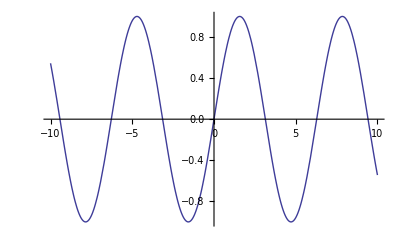

```mathematica
g=Plot[Sin[x],{x,-10,10}]
```

```mathematica
Export["/Users/kouamano/TEXT/JSSAC_201401/grexMac.pdf",g]
```

/Users/kouamano/TEXT/JSSAC_201401/grexMac.pdf

### 入力の違い

入力補完は自動ではなく、Ctrl-kで行われる。

### その他

オンラインヘルプはインターネット接続

並列処理
そもそもがシングルコアなので確認できないが、制限はされていない様子。

環境設定は行えない(すくなくともnbフロントエンドからは)

カーネルコンフィグも大幅にメニューが削減されている

リモートカーネルは使える

ハードウエアの能力に依存している部分が大きい
- 大きな計算はできない <- メモリが少ない
- グラフィクスの扱いが遅い <- CPUが非力、レンダリング時はいつもピークの使用
- スクロールも遅い

## RPi版 Mathematica 実演

## Mathematica on RPi の未来はどのようなものか

本来教育目的であったが、 Mathematica バンドルにより研究者の間に興味が広がった(それ以前から出荷台数は予想を越えていた。現在は175万台)。今後も同様の流れが続くと思われる。

### 自立的AIによるデータ収集とデータ集約の自動化

組み込みJAVA開発の状況に似ているが、開発・コーディングの敷居が一気に下がった。

開発環境で開発・テスト -> パッケージ作成・転送 -> インストール・実行

の手順が、

loginして直接コーディングするだけ

になり、かつ、

Mathematica のバンドルによりプログラミングの敷居も低くなった。

#### 環境科学

#### データサイエンス

#### システム監視

### ナレッジサービスにおけるよりリッチなUXの提供

ナレッジベースとナレッジサービスを同じ仕組みで構築できる(Knowledge Operation)。

カーネル間通信、およびカーネル-フロントエンド通信の仕組みがそのまま使える。

ユーザーがサービスやUIを簡単に構築できる(CGM)。

フロントエンドカスタマイズがそのまま使える。

nbの配布が簡単に行える。

#### Wolfram|Alpha

現在の主なフロントエンドはブラウザだが、携帯端末上のノートブックフロントエンドが直接使えるようになる。

#### LOD

MathematicaのコンテンツをXMLに変換し、直ちに配置できる(少し仕組みが必要)。

#### ユーザー間局所情報通信

ユーザー自身(もちろんメーカーでもよい)が構築したサービスを局所的に利用できる。

### 今後必要となる要素

堅牢性

ハードウエア、ソフトウエアともに堅牢性が求められる。

リアルタイム性

OSだけでなく、アプリケーション(Mathematica)にもリアルタイム性が求められる。

## 参考書紹介

お手軽ARMコンピュータ ラズベリー・パイでI/O ; CQ出版

ラズベリー・パイで作る手のひらLinuxパソコン ; CQ出版

Raspberry Pi ユーザーガイド ; 株式会社クイープ

Raspberry Pi [実用] 入門 ; 株式会社技術評論社

Amazonで検索すると40件以上。